# ALPRunner User Manual

SDB^1, JM^2, MR^2

U. Granada^1, IFT Madrid^2

05.05.2023

## Installing/Initialisation

### Install the ALPRunner package:

```mathematica
Import[URL["http://github.com/sdbakshi13/ALPRunner/blob/main/ALPRunner.m"]]
```

### Post-installation:

```mathematica
Needs["ALPRunner`"]
```

### Calling the RGEs

Call one of the following variables to get the corresponding RGEs.

```mathematica
?rg$*
```

Above, the one that begins with rg$L__ are the broken-phase SM RGEs and others are the unbroken-phase RGEs.

### RGE functions

```mathematica
?rge*reset
```

All these RGE reset functions solve coupled differential equation numerically for the given boundary conditions.

In the subsequent sections, we show their uses. We also produce the plots (as demonstration) that are discussed in the paper.

## The SM RGEs

The users set the value of SM couplings at some scale, here scale=172.

```mathematica
vevscaleboundaryConditionSM ={
g1[172]  ==  0.350,                    g2[172]==0.654,                        g3[172]==1.220,
μH2[172]==246^2 * λϕ[172],                   λϕ[172]==.13,

Ye11[172]==0.000003,                  Ye12[172]==0.,                       Ye13[172]==0.,
Ye21[172]==0.,                                Ye22[172]==0.0005748,        Ye23[172]==0.,
Ye31[172]==0.,                                Ye32[172]==0.,                        Ye33[172]==0.01023,    

Yd11[172]==0.000022402218714514104,
Yd12[172]==0.00013100800059039354,                   
Yd13[172]==0.000030630892115227004-0.00007897115443513078 ⅈ,

Yd21[172]==-5.185172146546565*^-6-3.042723119739366*^-9 ⅈ,
Yd22[172]==0.0005651646560389477-1.7793821109734878*^-8 ⅈ,
Yd23[172]==0.0010026651774180785,

Yd31[172]==1.8706544011996077*^-7-7.320794584782447*^-8 ⅈ,
Yd32[172]==-0.000023656137441897952-4.2811949722817027*^-7 ⅈ,
Yd33[172]==0.024124133259358013,

Yu11[172]==0.00001,                             Yu12[172]==0,                               Yu13[172]==0,                   
Yu21[172]==0.,                                        Yu22[172]==0.007,                      Yu23[172]==0,                  
Yu31[172]==0.,                                        Yu32[172]==0.,                               Yu33[172]==0.931
};
```

Use the following functions to create the SM RGEs.

```mathematica
rgeSMtoΛreset[vevscaleboundaryConditionSM,10^3,172];
```

This output stored in “rgeSMtoΛ” are the running of the SM couplings disregarding all contribution from the singlet. We will use this output to at some UV scale (1 TeV in this example).

## The xSMEFT rges

### The boundary conditions

We put the boundary conditions (BCs) for all couplings in the theory.

```mathematica
bsmHSparameters =Module[
{Λ = 1000,tmp1},
tmp1=Thread[((#[Λ]&/@(Head[#]&/@vevscaleboundaryConditionSM[[All,1]])))==(((#[Λ]&/@(Head[#]&/@vevscaleboundaryConditionSM[[All,1]])))/.rgeSMtoΛ)];
Join[
  {ms2[Λ]==2500.,                       λs[Λ]==0.000,                             λsϕ[Λ]==0.000,
κs[Λ] ==0.000,                      κsϕ[Λ]==0.000,                            as3[Λ]==0.000,                          as[Λ]==0.000,
asBt[Λ]==0.,                        asB[Λ]==0.000,                           asWt[Λ]==0.000,                        asW[Λ]==0.000,
asGt[Λ]==0.000,                  asG[Λ]==0.000,                           as5[Λ]==0.000,
aseϕ11[Λ]==0.,                     aseϕ12[Λ]==0.,                          aseϕ13[Λ]==0.,
aseϕ21[Λ]==0.,                     aseϕ22[Λ]==0.,                          aseϕ23[Λ]==0.,
aseϕ31[Λ]==0.,                     aseϕ32[Λ]==0.,                          aseϕ33[Λ]==0.,
asdϕ11[Λ]==0.,                     asdϕ12[Λ]==0.,                          asdϕ13[Λ]==0.,
asdϕ21[Λ]==0.,                     asdϕ22[Λ]==0.,                          asdϕ23[Λ]==0.,
asdϕ31[Λ]==0.,                     asdϕ32[Λ]==0.,                          asdϕ33[Λ]==0.,
asuϕ11[Λ]==0.,                     asuϕ12[Λ]==0.,                          asuϕ13[Λ]==0.,
asuϕ21[Λ]==0.,                     asuϕ22[Λ]==0.,                          asuϕ23[Λ]==0.,
asuϕ31[Λ]==0.,                     asuϕ32[Λ]==0.,                          asuϕ33[Λ]==0.},
(Flatten@Join[tmp1,(DeleteCases[Thread[Keys[#]->(Conjugate[Values[#]])]&/@(tmp1/.Equal->Rule),Alternatives@@{g1[_]->_,g2[_]->_,g3[_]->_,μH2[_]->_,λϕ[_]->_}]/.{Ye11->Yebar11,Ye12->Yebar12,Ye13->Yebar13,Ye21->Yebar21,Ye22->Yebar22,Ye23->Yebar23,Ye31->Yebar31,Ye32->Yebar32,Ye33->Yebar33,Yd11->Ydbar11,Yd12->Ydbar12,Yd13->Ydbar13,Yd21->Ydbar21,Yd22->Ydbar22,Yd23->Ydbar23,Yd31->Ydbar31,Yd32->Ydbar32,Yd33->Ydbar33,Yu11->Yubar11,Yu12->Yubar12,Yu13->Yubar13,Yu21->Yubar21,Yu22->Yubar22,Yu23->Yubar23,Yu31->Yubar31,Yu32->Yubar32,Yu33->Yubar33})/.Rule->Equal])
	]];
```

We call the function “rgePSEFTreset” with the BCs and the scales.

```mathematica
rgePSEFTreset[bsmHSparameters,1000,172]
```

### Parametric solving

```mathematica
bsmHSparameters =Module[
{Λ = 1000,tmp1},
tmp1=Thread[((#[Λ]&/@(Head[#]&/@vevscaleboundaryConditionSM[[All,1]])))==(((#[Λ]&/@(Head[#]&/@vevscaleboundaryConditionSM[[All,1]])))/.rgeSMtoΛ)];
Join[
  {ms2[Λ]==2500.,                       λs[Λ]==0.000,                             λsϕ[Λ]==0.000,
κs[Λ] ==0.000,                      κsϕ[Λ]==0.000,                            as3[Λ]==0.000,                          as[Λ]==0.000,
asBt[Λ]==0.,                        asB[Λ]==0.000,                           asWt[Λ]==0.000,                        asW[Λ]==0.000,
asGt[Λ]==0.000,                  asG[Λ]==0.000,                           as5[Λ]==0.000,
aseϕ11[Λ]==0.,                     aseϕ12[Λ]==0.,                          aseϕ13[Λ]==0.,
aseϕ21[Λ]==0.,                     aseϕ22[Λ]==0.,                          aseϕ23[Λ]==0.,
aseϕ31[Λ]==0.,                     aseϕ32[Λ]==0.,                          aseϕ33[Λ]==0.,
asdϕ11[Λ]==0.,                     asdϕ12[Λ]==0.,                          asdϕ13[Λ]==0.,
asdϕ21[Λ]==0.,                     asdϕ22[Λ]==0.,                          asdϕ23[Λ]==0.,
asdϕ31[Λ]==0.,                     asdϕ32[Λ]==0.,                          asdϕ33[Λ]==0.,
asuϕ11[Λ]==0.,                     asuϕ12[Λ]==0.,                          asuϕ13[Λ]==0.,
asuϕ21[Λ]==0.,                     asuϕ22[Λ]==0.,                          asuϕ23[Λ]==0.,
asuϕ31[Λ]==0.,                     asuϕ32[Λ]==0.,                          asuϕ33[Λ]==0.},
(Flatten@Join[tmp1,(DeleteCases[Thread[Keys[#]->(Conjugate[Values[#]])]&/@(tmp1/.Equal->Rule),Alternatives@@{g1[_]->_,g2[_]->_,g3[_]->_,μH2[_]->_,λϕ[_]->_}]/.{Ye11->Yebar11,Ye12->Yebar12,Ye13->Yebar13,Ye21->Yebar21,Ye22->Yebar22,Ye23->Yebar23,Ye31->Yebar31,Ye32->Yebar32,Ye33->Yebar33,Yd11->Ydbar11,Yd12->Ydbar12,Yd13->Ydbar13,Yd21->Ydbar21,Yd22->Ydbar22,Yd23->Ydbar23,Yd31->Ydbar31,Yd32->Ydbar32,Yd33->Ydbar33,Yu11->Yubar11,Yu12->Yubar12,Yu13->Yubar13,Yu21->Yubar21,Yu22->Yubar22,Yu23->Yubar23,Yu31->Yubar31,Yu32->Yubar32,Yu33->Yubar33})/.Rule->Equal])
	]];
```

```mathematica
rgePSEFTreset[bsmHSparameters,1000,172]
```

## Matching and tadople equations

```mathematica
bsmHSparameters =Module[
{Λ = 1000,tmp1},
tmp1=Thread[((#[Λ]&/@(Head[#]&/@vevscaleboundaryConditionSM[[All,1]])))==(((#[Λ]&/@(Head[#]&/@vevscaleboundaryConditionSM[[All,1]])))/.rgeSMtoΛ)];
Join[
  {ms2[Λ]==25.,                       λs[Λ]==0.000,                             λsϕ[Λ]==0.000,
κs[Λ] ==0.000,                      κsϕ[Λ]==0.000,                            as3[Λ]==0.000,                          as[Λ]==0.000,
asBt[Λ]==0.00,                     asB[Λ]==0.000,                           asWt[Λ]==0.000,                        asW[Λ]==0.000,
asGt[Λ]==0.00,                     asG[Λ]==0.0000,                           as5[Λ]==0.000,
aseϕ11[Λ]==0.,                     aseϕ12[Λ]==0.,                          aseϕ13[Λ]==0.,
aseϕ21[Λ]==0.,                     aseϕ22[Λ]==0.,                          aseϕ23[Λ]==0.,
aseϕ31[Λ]==0.,                     aseϕ32[Λ]==0.,                          aseϕ33[Λ]==0.,
asdϕ11[Λ]==0.0,                 asdϕ12[Λ]==0.0,                        asdϕ13[Λ]==0.00001,
asdϕ21[Λ]==0.,                     asdϕ22[Λ]==0.,                          asdϕ23[Λ]==0.,
asdϕ31[Λ]==0.,                     asdϕ32[Λ]==0.,                          asdϕ33[Λ]==0.,
asuϕ11[Λ]==0.,                     asuϕ12[Λ]==0.,                          asuϕ13[Λ]==0.,
asuϕ21[Λ]==0.,                     asuϕ22[Λ]==0.,                          asuϕ23[Λ]==0.,
asuϕ31[Λ]==0.0001,                     asuϕ32[Λ]==0.,                          asuϕ33[Λ]==0.},
(Flatten@Join[tmp1,(DeleteCases[Thread[Keys[#]->(Conjugate[Values[#]])]&/@(tmp1/.Equal->Rule),Alternatives@@{g1[_]->_,g2[_]->_,g3[_]->_,μH2[_]->_,λϕ[_]->_}]/.{Ye11->Yebar11,Ye12->Yebar12,Ye13->Yebar13,Ye21->Yebar21,Ye22->Yebar22,Ye23->Yebar23,Ye31->Yebar31,Ye32->Yebar32,Ye33->Yebar33,Yd11->Ydbar11,Yd12->Ydbar12,Yd13->Ydbar13,Yd21->Ydbar21,Yd22->Ydbar22,Yd23->Ydbar23,Yd31->Ydbar31,Yd32->Ydbar32,Yd33->Ydbar33,Yu11->Yubar11,Yu12->Yubar12,Yu13->Yubar13,Yu21->Yubar21,Yu22->Yubar22,Yu23->Yubar23,Yu31->Yubar31,Yu32->Yubar32,Yu33->Yubar33})/.Rule->Equal])
	]];
```

```mathematica
rgePSEFTparamsolvereset[bsmHSparameters,1000,172,{{μH2,μH2p},{λϕ,λϕp1}}];
rrmu=RandomReal[{(μH2[172]/.rgeSMtoΛ)-.5(μH2[172]/.rgeSMtoΛ),(μH2[172]/.rgeSMtoΛ)+(μH2[172]/.rgeSMtoΛ)},10];
rrλ=RandomReal[{0,(λϕ[172]/.rgeSMtoΛ)+3(λϕ[172]/.rgeSMtoΛ)},10];
interpolationpoints=With[{mu=1000,vev=172},
Table[{{muh2,lamphi},Chop[(#[vev]&/@rgePSEFTparamsolve[(μH2[mu]/.rgeSMtoΛ),(λϕ[mu]/.rgeSMtoΛ)]),10^(-$MachinePrecision)]},{muh2,rrmu},{lamphi,rrλ}]];
try1lst=Table[varsPSEFT[[k]]->InterpolatingPolynomial[Flatten[Table[{interpolationpoints[[i,j,1]],interpolationpoints[[i,j,2,k]]},{i,Dimensions[interpolationpoints][[1]]},{j,Dimensions[interpolationpoints][[2]]}],1],{muh2,lamphi}],{k,Length@varsPSEFT}];
```

0.021195

```mathematica
Module[{rrmu,rrλ,interpolationpoints,polynomialinmuh2lamphi1,theequations1,topmassscale=172,vacexpvalue=246,uvscale=1000,iv$lst1,iv$lst2,vaccumcheck},
rrmu=RandomReal[{(μH2[topmassscale]/.rgeSMtoΛ)-.5(μH2[topmassscale]/.rgeSMtoΛ),(μH2[topmassscale]/.rgeSMtoΛ)+(μH2[topmassscale]/.rgeSMtoΛ)},10];
rrλ=RandomReal[{0,(λϕ[topmassscale]/.rgeSMtoΛ)+3(λϕ[topmassscale]/.rgeSMtoΛ)},10];
interpolationpoints=With[{mu=1000,topmass=172},Table[{{muh2,lamphi},Chop[(#[topmass]&/@rgePSEFTparamsolve[(μH2[mu]/.rgeSMtoΛ),(λϕ[mu]/.rgeSMtoΛ)]),10^(-$MachinePrecision)]},{muh2,rrmu},{lamphi,rrλ}]];
polynomialinmuh2lamphi1=Table[varsPSEFT[[k]]->InterpolatingPolynomial[Flatten[Table[{interpolationpoints[[i,j,1]],interpolationpoints[[i,j,2,k]]},{i,Dimensions[interpolationpoints][[1]]},{j,Dimensions[interpolationpoints][[2]]}],1],{muh2,lamphi}],{k,Length@varsPSEFT}];
theequations1=({(-μH2 + λϕ Vϕ^2 + 1/2 Vs (2 κsϕ  + λsϕ  Vs) - as  Vϕ^2 Vs - as3  Vs^3),
-125.44^2+2λϕ  Vϕ^2- 2 as Vϕ^2 Vs+2/Vϕ(2 ms2  Vs + κs  Vs^2 + λs/3 Vs^3 + as Vϕ^4/2 -10 as5 Vs^4)*1/2*ArcTan[((-2 as Vϕ^4+40 as5 Vs^4-4/3 Vs(6 ms2 +3κs  Vs + λs  Vs^2))/(Vϕ((4 as  - 6 as3 ) Vϕ^2 Vs - 40 as5  Vs^3+2 ms2  + (-4λϕ +λsϕ )Vs^2+Vs(2κs +λs  Vs))))],
(- 2 ms2  Vs-κsϕ Vϕ^2 -λsϕ  Vϕ^2 Vs  -κs Vs^2 -λs/3 Vs^3 +as/2 Vϕ^4+ 3 as3   Vϕ^2 Vs^2 +10 as5  Vs^4)}/.polynomialinmuh2lamphi1 )/.Vϕ->vacexpvalue;
vaccumminimacheck[theequations1,polynomialinmuh2lamphi1]
]
```

True

```mathematica
μH2->7867.07169993757,λϕ->0.13000076025052987
```

```mathematica
μH2->7867.071699937442,λϕ->0.13000076025053917
```

```mathematica
μH2->7867.071699937442,λϕ->0.13000076025053917
```

7867.07

0.130001

```mathematica
7867.071641225404,0.13000077119378006
```

```mathematica
7867.071641225369,0.1300007711937806
```

```mathematica
Module[{rrmu,rrλ,interpolationpoints,polynomialinmuh2lamphi1,theequations1,topmassscale=172,vacexpvalue=246,uvscale=1000,iv$lst1,iv$lst2,vaccumcheck},
rrmu=RandomReal[{(μH2[topmassscale]/.rgeSMtoΛ)-.5(μH2[topmassscale]/.rgeSMtoΛ),(μH2[topmassscale]/.rgeSMtoΛ)+(μH2[topmassscale]/.rgeSMtoΛ)},10];
rrλ=RandomReal[{0,(λϕ[topmassscale]/.rgeSMtoΛ)+3(λϕ[topmassscale]/.rgeSMtoΛ)},10];
interpolationpoints=With[{mu=1000,topmass=172},Table[{{muh2,lamphi},Chop[(#[topmass]&/@rgePSEFTparamsolve[(μH2[mu]/.rgeSMtoΛ),(λϕ[mu]/.rgeSMtoΛ)]),10^(-$MachinePrecision)]},{muh2,rrmu},{lamphi,rrλ}]];
polynomialinmuh2lamphi1=Table[varsPSEFT[[k]]->InterpolatingPolynomial[Flatten[Table[{interpolationpoints[[i,j,1]],interpolationpoints[[i,j,2,k]]},{i,Dimensions[interpolationpoints][[1]]},{j,Dimensions[interpolationpoints][[2]]}],1],{muh2,lamphi}],{k,Length@varsPSEFT}];
theequations1=({(-μH2 + λϕ Vϕ^2 + 1/2 Vs (2 κsϕ  + λsϕ  Vs) - as  Vϕ^2 Vs - as3  Vs^3),
-125.44^2+2λϕ  Vϕ^2- 2 as Vϕ^2 Vs+2/Vϕ(2 ms2  Vs + κs  Vs^2 + λs/3 Vs^3 + as Vϕ^4/2 -10 as5 Vs^4)*1/2*ArcTan[((-2 as Vϕ^4+40 as5 Vs^4-4/3 Vs(6 ms2 +3κs  Vs + λs  Vs^2))/(Vϕ((4 as  - 6 as3 ) Vϕ^2 Vs - 40 as5  Vs^3+2 ms2  + (-4λϕ +λsϕ )Vs^2+Vs(2κs +λs  Vs))))],
(- 2 ms2  Vs-κsϕ Vϕ^2 -λsϕ  Vϕ^2 Vs  -κs Vs^2 -λs/3 Vs^3 +as/2 Vϕ^4+ 3 as3   Vϕ^2 Vs^2 +10 as5  Vs^4)}/.polynomialinmuh2lamphi1 )/.Vϕ->vacexpvalue;
polynomialinmuh2lamphi1
];
Association[%][μH2]
Association[%%][λϕ]
```

7867.07

0.130001

## and running in broken-phase

```mathematica
boundaryConditionLE=Chop[PSLEFTmatchingVS[172]/.Vϕ->246/.solveVsNP/.npparamters/.mixang,10^(-$MachinePrecision)]/.θQCD[172]->0;
rgeLEreset[boundaryConditionLE,172,5];
```

```mathematica
bsmHSparameters =Module[
{Λ = 1000,tmp1},
tmp1=Thread[((#[Λ]&/@(Head[#]&/@vevscaleboundaryConditionSM[[All,1]])))==(((#[Λ]&/@(Head[#]&/@vevscaleboundaryConditionSM[[All,1]])))/.rgeSMtoΛ)];
Join[
  {ms2[Λ]==2500.,                       λs[Λ]==0.000,                             λsϕ[Λ]==0.000,
κs[Λ] ==0.000,                      κsϕ[Λ]==0.000,                            as3[Λ]==0.000,                          as[Λ]==0.000,
asBt[Λ]==0.,                        asB[Λ]==0.000,                           asWt[Λ]==0.000,                        asW[Λ]==0.000,
asGt[Λ]==0.000,                  asG[Λ]==0.000,                           as5[Λ]==0.000,
aseϕ11[Λ]==0.,                     aseϕ12[Λ]==0.,                          aseϕ13[Λ]==0.,
aseϕ21[Λ]==0.,                     aseϕ22[Λ]==0.,                          aseϕ23[Λ]==0.,
aseϕ31[Λ]==0.,                     aseϕ32[Λ]==0.,                          aseϕ33[Λ]==0.,
asdϕ11[Λ]==0.,                     asdϕ12[Λ]==0.,                          asdϕ13[Λ]==0.,
asdϕ21[Λ]==0.,                     asdϕ22[Λ]==0.,                          asdϕ23[Λ]==0.,
asdϕ31[Λ]==0.,                     asdϕ32[Λ]==0.,                          asdϕ33[Λ]==0.,
asuϕ11[Λ]==0.,                     asuϕ12[Λ]==0.,                          asuϕ13[Λ]==0.,
asuϕ21[Λ]==0.,                     asuϕ22[Λ]==0.,                          asuϕ23[Λ]==0.,
asuϕ31[Λ]==0.,                     asuϕ32[Λ]==0.,                          asuϕ33[Λ]==0.},
(Flatten@Join[tmp1,(DeleteCases[Thread[Keys[#]->(Conjugate[Values[#]])]&/@(tmp1/.Equal->Rule),Alternatives@@{g1[_]->_,g2[_]->_,g3[_]->_,μH2[_]->_,λϕ[_]->_}]/.{Ye11->Yebar11,Ye12->Yebar12,Ye13->Yebar13,Ye21->Yebar21,Ye22->Yebar22,Ye23->Yebar23,Ye31->Yebar31,Ye32->Yebar32,Ye33->Yebar33,Yd11->Ydbar11,Yd12->Ydbar12,Yd13->Ydbar13,Yd21->Ydbar21,Yd22->Ydbar22,Yd23->Ydbar23,Yd31->Ydbar31,Yd32->Ydbar32,Yd33->Ydbar33,Yu11->Yubar11,Yu12->Yubar12,Yu13->Yubar13,Yu21->Yubar21,Yu22->Yubar22,Yu23->Yubar23,Yu31->Yubar31,Yu32->Yubar32,Yu33->Yubar33})/.Rule->Equal])
	]];
```

```mathematica
rgePSEFTreset[bsmHSparameters,1000,172]
```

## Shift invariant function

## Probing parameter space

## e-EDM, streamline-1

```mathematica
bsmHSparameters =Module[
{Λ = 1000,tmp1},
tmp1=Thread[((#[Λ]&/@(Head[#]&/@vevscaleboundaryConditionSM[[All,1]])))==(((#[Λ]&/@(Head[#]&/@vevscaleboundaryConditionSM[[All,1]])))/.rgeSMtoΛ)];
Join[
  {ms2[Λ]==2500.,                       λs[Λ]==0.000,                             λsϕ[Λ]==0.000,
κs[Λ] ==0.000,                      κsϕ[Λ]==0.000,                            as3[Λ]==0.000,                          as[Λ]==0.000,
asBt[Λ]==0.,                        asB[Λ]==0.000,                           asWt[Λ]==0.000,                        asW[Λ]==0.000,
asGt[Λ]==0.000,                  asG[Λ]==0.000,                           as5[Λ]==0.000,
aseϕ11[Λ]==0.,                     aseϕ12[Λ]==0.,                          aseϕ13[Λ]==0.,
aseϕ21[Λ]==0.,                     aseϕ22[Λ]==0.,                          aseϕ23[Λ]==0.,
aseϕ31[Λ]==0.,                     aseϕ32[Λ]==0.,                          aseϕ33[Λ]==0.,
asdϕ11[Λ]==0.,                     asdϕ12[Λ]==0.,                          asdϕ13[Λ]==0.,
asdϕ21[Λ]==0.,                     asdϕ22[Λ]==0.,                          asdϕ23[Λ]==0.,
asdϕ31[Λ]==0.,                     asdϕ32[Λ]==0.,                          asdϕ33[Λ]==0.,
asuϕ11[Λ]==0.,                     asuϕ12[Λ]==0.,                          asuϕ13[Λ]==0.,
asuϕ21[Λ]==0.,                     asuϕ22[Λ]==0.,                          asuϕ23[Λ]==0.,
asuϕ31[Λ]==0.,                     asuϕ32[Λ]==0.,                          asuϕ33[Λ]==0.},
(Flatten@Join[tmp1,(DeleteCases[Thread[Keys[#]->(Conjugate[Values[#]])]&/@(tmp1/.Equal->Rule),Alternatives@@{g1[_]->_,g2[_]->_,g3[_]->_,μH2[_]->_,λϕ[_]->_}]/.{Ye11->Yebar11,Ye12->Yebar12,Ye13->Yebar13,Ye21->Yebar21,Ye22->Yebar22,Ye23->Yebar23,Ye31->Yebar31,Ye32->Yebar32,Ye33->Yebar33,Yd11->Ydbar11,Yd12->Ydbar12,Yd13->Ydbar13,Yd21->Ydbar21,Yd22->Ydbar22,Yd23->Ydbar23,Yd31->Ydbar31,Yd32->Ydbar32,Yd33->Ydbar33,Yu11->Yubar11,Yu12->Yubar12,Yu13->Yubar13,Yu21->Yubar21,Yu22->Yubar22,Yu23->Yubar23,Yu31->Yubar31,Yu32->Yubar32,Yu33->Yubar33})/.Rule->Equal])
	]];
```

```mathematica
bsmHSparameters/.{μH2[1000]==_->μH2[1000]==8229.007345924641,λϕ[1000]==_->λϕ[1000]==0.10135493056517393};
rgePSEFTparamsolvereset[bsmHSparameters,1000,172,{{asBt,asBtparam},{asB,asBparam}}];
solveVsNP=FindRoot[(- 2 ms2  Vs-κsϕ Vϕ^2 -λsϕ  Vϕ^2 Vs  -κs Vs^2 -λs/3 Vs^3 +as/2 Vϕ^4+ 3 as3   Vϕ^2 Vs^2 +10 as5  Vs^4)/.Vϕ->246/.Chop[Thread[(varsPSEFT)->(#[172]&/@rgePSEFTparamsolve[(* asBtat1000 *)2.*10^(-6),(*asBat1000*) 1.4*10^(-6)])],10^(-$MachinePrecision)],{Vs,0}];
npparamters=Chop[Thread[(#[172]&/@varsPSEFT)->(#[172]&/@rgePSEFTparamsolve[(* asBtat1000 *)2.*10^(-6),(*asBat1000*) 3*10^(-6)])],10^(-$MachinePrecision)];
mixang={WCθ[172]->1/2*ArcTan[((-2 as Vϕ^4+40 as5 Vs^4-4/3 Vs(6 ms2 +3κs  Vs + λs  Vs^2))/(Vϕ((4 as  - 6 as3 ) Vϕ^2 Vs - 40 as5  Vs^3+2 ms2  + (-4λϕ +λsϕ )Vs^2+Vs(2κs +λs  Vs))))]/.(npparamters/.aa_[172]->aa)/.solveVsNP/.Vϕ->246};
boundaryConditionLE=Chop[PSLEFTmatchingVS[172]/.Vϕ->246/.solveVsNP/.npparamters/.mixang,10^(-$MachinePrecision)]/.θQCD[172]->0;
rgeLEreset[boundaryConditionLE,172,5];
```

0.021084

5.24295

```mathematica
WCOsAt[5.2]/.rgeLE
```

1.47055×10^-6

```mathematica
bsmHSparameters/.{μH2[1000]==_->μH2[1000]==8229.007345924641,λϕ[1000]==_->λϕ[1000]==0.10135493056517393};
rgePSEFTparamsolvereset[bsmHSparameters,1000,172,{{asBt,asBtparam},{asB,asBparam}}];
solveVsNP=FindRoot[(- 2 ms2  Vs-κsϕ Vϕ^2 -λsϕ  Vϕ^2 Vs  -κs Vs^2 -λs/3 Vs^3 +as/2 Vϕ^4+ 3 as3   Vϕ^2 Vs^2 +10 as5  Vs^4)/.Vϕ->246/.Chop[Thread[(varsPSEFT)->(#[172]&/@rgePSEFTparamsolve[(* asBtat1000 *)2.*10^(-6),(*asBat1000*) 1.4*10^(-6)])],10^(-$MachinePrecision)],{Vs,0}];
npparamters=Chop[Thread[(#[172]&/@varsPSEFT)->(#[172]&/@rgePSEFTparamsolve[(* asBtat1000 *)2.*10^(-6),(*asBat1000*) 1.4*10^(-6)])],10^(-8)]/.{(κsϕ[172]->_)->(κsϕ[172]->0),(asuϕ33[172]->_)->(asuϕ33[172]->0),(asuϕbar33[172]->_)->(asuϕbar33[172]->0)};
mixang={WCθ[172]->1/2*ArcTan[((-2 as Vϕ^4+40 as5 Vs^4-4/3 Vs(6 ms2 +3κs  Vs + λs  Vs^2))/(Vϕ((4 as  - 6 as3 ) Vϕ^2 Vs - 40 as5  Vs^3+2 ms2  + (-4λϕ +λsϕ )Vs^2+Vs(2κs +λs  Vs))))]/.(npparamters/.aa_[172]->aa)/.solveVsNP/.Vϕ->246};
boundaryConditionLE=Chop[PSLEFTmatchingVS[172]/.Vϕ->246/.solveVsNP/.npparamters/.mixang,10^(-$MachinePrecision)]/.θQCD[172]->0;
rgeLEreset[boundaryConditionLE,172,5];
```

0.014927

5.35557

```mathematica
αem=WCgem^2/(4π);
α3=WCg3^2/(4π);
QU={2/3,2/3,2/3};
QD={-1/3,-1/3,-1/3};
QL={-1,-1,-1};
hbarc=197.3269804*10^6*10^-15*10^-9 (* Factor required to convert from natural units in GeV^-1 to IS units in m. *);
DHgOVEReEXP=(6*10^-32(* m *))/hbarc (* GeV^-1*);
DnOVEReEXP=(1.8*10^-28(* m *))/hbarc  (* GeV^-1 *);
ωThOEXP=1.3(* mrad/s *);
L[x_]:=(3-4x+x^2 +2Log[x])/(1-x)^3;
F[z_]:=1/2 z NIntegrate[(1-2x(1-x))/(x(1-x)-z)Log[(x(1-x))/z],{x,0,1}];
G[z_]:=1/2 z NIntegrate[1/(x(1-x)-z)Log[(x(1-x))/z],{x,0,1}];
FunctionsRule={f->F,g->G,l->L};
```

```mathematica
a1n=.000005;
randompoints=Table[{RandomReal[{-a1n,a1n}],RandomReal[{-a1n,a1n}]},{n1,10000}];
Clear[datalistωThO,datalistωThO2];
datalistωThO={};datalistωThO2={};
Dynamic[datalistωThO];Dynamic[datalistωThO2];Dynamic[ListPlot[datalist]];Dynamic[ListPlot[datalist2]];
Dynamic[ListPlot[{datalistωThO,datalistωThO2}]]
```

```mathematica
ParallelDo[
solveVsNP=FindRoot[(- 2 ms2  Vs-κsϕ Vϕ^2 -λsϕ  Vϕ^2 Vs  -κs Vs^2 -λs/3 Vs^3 +as/2 Vϕ^4+ 3 as3   Vϕ^2 Vs^2 +10 as5  Vs^4)/.Vϕ->246/.Chop[Thread[(varsPSEFT)->(#[172]&/@rgePSEFTparamsolve[(* asBtat1000 *)2*10^(-6),(*asBat1000*)1.4*10^(-6)])],10^(-$MachinePrecision)],{Vs,0}];
npparamters=Chop[Thread[(#[172]&/@varsPSEFT)->(#[172]&/@rgePSEFTparamsolve[(* asBtat1000 *)2*10^(-6),(*asBat1000*)1.4*10^(-6)])],10^(-$MachinePrecision)];
mixang={WCθ[172]->1/2*ArcTan[((-2 as Vϕ^4+40 as5 Vs^4-4/3 Vs(6 ms2 +3κs  Vs + λs  Vs^2))/(Vϕ((4 as  - 6 as3 ) Vϕ^2 Vs - 40 as5  Vs^3+2 ms2  + (-4λϕ +λsϕ )Vs^2+Vs(2κs +λs  Vs))))]/.(npparamters/.aa_[172]->aa)/.solveVsNP/.Vϕ->246};
boundaryConditionLE=Chop[PSLEFTmatchingVS[172]/.Vϕ->246/.solveVsNP/.npparamters/.mixang,10^(-$MachinePrecision)]/.θQCD[172]->0;

rgeLEreset[boundaryConditionLE,172.,5.];

List1={2*10^(-6),(*asBat1000*)1.4*10^(-6),rgeLE};

RulePackage=Chop[Thread[(#[5])&/@List1[[3]][[All,1]]->((#[5])&/@List1[[3]][[All,1]]/.List1[[3]])]]//.{a_[5]->a};

{fermionmassmatrixU,fermionRotationVuL}={#[[1]],Transpose[#[[2]]]}&@(Chop[Reverse/@Eigensystem[(Table[ToExpression["MU"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}].ConjugateTranspose[Table[ToExpression["MU"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]])/.List1[[3]]]]);

{fermionmassmatrixU,fermionRotationVuR}={#[[1]],Transpose[#[[2]]]}&@(Chop[Reverse/@(Eigensystem[(ConjugateTranspose[Table[ToExpression["MU"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]].Table[ToExpression["MU"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}])/.List1[[3]]])]);

{fermionmassmatrixD,fermionRotationVdL}={#[[1]],Transpose[#[[2]]]}&@(Chop[Reverse/@Eigensystem[(Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}].ConjugateTranspose[Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]])/.List1[[3]]]]);

{fermionmassmatrixD,fermionRotationVdR}={#[[1]],Transpose[#[[2]]]}&@(Chop[Reverse/@(Eigensystem[(ConjugateTranspose[Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]].Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}])/.List1[[3]]])]);

{fermionmassmatrixE,fermionRotationVeL}={#[[1]],Transpose[#[[2]]]}&@(Chop[Reverse/@Eigensystem[(Table[ToExpression["ML"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}].ConjugateTranspose[Table[ToExpression["ML"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]])/.List1[[3]]]]);

{fermionmassmatrixE,fermionRotationVeR}={#[[1]],Transpose[#[[2]]]}&@(Chop[Reverse/@(Eigensystem[(ConjugateTranspose[Table[ToExpression["ML"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]].Table[ToExpression["ML"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}])/.List1[[3]]])]);

CEpckg=(ConjugateTranspose[fermionRotationVeL].{{WCOsce11,WCOsce12,WCOsce13},{WCOsce21,WCOsce22,WCOsce23},{WCOsce31,WCOsce32,WCOsce33}}.fermionRotationVeR);

CUpckg=(ConjugateTranspose[fermionRotationVuL].{{WCOscu11,WCOscu12,WCOscu13},{WCOscu21,WCOscu22,WCOscu23},{WCOscu31,WCOscu32,WCOscu33}}.fermionRotationVuR);

CDpckg=(ConjugateTranspose[fermionRotationVdL].{{WCOscd11,WCOscd12,WCOscd13},{WCOscd21,WCOscd22,WCOscd23},{WCOscd31,WCOscd32,WCOscd33}}.fermionRotationVdR);

MU2pckg=DiagonalMatrix[fermionmassmatrixU];

MD2pckg=DiagonalMatrix[fermionmassmatrixD];

ML2pckg=DiagonalMatrix[fermionmassmatrixE];

Cud=-(Im[CUpckg[[1,1]]]Re[CDpckg[[1,1]]])/WCms2;
Cdu=-(Im[CDpckg[[1,1]]]Re[CUpckg[[1,1]]])/WCms2;
Cue=-(Im[CUpckg[[1,1]]]Re[CEpckg[[1,1]]])/WCms2;
Ceu=-(Im[CEpckg[[1,1]]]Re[CUpckg[[1,1]]])/WCms2;
Cde=-(Im[CDpckg[[1,1]]]Re[CEpckg[[1,1]]])/WCms2;
Ced=-(Im[CEpckg[[1,1]]]Re[CDpckg[[1,1]]])/WCms2;
CGe=(4π)/(WCms2 WCg3^2)WCOsG(CEpckg[[1,1]]+Conjugate[CEpckg[[1,1]]])/2;
CGte=(4π)/(WCms2 WCg3^2)WCOsGt(I(CEpckg[[1,1]]-Conjugate[CEpckg[[1,1]]]))/2;
CS=-17 Vϕ^2 (Cue +Cde)+Vϕ^2(4.7 (*GeV*))CGe; 
CP=350 Vϕ^2(Ceu + Ced)+ Vϕ^2(1.1 (*GeV*))CGte;

DG=- (WCg3 α3)/(4 π)^3(∑_(i=1)^3 (h[MD2pckg⟦i,i⟧/WCms2] Im[CDpckg⟦i,i⟧] Re[CDpckg⟦i,i⟧])/(4 MD2pckg⟦i,i⟧)+∑_(j=1)^2 (h[MU2pckg⟦j,j⟧/WCms2] Im[CUpckg⟦j,j⟧] Re[CUpckg⟦j,j⟧])/(4 MU2pckg⟦j,j⟧))+(3 WCg3 WCOsG WCOsGt)/π^2 Log[Λ/Sqrt[WCms2]];
D1e=WCgem/(16 π^2 WCms2)Im[Dot[(CEpckg - ConjugateTranspose[CEpckg])/2,DiagonalMatrix[QL],Sqrt[ML2pckg],DiagonalMatrix[l[Diagonal[ML2pckg/WCms2]]/.RulePackage  /.FunctionsRule],(CEpckg + ConjugateTranspose[CEpckg])/2][[1,1]]];

D2e=(WCgem αem QL[[1]])/(8 π^3)(∑_(i=1)^3 (3 QD[[i]]^2)/Sqrt[MD2pckg[[i,i]]]*(f[MD2pckg[[i,i]]/WCms2]Re[CEpckg[[1,1]]] Im[CDpckg[[i,i]]] + g[MD2pckg[[i,i]]/WCms2]Im[CEpckg[[1,1]]] Re[CDpckg[[i,i]]]) + ∑_(j=1)^2 (3 QU[[j]]^2)/Sqrt[MU2pckg[[j,j]]]*(f[MU2pckg[[j,j]]/WCms2]Re[CEpckg[[1,1]]] Im[CUpckg[[j,j]]] + g[MU2pckg[[j,j]]/WCms2]Im[CEpckg[[1,1]]] Re[CUpckg[[j,j]]]) + ∑_(i=1)^3 QL[[i]]^2/Sqrt[ML2pckg[[i,i]]]*(f[ML2pckg[[i,i]]/WCms2]Re[CEpckg[[1,1]]] Im[CEpckg[[i,i]]] + g[ML2pckg[[i,i]]/WCms2]Im[CEpckg[[1,1]]] Re[CEpckg[[i,i]]]));
D3e=(QL[[1]]WCgem)/(2 π^2)(WCOsAt Im[CEpckg[[1,1]]] + WCOsA Re[CEpckg[[1,1]]])Log[Λ/Sqrt[WCms2]];
D4e=-(3 QL[[1]]^3 WCgem αem)/π^3 Sqrt[ML2pckg[[1,1]]]WCOsA WCOsAt Log[Λ/Sqrt[WCms2]]^2;
De=D1e+D2e+D3e+D4e;

(*D1u=WCgem/(16 π^2 WCms2)Im[Dot[(CUpckg - ConjugateTranspose[CUpckg])/2,DiagonalMatrix[QU],Sqrt[MU2pckg],DiagonalMatrix[l[Diagonal[MU2pckg/WCms2]]/.RulePackage  /.FunctionsRule],(CUpckg + ConjugateTranspose[CUpckg])/2][[1,1]]];

D2u=(WCgem αem QU[[1]])/(8 π^3)(∑_(i=1)^3 (3 QD[[i]]^2)/Sqrt[MD2pckg[[i,i]]]*(f[MD2pckg[[i,i]]/WCms2]Re[CUpckg[[1,1]]] Im[CDpckg[[i,i]]] + g[MD2pckg[[i,i]]/WCms2]Im[CUpckg[[1,1]]] Re[CDpckg[[i,i]]]) + ∑_(j=1)^2 (3 QU[[j]]^2)/Sqrt[MU2pckg[[j,j]]]*(f[MU2pckg[[j,j]]/WCms2]Re[CUpckg[[1,1]]] Im[CUpckg[[j,j]]] + g[MU2pckg[[j,j]]/WCms2]Im[CUpckg[[1,1]]] Re[CUpckg[[j,j]]]) + ∑_(i=1)^3 QL[[i]]^2/Sqrt[ML2pckg[[i,i]]]*(f[ML2pckg[[i,i]]/WCms2]Re[CUpckg[[1,1]]] Im[CEpckg[[i,i]]] + g[ML2pckg[[i,i]]/WCms2]Im[CUpckg[[1,1]]] Re[CEpckg[[i,i]]]));
D3u=(QU[[1]]WCgem)/(2 π^2)(WCOsAt Im[CUpckg[[1,1]]] + WCOsA Re[CUpckg[[1,1]]])Log[Λ/Sqrt[WCms2]];
D4u=-(3 QU[[1]]^3 WCgem αem)/π^3 Sqrt[MU2pckg[[1,1]]]WCOsA WCOsAt Log[Λ/Sqrt[WCms2]]^2;
D5u=-(2 QU[[1]] WCgem α3)/π^3Sqrt[MU2pckg[[1,1]]](WCOsA WCOsGt + WCOsAt WCOsG)Log[Λ/Sqrt[WCms2]]^2;
Du=D1u+D2u+D3u+D4u+D5u;*)

(*
D1d=WCgem/(16 π^2 WCms2)Im[Dot[(CDpckg - ConjugateTranspose[CDpckg])/2,DiagonalMatrix[QD],Sqrt[MD2pckg],DiagonalMatrix[l[Diagonal[MD2pckg/WCms2]]/.RulePackage  /.FunctionsRule],(CDpckg + ConjugateTranspose[CDpckg])/2][[1,1]]];

D2d=(WCgem αem QD[[1]])/(8 π^3)(∑_(i=1)^3 (3 QD[[i]]^2)/Sqrt[MD2pckg[[i,i]]]*(f[MD2pckg[[i,i]]/WCms2]Re[CDpckg[[1,1]]] Im[CDpckg[[i,i]]] + g[MD2pckg[[i,i]]/WCms2]Im[CDpckg[[1,1]]] Re[CDpckg[[i,i]]]) + ∑_(j=1)^2 (3 QU[[j]]^2)/Sqrt[MU2pckg[[j,j]]]*(f[MU2pckg[[j,j]]/WCms2]Re[CDpckg[[1,1]]] Im[CUpckg[[j,j]]] + g[MU2pckg[[j,j]]/WCms2]Im[CDpckg[[1,1]]] Re[CUpckg[[j,j]]])+ ∑_(i=1)^3 QL[[i]]^2/Sqrt[ML2pckg[[i,i]]]*(f[ML2pckg[[i,i]]/WCms2]Re[CDpckg[[1,1]]] Im[CEpckg[[i,i]]] + g[ML2pckg[[i,i]]/WCms2]Im[CDpckg[[1,1]]] Re[CEpckg[[i,i]]]));
D3d=(QD[[1]]WCgem)/(2 π^2)(WCOsAt Im[CDpckg[[1,1]]] + WCOsA Re[CDpckg[[1,1]]])Log[Λ/Sqrt[WCms2]];
D4d=-(3 QD[[1]]^3 WCgem αem)/π^3 Sqrt[MD2pckg[[1,1]]]WCOsA WCOsAt Log[Λ/Sqrt[WCms2]]^2;
D5d=-(2 QD[[1]] WCgem α3)/π^3Sqrt[MD2pckg[[1,1]]](WCOsA WCOsGt + WCOsAt WCOsG)Log[Λ/Sqrt[WCms2]]^2;
Dd=D1d+D2d+D3d+D4d+D5d;*)


(*D1uC=1/(16 π^2 WCms2)Im[Dot[(CUpckg - ConjugateTranspose[CUpckg])/2,Sqrt[MU2pckg],DiagonalMatrix[l[Diagonal[MU2pckg/WCms2]]/.RulePackage  /.FunctionsRule],(CUpckg + ConjugateTranspose[CUpckg])/2][[1,1]]];

D2uC=α3/(16 π^3)(∑_(i=1)^3 1/Sqrt[MD2pckg[[i,i]]]*(f[MD2pckg[[i,i]]/WCms2]Re[CUpckg[[1,1]]] Im[CDpckg[[i,i]]] + g[MD2pckg[[i,i]]/WCms2]Im[CUpckg[[1,1]]] Re[CDpckg[[i,i]]]) + ∑_(j=1)^2 1/Sqrt[MU2pckg[[j,j]]]*(f[MU2pckg[[j,j]]/WCms2]Re[CUpckg[[1,1]]] Im[CUpckg[[j,j]]] + g[MU2pckg[[j,j]]/WCms2]Im[CUpckg[[1,1]]] Re[CUpckg[[j,j]]]));
D3uC=1/(2 π^2)(WCOsGt Im[CUpckg[[1,1]]] + WCOsG Re[CUpckg[[1,1]]])Log[Λ/Sqrt[WCms2]];
D4uC=-(4α3)/π^3 Sqrt[MU2pckg[[1,1]]]WCOsG WCOsGt Log[Λ/Sqrt[WCms2]]^2;
D5uC=-(3 QU[[1]]^2  αem)/(2 π^3)Sqrt[MU2pckg[[1,1]]](WCOsA WCOsGt + WCOsAt WCOsG)Log[Λ/Sqrt[WCms2]]^2;
DuC=D1uC+D2uC+D3uC+D4uC+D5uC;
*)
(*D1dC=1/(16 π^2 WCms2)Im[Dot[(CDpckg - ConjugateTranspose[CDpckg])/2,Sqrt[MD2pckg],DiagonalMatrix[l[Diagonal[MD2pckg/WCms2]]/.RulePackage  /.FunctionsRule],(CDpckg + ConjugateTranspose[CDpckg])/2][[1,1]]];

D2dC=α3/(16 π^3)(∑_(i=1)^3 1/Sqrt[MD2pckg[[i,i]]]*(f[MD2pckg[[i,i]]/WCms2]Re[CDpckg[[1,1]]] Im[CDpckg[[i,i]]] + g[MD2pckg[[i,i]]/WCms2]Im[CDpckg[[1,1]]] Re[CDpckg[[i,i]]]) + ∑_(j=1)^2 1/Sqrt[MU2pckg[[j,j]]]*(f[MU2pckg[[j,j]]/WCms2]Re[CDpckg[[1,1]]] Im[CUpckg[[j,j]]] + g[MU2pckg[[j,j]]/WCms2]Im[CDpckg[[1,1]]] Re[CUpckg[[j,j]]]));
D3dC=1/(2 π^2)(WCOsGt Im[CDpckg[[1,1]]] + WCOsG Re[CDpckg[[1,1]]])Log[Λ/Sqrt[WCms2]];
D4dC=-(4α3)/π^3 Sqrt[MD2pckg[[1,1]]]WCOsG WCOsGt Log[Λ/Sqrt[WCms2]]^2;
D5dC=-(3 QD[[1]]^2  αem)/(2 π^3)Sqrt[MD2pckg[[1,1]]](WCOsA WCOsGt + WCOsAt WCOsG)Log[Λ/Sqrt[WCms2]]^2;
DdC=D1dC+D2dC+D3dC+D4dC+D5dC;
*)

(*Dn=(0.784*Du - 0.204 Dd - 0.55 WCgem DuC - 1.10 WCgem DdC + (50*10^-3 (*GeV*))WCgem DG + (30*10^-3 (*GeV*))WCgem(Cud - Cdu))  (*e*GeV^-1*);
DHg=4.0*10^-4 Dn - ((2.8 CS - 2.1CP)*10^-24 (* m *))WCgem/hbarc   (*e*GeV^-1*);
*)ωThO= (1.2 (*mrad/s*))(De/WCgem(10^31(*m^-1*)*hbarc    (*GeV*))) +  (1.8(*mrad/s*))(CS*10^9);
(*DnRATIO=(Dn/WCgem (* GeV^-1 *))/(DnOVEReEXP (* GeV^-1*))//.RulePackage/.FunctionsRule/.{Vϕ->246,Λ->1000};
DHgRATIO=((DHg/WCgem (* GeV^-1 *))/(DHgOVEReEXP (* GeV^-1*)))//.RulePackage/.FunctionsRule/.{Vϕ->246,Λ->1000};
*)ωThORATIO=((ωThO (*mrad/s*))/ωThOEXP)//.RulePackage/.FunctionsRule/.{Vϕ->246,Λ->1000};


If[0<= Abs[ωThORATIO]<= 1,AppendTo[datalistωThO,{randompoints[[n1,1]],randompoints[[n1,2]]}],AppendTo[datalistωThO2,{randompoints[[n1,1]],randompoints[[n1,2]]}]];
(*If[0<= Abs[DHgRATIO]<= 1,AppendTo[datalistdHg,{randompoints[[n1,1]],randompoints[[n1,2]]}],AppendTo[datalistdHg2,{randompoints[[n1,1]],randompoints[[n1,2]]}]];
If[0<= Abs[DnRATIO]<= 1,AppendTo[datalistdn,{randompoints[[n1,1]],randompoints[[n1,2]]}],AppendTo[datalistdn2,{randompoints[[n1,1]],randompoints[[n1,2]]}]];
*)
(*Print[{D1e,D2e,D3e,D4e, (1.8(*mrad/s*))(CS*10^9),CEpckg,{{WCOsce11,WCOsce12,WCOsce13},{WCOsce21,WCOsce22,WCOsce23},{WCOsce31,WCOsce32,WCOsce33}}} /.RulePackage /.FunctionsRule /.{Vϕ->246,Λ->1000}]*)
,{n1,24}];
Export["asBt_asB_50GeV_24pts_w=5(power10_-6).m",{datalistωThO,datalistωThO2}];
```

## asG, streamline-1

```mathematica
bsmHSparameters =Module[
{Λ = 1000,tmp1},
tmp1=Thread[((#[Λ]&/@(Head[#]&/@vevscaleboundaryConditionSM[[All,1]])))==(((#[Λ]&/@(Head[#]&/@vevscaleboundaryConditionSM[[All,1]])))/.rgeSMtoΛ)];
Join[
  {ms2[Λ]==36.,                       λs[Λ]==0.000,                             λsϕ[Λ]==0.000,
κs[Λ] ==0.000,                      κsϕ[Λ]==0.000,                            as3[Λ]==0.000,                          as[Λ]==0.000,
asBt[Λ]==0.,                    asB[Λ]==0.000,                           asWt[Λ]==0.000,                        asW[Λ]==0.000,
asGt[Λ]==0.000,                  asG[Λ]==0.000,                           as5[Λ]==0.000,
aseϕ11[Λ]==0.,                     aseϕ12[Λ]==0.,                          aseϕ13[Λ]==0.,
aseϕ21[Λ]==0.,                     aseϕ22[Λ]==0.,                          aseϕ23[Λ]==0.,
aseϕ31[Λ]==0.,                     aseϕ32[Λ]==0.,                          aseϕ33[Λ]==0.,
asdϕ11[Λ]==0.,                     asdϕ12[Λ]==0.,                          asdϕ13[Λ]==0.,
asdϕ21[Λ]==0.,                     asdϕ22[Λ]==0.,                          asdϕ23[Λ]==0.,
asdϕ31[Λ]==0.,                     asdϕ32[Λ]==0.,                          asdϕ33[Λ]==0.,
asuϕ11[Λ]==0.,                     asuϕ12[Λ]==0.,                          asuϕ13[Λ]==0.,
asuϕ21[Λ]==0.,                     asuϕ22[Λ]==0.,                          asuϕ23[Λ]==0.,
asuϕ31[Λ]==0.,                     asuϕ32[Λ]==0.,                          asuϕ33[Λ]==0.},
(Flatten@Join[tmp1,(DeleteCases[Thread[Keys[#]->(Conjugate[Values[#]])]&/@(tmp1/.Equal->Rule),Alternatives@@{g1[_]->_,g2[_]->_,g3[_]->_,μH2[_]->_,λϕ[_]->_}]/.{Ye11->Yebar11,Ye12->Yebar12,Ye13->Yebar13,Ye21->Yebar21,Ye22->Yebar22,Ye23->Yebar23,Ye31->Yebar31,Ye32->Yebar32,Ye33->Yebar33,Yd11->Ydbar11,Yd12->Ydbar12,Yd13->Ydbar13,Yd21->Ydbar21,Yd22->Ydbar22,Yd23->Ydbar23,Yd31->Ydbar31,Yd32->Ydbar32,Yd33->Ydbar33,Yu11->Yubar11,Yu12->Yubar12,Yu13->Yubar13,Yu21->Yubar21,Yu22->Yubar22,Yu23->Yubar23,Yu31->Yubar31,Yu32->Yubar32,Yu33->Yubar33})/.Rule->Equal])
	]];
```

```mathematica
bsmHSparameters/.{μH2[1000]==_->μH2[1000]==7867.071641225404,λϕ[1000]==_->λϕ[1000]==0.13000077119378006};
rgePSEFTparamsolvereset[bsmHSparameters,1000,172,{{asGt,asGtparam},{asG,asGparam}}];
solveVsNP=FindRoot[(- 2 ms2  Vs-κsϕ Vϕ^2 -λsϕ  Vϕ^2 Vs  -κs Vs^2 -λs/3 Vs^3 +as/2 Vϕ^4+ 3 as3   Vϕ^2 Vs^2 +10 as5  Vs^4)/.Vϕ->246/.chop[Thread[(varsPSEFT)->(#[172]&/@rgePSEFTparamsolve[(* asGtat1000 *)1.*10^(-6),(*asGat1000*) 1.*10^(-6)])]],{Vs,0}];
npparamters=chop[Thread[(#[172]&/@varsPSEFT)->(#[172]&/@rgePSEFTparamsolve[(* asGtat1000 *)1.*10^(-6),(*asGat1000*) 1.*10^(-6)])]];
mixang={WCθ[172]->1/2*ArcTan[((-2 as Vϕ^4+40 as5 Vs^4-4/3 Vs(6 ms2 +3κs  Vs + λs  Vs^2))/(Vϕ((4 as  - 6 as3 ) Vϕ^2 Vs - 40 as5  Vs^3+2 ms2  + (-4λϕ +λsϕ )Vs^2+Vs(2κs +λs  Vs))))]/.(npparamters/.aa_[172]->aa)/.solveVsNP/.Vϕ->246};
boundaryConditionLE=chop[PSLEFTmatchingVS[172]/.Vϕ->246/.solveVsNP/.npparamters/.mixang]/.θQCD[172]->0;
rgeLEreset[boundaryConditionLE,172,5];
```

0.018097

5.40497

```mathematica
αem=WCgem^2/(4π);
α3=WCg3^2/(4π);
QU={2/3,2/3,2/3};
QD={-1/3,-1/3,-1/3};
QL={-1,-1,-1};
hbarc=197.3269804*10^6*10^-15*10^-9 (* Factor required to convert from natural units in GeV^-1 to IS units in m. *);
DHgOVEReEXP=(6*10^-32(* m *))/hbarc (* GeV^-1*);
DnOVEReEXP=(1.8*10^-28(* m *))/hbarc  (* GeV^-1 *);
ωThOEXP=1.3(* mrad/s *);
L[x_]:=(3-4x+x^2 +2Log[x])/(1-x)^3;
F[z_]:=1/2 z NIntegrate[(1-2x(1-x))/(x(1-x)-z)Log[(x(1-x))/z],{x,0,1}];
G[z_]:=1/2 z NIntegrate[1/(x(1-x)-z)Log[(x(1-x))/z],{x,0,1}];
H[z_]:=NIntegrate[1+(z^2 u^3 x^3(1-x))/(z x(1-u x)+(1-u)(1-x))^2,{u,0,1},{x,0,1},Method->{"GlobalAdaptive","SingularityHandler"->"DuffyCoordinates"}];
H[z_]:=1;
FunctionsRule={f->F,g->G,h->H,l->L};
```

```mathematica
(*a1n=.000005;
randompoints=Table[{RandomReal[{-a1n,a1n}],RandomReal[{-a1n,a1n}]},{n1,5000}];*)
```

```mathematica
randompoints={{-2.797420713724955*^-6,-2.350798138330227*^-6},{-3.824908798594155*^-7,-3.0446767229721608*^-6}};
```

```mathematica
randompoints={{-2.1068299348718403*^-6,4.3242210038790915*^-6},{6.798523756634036*^-8,3.7326685085211544*^-6}};
```

```mathematica
randompoints={{-2.9* 10^-7, -2.2* 10^-7},{-2.1* 10^-7,-1.2*10^-8}};
```

```mathematica
Cases[ffff[[1,1]],lst_List/;lst[[1]]<0&&lst[[2]]>0]
```

Part::partd: Part specification ffff⟦1,1⟧ is longer than depth of object.

{}

```mathematica
{6.798523756634036*^-8,3.7326685085211544*^-6}
```

```mathematica
(*ListPlot[{{Style[{-2.797420713724955*^-6,-2.350798138330227*^-6},Green]},{Style[{-3.824908798594155*^-7,-3.0446767229721608*^-6},Red]}}]*)
```

```mathematica
chop1[null_]:=null
```

```mathematica
FindRoot[(- 2 ms2  Vs-κsϕ Vϕ^2 -λsϕ  Vϕ^2 Vs  -κs Vs^2 -λs/3 Vs^3 +as/2 Vϕ^4+ 3 as3   Vϕ^2 Vs^2 +10 as5  Vs^4)/.Vϕ->246/.chop[Thread[(varsPSEFT)->(#[172]&/@rgePSEFTparamsolve[(* asBtat1000 *)randompoints[[1,1]],(*asBat1000*) randompoints[[1,2]]])]],{Vs,0}]
```

{Vs→3.69674}

```mathematica
3 asuϕ33[172]/.npparamters
```

-5.47902×10^-7-4.36127×10^-6 ⅈ

```mathematica
3 asuϕ11[172]/.npparamters
```

-5.94078×10^-12-4.72878×10^-11 ⅈ

```mathematica
Clear[datalistdHg,datalistdHg2,datalistdn,datalistdn2,massmatrixsave];
```

```mathematica
datalistdHg={};datalistdHg2={};datalistdn={};datalistdn2={};massmatrixsave={};
```

```mathematica
Dynamic[datalistdHg,datalistdHg2];
```

```mathematica
Dynamic[ListPlot[{datalistdHg,datalistdHg2}]]
```

```mathematica
a1n=.000004;
randompoints=Table[{RandomReal[{-a1n,a1n}],RandomReal[{-a1n,a1n}]},{n1,5000}];
```

```mathematica
(*Dynamic[datalistdHg]
Dynamic[datalistdHg2]
Dynamic[datalistdn]
Dynamic[datalistdn2]
Dynamic[ListPlot[{datalistdHg,datalistdHg2}]]
Dynamic[ListPlot[{datalistdn,datalistdn2}]]*)
Do[
solveVsNP=FindRoot[(- 2 ms2  Vs-κsϕ Vϕ^2 -λsϕ  Vϕ^2 Vs  -κs Vs^2 -λs/3 Vs^3 +as/2 Vϕ^4+ 3 as3   Vϕ^2 Vs^2 +10 as5  Vs^4)/.Vϕ->245.999/.chop[Thread[(varsPSEFT)->(#[172]&/@rgePSEFTparamsolve[(* asBtat1000 *)randompoints[[n1,1]],(*asBat1000*) randompoints[[n1,2]]])]],{Vs,0}];
npparamters=chop[Thread[(#[172]&/@varsPSEFT)->(#[172]&/@rgePSEFTparamsolve[(* asBtat1000 *)randompoints[[n1,1]],(*asBat1000*) randompoints[[n1,2]]])]];
mixang={WCθ[172]->1/2*ArcTan[((-2 as Vϕ^4+40 as5 Vs^4-4/3 Vs(6 ms2 +3κs  Vs + λs  Vs^2))/(Vϕ((4 as  - 6 as3 ) Vϕ^2 Vs - 40 as5  Vs^3+2 ms2  + (-4λϕ +λsϕ )Vs^2+Vs(2κs +λs  Vs))))]/.(npparamters/.aa_[172]->aa)/.solveVsNP/.Vϕ->245.999};
boundaryConditionLE=chop[(PSLEFTmatchingVS[172]/.{(MU33[172]==_->MU33[172]==0),(MUbar33[172]==_->MUbar33[172]==0)})/.Vϕ->245.999/.solveVsNP/.npparamters/.mixang]/.θQCD[172]->0;


rgeLEreset[boundaryConditionLE,172.,5.];

List1={randompoints[[n1,1]],randompoints[[n1,2]],rgeLE};

RulePackage=chop[(Thread[(#[5])&/@List1[[3]][[All,1]]->((#[5])&/@List1[[3]][[All,1]]/.List1[[3]])]/.{(MU33[5]->_)->(MU33[5]->222),(MUbar33[5]->_)->(MUbar33[5]->222)})]//.{a_[5]->a};
RulePackagedummy=chop[(Thread[(#[5])&/@List1[[3]][[All,1]]->((#[5])&/@List1[[3]][[All,1]]/.List1[[3]])]/.{(MU33[5]->_)->(MU33[5]->222),(MUbar33[5]->_)->(MUbar33[5]->222)})];


{fermionmassmatrixU,fermionRotationVuLwophase}={#[[1]],Transpose[#[[2]]]}&@(Reverse/@Eigensystem[chop[(Table[ToExpression["MU"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}] . ConjugateTranspose[Table[ToExpression["MU"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]])/.RulePackagedummy]]);

{fermionmassmatrixU,fermionRotationVuR}={#[[1]],Transpose[#[[2]]]}&@(Reverse/@(Eigensystem[chop[(ConjugateTranspose[Table[ToExpression["MU"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]] . Table[ToExpression["MU"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}])/.RulePackagedummy]]));

{fermionmassmatrixD,fermionRotationVdLwophase}={#[[1]],Transpose[#[[2]]]}&@(Reverse/@Eigensystem[chop[(Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}] . ConjugateTranspose[Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]])/.RulePackagedummy]]);

{fermionmassmatrixD,fermionRotationVdR}={#[[1]],Transpose[#[[2]]]}&@(Reverse/@(Eigensystem[chop[(ConjugateTranspose[Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]] . Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}])/.RulePackagedummy]]));

{fermionmassmatrixE,fermionRotationVeLwophase}={#[[1]],Transpose[#[[2]]]}&@(Reverse/@Eigensystem[chop[(Table[ToExpression["ML"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}] . ConjugateTranspose[Table[ToExpression["ML"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]])/.RulePackagedummy]]);

{fermionmassmatrixE,fermionRotationVeR}={#[[1]],Transpose[#[[2]]]}&@(Reverse/@(Eigensystem[chop[(ConjugateTranspose[Table[ToExpression["ML"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]] . Table[ToExpression["ML"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}])/.RulePackagedummy]]));


(* new lines *)
(*this is mass matrices*)
massu=(Table[ToExpression["MU"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]/.RulePackagedummy);
massd=(Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]/.RulePackagedummy);
masse=(Table[ToExpression["ML"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]/.RulePackagedummy);
(*I am using diagonalzing but the diagonal elements contain phases in step below.*)
massdiagwithphaseU=ConjugateTranspose[fermionRotationVuLwophase].massu.fermionRotationVuR;
massdiagwithphaseD=ConjugateTranspose[fermionRotationVdLwophase].massd.fermionRotationVdR;
massdiagwithphaseE=ConjugateTranspose[fermionRotationVeLwophase].masse.fermionRotationVeR;
(*Here I am extracting out the phase*)
phaseU=DiagonalMatrix@Sqrt[fermionmassmatrixU].Inverse[chop[massdiagwithphaseU]];
phaseD=DiagonalMatrix@Sqrt[fermionmassmatrixD].Inverse[chop[massdiagwithphaseD]];
phaseE=DiagonalMatrix@Sqrt[fermionmassmatrixE].Inverse[chop[massdiagwithphaseE]];
(*New definitions for rotation matrices.*)
fermionRotationVuL=fermionRotationVuLwophase.ConjugateTranspose[phaseU];
fermionRotationVdL=fermionRotationVdLwophase.ConjugateTranspose[phaseD];
fermionRotationVeL=fermionRotationVeLwophase.ConjugateTranspose[phaseE];

CEpckg=(ConjugateTranspose[fermionRotationVeL].{{WCOsce11,WCOsce12,WCOsce13},{WCOsce21,WCOsce22,WCOsce23},{WCOsce31,WCOsce32,WCOsce33}}.fermionRotationVeR);

CUpckg=(ConjugateTranspose[fermionRotationVuL].{{WCOscu11,WCOscu12,WCOscu13},{WCOscu21,WCOscu22,WCOscu23},{WCOscu31,WCOscu32,WCOscu33}}.fermionRotationVuR);

CDpckg=(ConjugateTranspose[fermionRotationVdL].{{WCOscd11,WCOscd12,WCOscd13},{WCOscd21,WCOscd22,WCOscd23},{WCOscd31,WCOscd32,WCOscd33}}.fermionRotationVdR);

MU2pckg=DiagonalMatrix[fermionmassmatrixU];

MD2pckg=DiagonalMatrix[fermionmassmatrixD];

ML2pckg=DiagonalMatrix[fermionmassmatrixE];


Cud=-(Im[CUpckg[[1,1]]]Re[CDpckg[[1,1]]])/WCms2;
Cdu=-(Im[CDpckg[[1,1]]]Re[CUpckg[[1,1]]])/WCms2;
Cue=-(Im[CUpckg[[1,1]]]Re[CEpckg[[1,1]]])/WCms2;
Ceu=-(Im[CEpckg[[1,1]]]Re[CUpckg[[1,1]]])/WCms2;
Cde=-(Im[CDpckg[[1,1]]]Re[CEpckg[[1,1]]])/WCms2;
Ced=-(Im[CEpckg[[1,1]]]Re[CDpckg[[1,1]]])/WCms2;
CGe=(4π)/(WCms2 WCg3^2)WCOsG(CEpckg[[1,1]]+Conjugate[CEpckg[[1,1]]])/2;
CGte=(4π)/(WCms2 WCg3^2)WCOsGt(I(CEpckg[[1,1]]-Conjugate[CEpckg[[1,1]]]))/2;
CS=-17 Vϕ^2 (Cue +Cde)+Vϕ^2(4.7 (*GeV*))CGe; 
CP=350 Vϕ^2(Ceu + Ced)+ Vϕ^2(1.1 (*GeV*))CGte;

DG=- (WCg3 α3)/(4 π)^3(∑_(i=1)^3 (h[MD2pckg⟦i,i⟧/WCms2] Im[CDpckg⟦i,i⟧] Re[CDpckg⟦i,i⟧])/(4 MD2pckg⟦i,i⟧)+∑_(j=1)^2 (h[MU2pckg⟦j,j⟧/WCms2] Im[CUpckg⟦j,j⟧] Re[CUpckg⟦j,j⟧])/(4 MU2pckg⟦j,j⟧))+(3 WCg3 WCOsG WCOsGt)/π^2 Log[Λ/Sqrt[WCms2]];
(*D1e=WCgem/(16 π^2 WCms2)Im[Dot[(CEpckg - ConjugateTranspose[CEpckg])/2,DiagonalMatrix[QL],Sqrt[ML2pckg],DiagonalMatrix[l[Diagonal[ML2pckg/WCms2]]/.RulePackage  /.FunctionsRule],(CEpckg + ConjugateTranspose[CEpckg])/2][[1,1]]];

D2e=(WCgem αem QL[[1]])/(8 π^3)(∑_(i=1)^3 (3 QD[[i]]^2)/Sqrt[MD2pckg[[i,i]]]*(f[MD2pckg[[i,i]]/WCms2]Re[CEpckg[[1,1]]] Im[CDpckg[[i,i]]] + g[MD2pckg[[i,i]]/WCms2]Im[CEpckg[[1,1]]] Re[CDpckg[[i,i]]]) + ∑_(j=1)^2 (3 QU[[j]]^2)/Sqrt[MU2pckg[[j,j]]]*(f[MU2pckg[[j,j]]/WCms2]Re[CEpckg[[1,1]]] Im[CUpckg[[j,j]]] + g[MU2pckg[[j,j]]/WCms2]Im[CEpckg[[1,1]]] Re[CUpckg[[j,j]]]) + ∑_(i=1)^3 QL[[i]]^2/Sqrt[ML2pckg[[i,i]]]*(f[ML2pckg[[i,i]]/WCms2]Re[CEpckg[[1,1]]] Im[CEpckg[[i,i]]] + g[ML2pckg[[i,i]]/WCms2]Im[CEpckg[[1,1]]] Re[CEpckg[[i,i]]]));
D3e=(QL[[1]]WCgem)/(2 π^2)(WCOsAt Im[CEpckg[[1,1]]] + WCOsA Re[CEpckg[[1,1]]])Log[Λ/Sqrt[WCms2]];
D4e=-(3 QL[[1]]^3 WCgem αem)/π^3 Sqrt[ML2pckg[[1,1]]]WCOsA WCOsAt Log[Λ/Sqrt[WCms2]]^2;
De=D1e+D2e+D3e+D4e;
*)
D1u=WCgem/(16 π^2 WCms2)Im[Dot[(CUpckg - ConjugateTranspose[CUpckg])/2,DiagonalMatrix[QU],Sqrt[MU2pckg],DiagonalMatrix[l[Diagonal[MU2pckg/WCms2]]/.RulePackage  /.FunctionsRule],(CUpckg + ConjugateTranspose[CUpckg])/2][[1,1]]];

D2u=(WCgem αem QU[[1]])/(8 π^3)(∑_(i=1)^3 (3 QD[[i]]^2)/Sqrt[MD2pckg[[i,i]]]*(f[MD2pckg[[i,i]]/WCms2]Re[CUpckg[[1,1]]] Im[CDpckg[[i,i]]] + g[MD2pckg[[i,i]]/WCms2]Im[CUpckg[[1,1]]] Re[CDpckg[[i,i]]]) + ∑_(j=1)^2 (3 QU[[j]]^2)/Sqrt[MU2pckg[[j,j]]]*(f[MU2pckg[[j,j]]/WCms2]Re[CUpckg[[1,1]]] Im[CUpckg[[j,j]]] + g[MU2pckg[[j,j]]/WCms2]Im[CUpckg[[1,1]]] Re[CUpckg[[j,j]]]) + ∑_(i=1)^3 QL[[i]]^2/Sqrt[ML2pckg[[i,i]]]*(f[ML2pckg[[i,i]]/WCms2]Re[CUpckg[[1,1]]] Im[CEpckg[[i,i]]] + g[ML2pckg[[i,i]]/WCms2]Im[CUpckg[[1,1]]] Re[CEpckg[[i,i]]]));
D3u=(QU[[1]]WCgem)/(2 π^2)(WCOsAt Im[CUpckg[[1,1]]] + WCOsA Re[CUpckg[[1,1]]])Log[Λ/Sqrt[WCms2]];
D4u=-(3 QU[[1]]^3 WCgem αem)/π^3 Sqrt[MU2pckg[[1,1]]]WCOsA WCOsAt Log[Λ/Sqrt[WCms2]]^2;
D5u=-(2 QU[[1]] WCgem α3)/π^3 Sqrt[MU2pckg[[1,1]]](WCOsA WCOsGt + WCOsAt WCOsG)Log[Λ/Sqrt[WCms2]]^2;
Du=D1u+D2u+D3u+D4u+D5u;


D1d=WCgem/(16 π^2 WCms2)Im[Dot[(CDpckg - ConjugateTranspose[CDpckg])/2,DiagonalMatrix[QD],Sqrt[MD2pckg],DiagonalMatrix[l[Diagonal[MD2pckg/WCms2]]/.RulePackage  /.FunctionsRule],(CDpckg + ConjugateTranspose[CDpckg])/2][[1,1]]];

D2d=(WCgem αem QD[[1]])/(8 π^3)(∑_(i=1)^3 (3 QD[[i]]^2)/Sqrt[MD2pckg[[i,i]]]*(f[MD2pckg[[i,i]]/WCms2]Re[CDpckg[[1,1]]] Im[CDpckg[[i,i]]] + g[MD2pckg[[i,i]]/WCms2]Im[CDpckg[[1,1]]] Re[CDpckg[[i,i]]]) + ∑_(j=1)^2 (3 QU[[j]]^2)/Sqrt[MU2pckg[[j,j]]]*(f[MU2pckg[[j,j]]/WCms2]Re[CDpckg[[1,1]]] Im[CUpckg[[j,j]]] + g[MU2pckg[[j,j]]/WCms2]Im[CDpckg[[1,1]]] Re[CUpckg[[j,j]]])+ ∑_(i=1)^3 QL[[i]]^2/Sqrt[ML2pckg[[i,i]]]*(f[ML2pckg[[i,i]]/WCms2]Re[CDpckg[[1,1]]] Im[CEpckg[[i,i]]] + g[ML2pckg[[i,i]]/WCms2]Im[CDpckg[[1,1]]] Re[CEpckg[[i,i]]]));
D3d=(QD[[1]]WCgem)/(2 π^2)(WCOsAt Im[CDpckg[[1,1]]] + WCOsA Re[CDpckg[[1,1]]])Log[Λ/Sqrt[WCms2]];
D4d=-(3 QD[[1]]^3 WCgem αem)/π^3 Sqrt[MD2pckg[[1,1]]]WCOsA WCOsAt Log[Λ/Sqrt[WCms2]]^2;
D5d=-(2 QD[[1]] WCgem α3)/π^3 Sqrt[MD2pckg[[1,1]]](WCOsA WCOsGt + WCOsAt WCOsG)Log[Λ/Sqrt[WCms2]]^2;
Dd=D1d+D2d+D3d+D4d+D5d;


D1uC=1/(16 π^2 WCms2)Im[Dot[(CUpckg - ConjugateTranspose[CUpckg])/2,Sqrt[MU2pckg],DiagonalMatrix[l[Diagonal[MU2pckg/WCms2]]/.RulePackage  /.FunctionsRule],(CUpckg + ConjugateTranspose[CUpckg])/2][[1,1]]];

D2uC=α3/(16 π^3)(∑_(i=1)^3 1/Sqrt[MD2pckg[[i,i]]]*(f[MD2pckg[[i,i]]/WCms2]Re[CUpckg[[1,1]]] Im[CDpckg[[i,i]]] + g[MD2pckg[[i,i]]/WCms2]Im[CUpckg[[1,1]]] Re[CDpckg[[i,i]]]) + ∑_(j=1)^2 1/Sqrt[MU2pckg[[j,j]]]*(f[MU2pckg[[j,j]]/WCms2]Re[CUpckg[[1,1]]] Im[CUpckg[[j,j]]] + g[MU2pckg[[j,j]]/WCms2]Im[CUpckg[[1,1]]] Re[CUpckg[[j,j]]]));
D3uC=1/(2 π^2)(WCOsGt Im[CUpckg[[1,1]]] + WCOsG Re[CUpckg[[1,1]]])Log[Λ/Sqrt[WCms2]];
D4uC=-(4α3)/π^3 Sqrt[MU2pckg[[1,1]]]WCOsG WCOsGt Log[Λ/Sqrt[WCms2]]^2;
D5uC=-(3 QU[[1]]^2  αem)/(2 π^3)Sqrt[MU2pckg[[1,1]]](WCOsA WCOsGt + WCOsAt WCOsG)Log[Λ/Sqrt[WCms2]]^2;
DuC=D1uC+D2uC+D3uC+D4uC+D5uC;

D1dC=1/(16 π^2 WCms2)Im[Dot[(CDpckg - ConjugateTranspose[CDpckg])/2,Sqrt[MD2pckg],DiagonalMatrix[l[Diagonal[MD2pckg/WCms2]]/.RulePackage  /.FunctionsRule],(CDpckg + ConjugateTranspose[CDpckg])/2][[1,1]]];

D2dC=α3/(16 π^3)(∑_(i=1)^3 1/Sqrt[MD2pckg[[i,i]]]*(f[MD2pckg[[i,i]]/WCms2]Re[CDpckg[[1,1]]] Im[CDpckg[[i,i]]] + g[MD2pckg[[i,i]]/WCms2]Im[CDpckg[[1,1]]] Re[CDpckg[[i,i]]]) + ∑_(j=1)^2 1/Sqrt[MU2pckg[[j,j]]]*(f[MU2pckg[[j,j]]/WCms2]Re[CDpckg[[1,1]]] Im[CUpckg[[j,j]]] + g[MU2pckg[[j,j]]/WCms2]Im[CDpckg[[1,1]]] Re[CUpckg[[j,j]]]));
D3dC=1/(2 π^2)(WCOsGt Im[CDpckg[[1,1]]] + WCOsG Re[CDpckg[[1,1]]])Log[Λ/Sqrt[WCms2]];
D4dC=-(4α3)/π^3 Sqrt[MD2pckg[[1,1]]]WCOsG WCOsGt Log[Λ/Sqrt[WCms2]]^2;
D5dC=-(3 QD[[1]]^2  αem)/(2 π^3)Sqrt[MD2pckg[[1,1]]](WCOsA WCOsGt + WCOsAt WCOsG)Log[Λ/Sqrt[WCms2]]^2;
DdC=D1dC+D2dC+D3dC+D4dC+D5dC;


Dn=(0.784*Du - 0.204 Dd - 0.55 WCgem DuC - 1.10 WCgem DdC + (50*10^-3 (*GeV*))WCgem DG + (30*10^-3 (*GeV*))WCgem(Cud - Cdu))  (*e*GeV^-1*);
DHg=4.0*10^-4 Dn - ((2.8 CS - 2.1CP)*10^-24 (* m *))WCgem/hbarc   (*e*GeV^-1*);
(*ωThO= (1.2 (*mrad/s*))(De/WCgem(10^31(*m^-1*)*hbarc    (*GeV*))) +  (1.8(*mrad/s*))(CS*10^9);*)
DnRATIO=(Dn/WCgem (* GeV^-1 *))/(DnOVEReEXP (* GeV^-1*))//.RulePackage/.FunctionsRule/.{Vϕ->246,Λ->1000};
DHgRATIO=((DHg/WCgem (* GeV^-1 *))/(DHgOVEReEXP (* GeV^-1*)))//.RulePackage/.FunctionsRule/.{Vϕ->246,Λ->1000};
(*ωThORATIO=((ωThO (*mrad/s*))/ωThOEXP)//.RulePackage/.FunctionsRule/.{Vϕ->246,Λ->1000};*)


(*If[0<= Abs[ωThORATIO]<= 1,AppendTo[datalistωThO,{randompoints[[n1,1]],randompoints[[n1,2]]}],AppendTo[datalistωThO2,{randompoints[[n1,1]],randompoints[[n1,2]]}]];*)
If[0<= Abs[DHgRATIO]<= 1,AppendTo[datalistdHg,{randompoints[[n1,1]],randompoints[[n1,2]]}],AppendTo[datalistdHg2,{randompoints[[n1,1]],randompoints[[n1,2]]}]];
If[0<= Abs[DnRATIO]<= 1,AppendTo[datalistdn,{randompoints[[n1,1]],randompoints[[n1,2]]}],AppendTo[datalistdn2,{randompoints[[n1,1]],randompoints[[n1,2]]}]];
AppendTo[massmatrixsave,chop@{ConjugateTranspose[fermionRotationVuL].massu.fermionRotationVuR,
ConjugateTranspose[fermionRotationVdL].massd.fermionRotationVdR,
ConjugateTranspose[fermionRotationVeL].masse.fermionRotationVeR}];
Print[Abs[DHgRATIO]];
(*Print[DHgRATIO];*)
Print[Det[massu]];
Print[Det[massmatrixsave[[n1,1]]]];
Print[chop[Abs@Det[massu]-Abs@Det[massmatrixsave[[n1,1]]]]];
Print[{mixang,solveVsNP}];
Print[MatrixForm[chop[ConjugateTranspose[phaseU].phaseU]]];
Print[MatrixForm/@massmatrixsave[[n1]]];
Print[MatrixForm/@(Sqrt/@{MU2pckg,MD2pckg,ML2pckg})];
Print[{D4dC,0.784*Du ,- 0.204 Dd, - 0.55 WCgem DuC, - 1.10 WCgem DdC, + (50*10^-3 (*GeV*))WCgem DG, + (30*10^-3 (*GeV*))WCgem(Cud - Cdu)}//.RulePackage/.FunctionsRule/.{Vϕ->246,Λ->1000}]
,{n1,200}]
(*Export["asGt_asG.m",{{datalistdHg,datalistdHg2},{datalistdn,datalistdn2}}]*)
```

5.37615

2.93318

1.00374+5.5557×10^-6 ⅈ

1.00374

-2.22045×10^-16

{{WCθ[172]→-0.0445256},{Vs→2.82843}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254147 | 0 | 0
0 | 1.77903 | 0
0 | 0 | 222.),(0.00581986 | 0 | 0
0 | 0.146951 | 0
0 | 0 | 6.11085),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254147 | 0. | 0.
0. | 1.77903 | 0.
0. | 0. | 222.),(0.00581986 | 0. | 0.
0. | 0.146951 | 0.
0. | 0. | 6.11085),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-1.30318×10^-13-1.33912×10^-31 ⅈ,2.03257×10^-17+1.00376×10^-34 ⅈ,6.07205×10^-18+2.9986×10^-35 ⅈ,-8.78598×10^-14-4.25728×10^-32 ⅈ,-4.02516×10^-13-1.9508×10^-31 ⅈ,1.19306×10^-12+6.15371×10^-31 ⅈ,-1.93277×10^-20-9.54077×10^-38 ⅈ}

5.41683

5.76168

1.00366+0.0000119167 ⅈ

1.00366

-6.66134×10^-16

{{WCθ[172]→-0.0663121},{Vs→3.97694}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254137 | 0 | 0
0 | 1.77896 | 0
0 | 0 | 222.),(0.00581973 | 0 | 0
0 | 0.146948 | 1.58044×10^-16
0 | 0 | 6.11071),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254137 | 0. | 0.
0. | 1.77896 | 0.
0. | 0. | 222.),(0.00581973 | 0. | 0.
0. | 0.146948 | 0.
0. | 0. | 6.11071),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-2.53266×10^-13-8.37279×10^-31 ⅈ,3.6985×10^-17+5.60625×10^-34 ⅈ,1.10521×10^-17+1.67529×10^-34 ⅈ,-1.90796×10^-13-2.98058×10^-31 ⅈ,-8.73998×10^-13-1.36556×10^-30 ⅈ,2.431×10^-12+4.0357×10^-30 ⅈ,-2.87706×10^-20-4.35634×10^-37 ⅈ}

5.50283

6.38269

1.00369+0.0000127165 ⅈ

1.00369

-2.22045×10^-16

{{WCθ[172]→0.0576474},{Vs→-3.54266}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254141 | 0 | 0
0 | 1.77899 | 0
0 | 0 | 222.),(0.00581978 | 0 | 0
0 | 0.146949 | 0
0 | 0 | 6.11077),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254141 | 0. | 0.
0. | 1.77899 | 0.
0. | 0. | 222.),(0.00581978 | 0. | 0.
0. | 0.146949 | 0.
0. | 0. | 6.11077),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-2.81084×10^-13-8.72298×10^-31 ⅈ,4.20734×10^-17+6.09897×10^-34 ⅈ,1.25713×10^-17+1.82233×10^-34 ⅈ,-2.02321×10^-13-2.9638×10^-31 ⅈ,-9.26843×10^-13-1.35797×10^-30 ⅈ,2.64792×10^-12+4.12571×10^-30 ⅈ,-3.52959×10^-20-5.11256×10^-37 ⅈ}

5.84994

0.638575

1.00381+1.11792×10^-6 ⅈ

1.00381

-2.22045×10^-16

{{WCθ[172]→-0.0112852},{Vs→0.755168}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254156 | 0 | 0
0 | 1.77909 | 0
0 | 0 | 222.),(0.00581998 | 0 | 0
0 | 0.146955 | 0
0 | 0 | 6.11098),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254156 | 0. | 0.
0. | 1.77909 | 0.
0. | 0. | 222.),(0.00581998 | 0. | 0.
0. | 0.146955 | 0.
0. | 0. | 6.11098),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-2.95013×10^-14,5.05364×10^-18,1.50899×10^-18,-1.7694×10^-14,-8.10699×10^-14,2.55044×10^-13,-6.40609×10^-21}

5.83634

0.253213

1.00381-4.42162×10^-7 ⅈ

1.00381

-4.44089×10^-16

{{WCθ[172]→-0.00840459},{Vs→0.563382}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254156 | 0 | 0
0 | 1.77909 | 0
0 | 0 | 222.),(0.00581999 | 0 | 0
0 | 0.146955 | 0
0 | 0 | 6.11099),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254156 | 0. | 0.
0. | 1.77909 | 0.
0. | 0. | 222.),(0.00581999 | 0. | 0.
0. | 0.146955 | 0.
0. | 0. | 6.11099),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{1.17239×10^-14,-2.01653×10^-18,-6.02113×10^-19,7.00101×10^-15,3.20772×10^-14,-1.0112×10^-13,2.58879×10^-21}

5.38552

3.81404

1.0037-7.55344×10^-6 ⅈ

1.0037

-6.66134×10^-16

{{WCθ[172]→0.0561922},{Vs→-3.4668}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254142 | 0 | 0
0 | 1.77899 | 0
0 | 0 | 222.),(0.00581979 | 0 | 0
0 | 0.14695 | 0
0 | 0 | 6.11078),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254142 | 0. | 0.
0. | 1.77899 | 0.
0. | 0. | 222.),(0.00581979 | 0. | 0.
0. | 0.14695 | 0.
0. | 0. | 6.11078),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{1.6807×10^-13-3.02167×10^-31 ⅈ,-2.52672×10^-17+2.12865×10^-34 ⅈ,-7.54953×10^-18+6.36012×10^-35 ⅈ,1.2007×10^-13-1.01884×10^-31 ⅈ,5.5005×10^-13-4.6682×10^-31 ⅈ,-1.57827×10^-12+1.42459×10^-30 ⅈ,2.14811×10^-20-1.80837×10^-37 ⅈ}

5.35496

0.734369

1.00378+1.32724×10^-6 ⅈ

1.00378

-2.22045×10^-16

{{WCθ[172]→0.0291423},{Vs→-1.90913}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254152 | 0 | 0
0 | 1.77907 | 0
0 | 0 | 222.),(0.00581993 | 0 | 0
0 | 0.146953 | 0
0 | 0 | 6.11093),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254152 | 0. | 0.
0. | 1.77907 | 0.
0. | 0. | 222.),(0.00581993 | 0. | 0.
0. | 0.146953 | 0.
0. | 0. | 6.11093),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-3.32138×10^-14,5.4442×10^-18,1.626×10^-18,-2.09551×10^-14,-9.60079×10^-14,2.94677×10^-13,-6.02387×10^-21}

5.51678

5.73513

1.00366-0.0000118204 ⅈ

1.00366

-6.66134×10^-16

{{WCθ[172]→-0.0655282},{Vs→3.93887}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254137 | 0 | 0
0 | 1.77896 | 0
0 | 0 | 222.),(0.00581973 | 0 | 0
0 | 0.146948 | 0
0 | 0 | 6.11072),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254137 | 0. | 0.
0. | 1.77896 | 0.
0. | 0. | 222.),(0.00581973 | 0. | 0.
0. | 0.146948 | 0.
0. | 0. | 6.11072),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{2.52108×10^-13-8.18082×10^-31 ⅈ,-3.68947×10^-17+5.49856×10^-34 ⅈ,-1.1025×10^-17+1.6431×10^-34 ⅈ,1.89133×10^-13-2.89981×10^-31 ⅈ,8.66385×10^-13-1.32857×10^-30 ⅈ,-2.41582×10^-12+3.93649×10^-30 ⅈ,2.8889×10^-20-4.3009×10^-37 ⅈ}

5.37348

3.04085

1.00377+5.58809×10^-6 ⅈ

1.00377

4.44089×10^-16

{{WCθ[172]→-0.0352229},{Vs→2.28232}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.0025415 | 0 | 0
0 | 1.77905 | 0
0 | 0 | 222.),(0.0058199 | 0 | 0
0 | 0.146953 | 0
0 | 0 | 6.1109),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.0025415 | 0. | 0.
0. | 1.77905 | 0.
0. | 0. | 222.),(0.0058199 | 0. | 0.
0. | 0.146953 | 0.
0. | 0. | 6.1109),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-1.36471×10^-13-1.0448×10^-31 ⅈ,2.19424×10^-17+8.232×10^-35 ⅈ,6.55405×10^-18+2.45885×10^-35 ⅈ,-8.82285×10^-14-3.18432×10^-32 ⅈ,-4.0422×10^-13-1.45922×10^-31 ⅈ,1.22523×10^-12+4.70765×10^-31 ⅈ,-2.2889×10^-20-8.58507×10^-38 ⅈ}

5.37895

4.39005

1.00375-8.19727×10^-6 ⅈ

1.00375

2.22045×10^-16

{{WCθ[172]→-0.0403351},{Vs→2.58633}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254149 | 0 | 0
0 | 1.77904 | 0
0 | 0 | 222.),(0.00581988 | 0 | 0
0 | 0.146952 | 0
0 | 0 | 6.11087),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254149 | 0. | 0.
0. | 1.77904 | 0.
0. | 0. | 222.),(0.00581988 | 0. | 0.
0. | 0.146952 | 0.
0. | 0. | 6.11087),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{1.95868×10^-13-2.63167×10^-31 ⅈ,-3.0971×10^-17+2.01773×10^-34 ⅈ,-9.25159×10^-18+6.02732×10^-35 ⅈ,1.29506×10^-13-8.2037×10^-32 ⅈ,5.9332×10^-13-3.75925×10^-31 ⅈ,-1.77721×10^-12+1.19849×10^-30 ⅈ,3.07042×10^-20-1.99969×10^-37 ⅈ}

5.36312

7.63469

1.00365-0.0000159037 ⅈ

1.00365

-4.44089×10^-16

{{WCθ[172]→0.0678979},{Vs→-4.05322}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254136 | 0 | 0
0 | 1.77895 | 0
0 | 0 | 222.),(0.00581972 | 0 | 0
0 | 0.146948 | 0
0 | 0 | 6.1107),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254136 | 0. | 0.
0. | 1.77895 | 0.
0. | 0. | 222.),(0.00581972 | 0. | 0.
0. | 0.146948 | 0.
0. | 0. | 6.1107),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{3.35602×10^-13-1.51077×10^-30 ⅈ,-4.88001×10^-17+1.00391×10^-33 ⅈ,-1.45831×10^-17+2.99999×10^-34 ⅈ,2.5497×10^-13-5.42499×10^-31 ⅈ,1.16796×10^-12-2.48545×10^-30 ⅈ,-3.23224×10^-12+7.3069×10^-30 ⅈ,3.74684×10^-20-7.699×10^-37 ⅈ}

5.32757

0.481087

1.00379+8.57397×10^-7 ⅈ

1.00379

-6.66134×10^-16

{{WCθ[172]→-0.0229956},{Vs→1.52047}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254154 | 0 | 0
0 | 1.77908 | 0
0 | 0 | 222.),(0.00581995 | 0 | 0
0 | 0.146954 | 0
0 | 0 | 6.11095),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254154 | 0. | 0.
0. | 1.77908 | 0.
0. | 0. | 222.),(0.00581995 | 0. | 0.
0. | 0.146954 | 0.
0. | 0. | 6.11095),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-2.19349×10^-14,3.6607×10^-18,1.09322×10^-18,-1.35454×10^-14,-6.20606×10^-14,1.92528×10^-13,-4.28047×10^-21}

5.33596

0.713727

1.0038+1.26818×10^-6 ⅈ

1.0038

-2.22045×10^-16

{{WCθ[172]→-0.0214622},{Vs→1.42192}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254154 | 0 | 0
0 | 1.77908 | 0
0 | 0 | 222.),(0.00581996 | 0 | 0
0 | 0.146954 | 0
0 | 0 | 6.11096),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254154 | 0. | 0.
0. | 1.77908 | 0.
0. | 0. | 222.),(0.00581996 | 0. | 0.
0. | 0.146954 | 0.
0. | 0. | 6.11096),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-3.26061×10^-14,5.46411×10^-18,1.63176×10^-18,-2.00395×10^-14,-9.18151×10^-14,2.85497×10^-13,-6.47098×10^-21}

5.33753

4.51391

1.00364+9.51963×10^-6 ⅈ

1.00364

-6.66134×10^-16

{{WCθ[172]→-0.0705994},{Vs→4.18091}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254135 | 0 | 0
0 | 1.77894 | 0
0 | 0 | 222.),(0.0058197 | 0 | 0
0 | 0.146947 | 0
0 | 0 | 6.11068),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80199)}

{(0.00254135 | 0. | 0.
0. | 1.77894 | 0.
0. | 0. | 222.),(0.0058197 | 0. | 0.
0. | 0.146947 | 0.
0. | 0. | 6.11068),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80199)}

{-1.98473×10^-13-5.52427×10^-31 ⅈ,2.86566×10^-17+3.6244×10^-34 ⅈ,8.56381×10^-18+1.08312×10^-34 ⅈ,-1.52986×10^-13-2.0134×10^-31 ⅈ,-7.0078×10^-13-9.22416×10^-31 ⅈ,1.92252×10^-12+2.68736×10^-30 ⅈ,-2.15293×10^-20-2.71948×10^-37 ⅈ}

5.34565

1.36256

1.00374-2.59488×10^-6 ⅈ

1.00374

-4.44089×10^-16

{{WCθ[172]→-0.0460504},{Vs→2.91487}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254146 | 0 | 0
0 | 1.77903 | 0
0 | 0 | 222.),(0.00581985 | 0 | 0
0 | 0.146951 | 0
0 | 0 | 6.11084),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254146 | 0. | 0.
0. | 1.77903 | 0.
0. | 0. | 222.),(0.00581985 | 0. | 0.
0. | 0.146951 | 0.
0. | 0. | 6.11084),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{6.04534×10^-14-3.01803×10^-32 ⅈ,-9.38239×10^-18+2.24367×10^-35 ⅈ,-2.80294×10^-18+6.70282×10^-36 ⅈ,4.10557×10^-14-9.66578×10^-33 ⅈ,1.88089×10^-13-4.42907×10^-32 ⅈ,-5.55277×10^-13+1.39149×10^-31 ⅈ,8.78841×10^-21-2.10068×10^-38 ⅈ}

5.36944

2.45471

1.00379+4.37956×10^-6 ⅈ

1.00379

-4.44089×10^-16

{{WCθ[172]→-0.0235266},{Vs→1.55445}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254154 | 0 | 0
0 | 1.77908 | 0
0 | 0 | 222.),(0.00581995 | 0 | 0
0 | 0.146954 | 0
0 | 0 | 6.11095),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254154 | 0. | 0.
0. | 1.77908 | 0.
0. | 0. | 222.),(0.00581995 | 0. | 0.
0. | 0.146954 | 0.
0. | 0. | 6.11095),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-1.11844×10^-13,1.86381×10^-17,5.5661×10^-18,-6.91844×10^-14,-3.16981×10^-13,9.82531×10^-13,-2.16955×10^-20}

5.32882

3.18693

1.00377+5.82347×10^-6 ⅈ

1.00377

-2.22045×10^-16

{{WCθ[172]→-0.0332621},{Vs→2.1633}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254151 | 0 | 0
0 | 1.77906 | 0
0 | 0 | 222.),(0.00581991 | 0 | 0
0 | 0.146953 | 0
0 | 0 | 6.11091),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254151 | 0. | 0.
0. | 1.77906 | 0.
0. | 0. | 222.),(0.00581991 | 0. | 0.
0. | 0.146953 | 0.
0. | 0. | 6.11091),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-1.43374×10^-13-1.05603×10^-31 ⅈ,2.31984×10^-17+8.40616×10^-35 ⅈ,6.92902×10^-18+2.51079×10^-35 ⅈ,-9.19371×10^-14-3.19236×10^-32 ⅈ,-4.21214×10^-13-1.46292×10^-31 ⅈ,1.28216×10^-12+4.73947×10^-31 ⅈ,-2.46708×10^-20-8.93777×10^-38 ⅈ}

5.37399

4.38242

1.00372-8.47549×10^-6 ⅈ

1.00372

0

{{WCθ[172]→-0.0501946},{Vs→3.14529}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254145 | 0 | 0
0 | 1.77901 | 0
0 | 0 | 222.),(0.00581982 | 0 | 0
0 | 0.146951 | 0
0 | 0 | 6.11082),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254145 | 0. | 0.
0. | 1.77901 | 0.
0. | 0. | 222.),(0.00581982 | 0. | 0.
0. | 0.146951 | 0.
0. | 0. | 6.11082),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{1.93798×10^-13-3.47887×10^-31 ⅈ,-2.96811×10^-17+2.52938×10^-34 ⅈ,-8.86761×10^-18+7.55681×10^-35 ⅈ,1.34312×10^-13-1.13731×10^-31 ⅈ,6.15311×10^-13-5.21128×10^-31 ⅈ,-1.79619×10^-12+1.61861×10^-30 ⅈ,2.67017×10^-20-2.27422×10^-37 ⅈ}

5.34735

0.417063

1.00381-7.26686×10^-7 ⅈ

1.00381

-4.44089×10^-16

{{WCθ[172]→-0.00466989},{Vs→0.313504}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254156 | 0 | 0
0 | 1.7791 | 0
0 | 0 | 222.),(0.00581999 | 0 | 0
0 | 0.146955 | 0
0 | 0 | 6.11099),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254156 | 0. | 0.
0. | 1.7791 | 0.
0. | 0. | 222.),(0.00581999 | 0. | 0.
0. | 0.146955 | 0.
0. | 0. | 6.11099),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{1.93486×10^-14,-3.33996×10^-18,-9.97255×10^-19,1.15102×10^-14,5.27375×10^-14,-1.66544×10^-13,4.33608×10^-21}

5.33387

0.603366

1.00373-1.15638×10^-6 ⅈ

1.00373

-4.44089×10^-16

{{WCθ[172]→-0.0477881},{Vs→3.0123}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254146 | 0 | 0
0 | 1.77902 | 0
0 | 0 | 222.),(0.00581984 | 0 | 0
0 | 0.146951 | 0
0 | 0 | 6.11083),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254146 | 0. | 0.
0. | 1.77902 | 0.
0. | 0. | 222.),(0.00581984 | 0. | 0.
0. | 0.146951 | 0.
0. | 0. | 6.11083),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{2.67308×10^-14,-4.12547×10^-18,-1.23249×10^-18,1.83073×10^-14,8.3871×10^-14,-2.46455×10^-13,3.799×10^-21}

5.35076

4.46032

1.00377+8.18066×10^-6 ⅈ

1.00377

2.22045×10^-16

{{WCθ[172]→0.0345581},{Vs→-2.24211}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254151 | 0 | 0
0 | 1.77905 | 0
0 | 0 | 222.),(0.00581991 | 0 | 0
0 | 0.146953 | 0
0 | 0 | 6.1109),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254151 | 0. | 0.
0. | 1.77905 | 0.
0. | 0. | 222.),(0.00581991 | 0. | 0.
0. | 0.146953 | 0.
0. | 0. | 6.1109),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-2.00339×10^-13-2.18709×10^-31 ⅈ,3.22806×10^-17+1.72924×10^-34 ⅈ,9.64193×10^-18+5.16507×10^-35 ⅈ,-1.29157×10^-13-6.64711×10^-32 ⅈ,-5.91735×10^-13-3.04606×10^-31 ⅈ,1.79622×10^-12+9.84126×10^-31 ⅈ,-3.38951×10^-20-1.8153×10^-37 ⅈ}

5.33225

0.616978

1.00381+1.0768×10^-6 ⅈ

1.00381

-4.44089×10^-16

{{WCθ[172]→-0.00766724},{Vs→0.514142}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254156 | 0 | 0
0 | 1.77909 | 0
0 | 0 | 222.),(0.00581999 | 0 | 0
0 | 0.146955 | 0
0 | 0 | 6.11099),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254156 | 0. | 0.
0. | 1.77909 | 0.
0. | 0. | 222.),(0.00581999 | 0. | 0.
0. | 0.146955 | 0.
0. | 0. | 6.11099),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-2.85801×10^-14,4.92005×10^-18,1.46907×10^-18,-1.7051×10^-14,-7.81245×10^-14,2.46385×10^-13,-6.33332×10^-21}

5.33106

3.09995

1.00374+5.89953×10^-6 ⅈ

1.00374

-6.66134×10^-16

{{WCθ[172]→0.0458586},{Vs→-2.90405}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254147 | 0 | 0
0 | 1.77903 | 0
0 | 0 | 222.),(0.00581985 | 0 | 0
0 | 0.146951 | 0
0 | 0 | 6.11084),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254147 | 0. | 0.
0. | 1.77903 | 0.
0. | 0. | 222.),(0.00581985 | 0. | 0.
0. | 0.146951 | 0.
0. | 0. | 6.11084),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-1.37561×10^-13-1.55382×10^-31 ⅈ,2.13628×10^-17+1.15634×10^-34 ⅈ,6.38198×10^-18+3.45449×10^-35 ⅈ,-9.33356×10^-14-4.97176×10^-32 ⅈ,-4.276×10^-13-2.27817×10^-31 ⅈ,1.263×10^-12+7.16107×10^-31 ⅈ,-2.00481×10^-20-1.0847×10^-37 ⅈ}

5.43251

4.59591

1.00366-9.47441×10^-6 ⅈ

1.00366

-6.66134×10^-16

{{WCθ[172]→0.0655758},{Vs→-3.94119}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254137 | 0 | 0
0 | 1.77896 | 0
0 | 0 | 222.),(0.00581973 | 0 | 0
0 | 0.146948 | 0
0 | 0 | 6.11072),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254137 | 0. | 0.
0. | 1.77896 | 0.
0. | 0. | 222.),(0.00581973 | 0. | 0.
0. | 0.146948 | 0.
0. | 0. | 6.11072),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{2.02029×10^-13-5.25825×10^-31 ⅈ,-2.9562×10^-17+3.5334×10^-34 ⅈ,-8.83385×10^-18+1.05586×10^-34 ⅈ,1.51601×10^-13-1.86435×10^-31 ⅈ,6.94461×10^-13-8.54163×10^-31 ⅈ,-1.93614×10^-12+2.53045×10^-30 ⅈ,2.31382×10^-20-2.76266×10^-37 ⅈ}

5.3875

2.88746

1.0038+5.13303×10^-6 ⅈ

1.0038

2.22045×10^-16

{{WCθ[172]→-0.0217127},{Vs→1.43806}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254154 | 0 | 0
0 | 1.77908 | 0
0 | 0 | 222.),(0.00581996 | 0 | 0
0 | 0.146954 | 0
0 | 0 | 6.11096),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254154 | 0. | 0.
0. | 1.77908 | 0.
0. | 0. | 222.),(0.00581996 | 0. | 0.
0. | 0.146954 | 0.
0. | 0. | 6.11096),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-1.31869×10^-13,2.2084×10^-17,6.59498×10^-18,-8.11077×10^-14,-3.71611×10^-13,1.15509×10^-12,-2.61×10^-20}

5.35546

1.9432

1.0038-3.44761×10^-6 ⅈ

1.0038

-6.66134×10^-16

{{WCθ[172]→0.0206619},{Vs→-1.37027}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254154 | 0 | 0
0 | 1.77908 | 0
0 | 0 | 222.),(0.00581996 | 0 | 0
0 | 0.146954 | 0
0 | 0 | 6.11096),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254154 | 0. | 0.
0. | 1.77908 | 0.
0. | 0. | 222.),(0.00581996 | 0. | 0.
0. | 0.146954 | 0.
0. | 0. | 6.11096),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{8.88632×10^-14,-1.49227×10^-17,-4.45634×10^-18,5.44849×10^-14,2.49634×10^-13,-7.7713×10^-13,1.77864×10^-20}

5.35773

4.83249

1.00374-9.16513×10^-6 ⅈ

1.00374

-4.44089×10^-16

{{WCθ[172]→0.0448951},{Vs→-2.84945}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254147 | 0 | 0
0 | 1.77903 | 0
0 | 0 | 222.),(0.00581985 | 0 | 0
0 | 0.146951 | 0
0 | 0 | 6.11085),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254147 | 0. | 0.
0. | 1.77903 | 0.
0. | 0. | 222.),(0.00581985 | 0. | 0.
0. | 0.146951 | 0.
0. | 0. | 6.11085),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{2.14629×10^-13-3.67381×10^-31 ⅈ,-3.34355×10^-17+2.74827×10^-34 ⅈ,-9.98848×10^-18+8.21014×10^-35 ⅈ,1.44956×10^-13-1.17004×10^-31 ⅈ,6.64094×10^-13-5.3614×10^-31 ⅈ,-1.96649×10^-12+1.68959×10^-30 ⅈ,3.16778×10^-20-2.60269×10^-37 ⅈ}

5.34861

1.19959

1.00381-2.09438×10^-6 ⅈ

1.00381

0

{{WCθ[172]→-0.00818226},{Vs→0.54854}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254156 | 0 | 0
0 | 1.77909 | 0
0 | 0 | 222.),(0.00581999 | 0 | 0
0 | 0.146955 | 0
0 | 0 | 6.11099),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254156 | 0. | 0.
0. | 1.77909 | 0.
0. | 0. | 222.),(0.00581999 | 0. | 0.
0. | 0.146955 | 0.
0. | 0. | 6.11099),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{5.555×10^-14,-9.55722×10^-18,-2.85367×10^-18,3.31625×10^-14,1.51944×10^-13,-4.79051×10^-13,1.22797×10^-20}

5.33462

0.187883

1.00381+3.29116×10^-7 ⅈ

1.00381

2.22045×10^-16

{{WCθ[172]→-0.0118689},{Vs→0.793903}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254156 | 0 | 0
0 | 1.77909 | 0
0 | 0 | 222.),(0.00581998 | 0 | 0
0 | 0.146954 | 0
0 | 0 | 6.11098),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254156 | 0. | 0.
0. | 1.77909 | 0.
0. | 0. | 222.),(0.00581998 | 0. | 0.
0. | 0.146954 | 0.
0. | 0. | 6.11098),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-8.6755×10^-15,1.48471×10^-18,4.43331×10^-19,-5.20865×10^-15,-2.38649×10^-14,7.50422×10^-14,-1.87647×10^-21}

5.39636

8.0164

1.00365+0.0000166959 ⅈ

1.00365

-2.22045×10^-16

{{WCθ[172]→0.0678602},{Vs→-4.05142}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254136 | 0 | 0
0 | 1.77895 | 0
0 | 0 | 222.),(0.00581972 | 0 | 0
0 | 0.146948 | 0
0 | 0 | 6.1107),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254136 | 0. | 0.
0. | 1.77895 | 0.
0. | 0. | 222.),(0.00581972 | 0. | 0.
0. | 0.146948 | 0.
0. | 0. | 6.1107),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-3.52381×10^-13-1.66443×10^-30 ⅈ,5.1245×10^-17+1.10621×10^-33 ⅈ,1.53137×10^-17+3.30572×10^-34 ⅈ,-2.67663×10^-13-5.97553×10^-31 ⅈ,-1.2261×10^-12-2.73768×10^-30 ⅈ,3.39356×10^-12+8.04944×10^-30 ⅈ,-3.93577×10^-20-8.48623×10^-37 ⅈ}

5.367

2.01366

1.00363-4.30833×10^-6 ⅈ

1.00363

-2.22045×10^-16

{{WCθ[172]→0.0736891},{Vs→-4.32349}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254133 | 0 | 0
0 | 1.77893 | 0
0 | 0 | 222.),(0.00581968 | 0 | 0
0 | 0.146947 | 0
0 | 0 | 6.11066),(0.000528442 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80199)}

{(0.00254133 | 0. | 0.
0. | 1.77893 | 0.
0. | 0. | 222.),(0.00581968 | 0. | 0.
0. | 0.146947 | 0.
0. | 0. | 6.11066),(0.000528442 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80199)}

{8.86002×10^-14-1.15547×10^-31 ⅈ,-1.26931×10^-17+7.4739×10^-35 ⅈ,-3.79338×10^-18+2.23359×10^-35 ⅈ,6.94391×10^-14-4.28389×10^-32 ⅈ,3.18072×10^-13-1.96256×10^-31 ⅈ,-8.63819×10^-13+5.65793×10^-31 ⅈ,9.30993×10^-21-5.47403×10^-38 ⅈ}

5.37062

3.75789

1.00376+6.98483×10^-6 ⅈ

1.00376

2.22045×10^-16

{{WCθ[172]→-0.0389219},{Vs→2.50322}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254149 | 0 | 0
0 | 1.77904 | 0
0 | 0 | 222.),(0.00581988 | 0 | 0
0 | 0.146952 | -1.22705×10^-16
0 | 0 | 6.11088),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254149 | 0. | 0.
0. | 1.77904 | 0.
0. | 0. | 222.),(0.00581988 | 0. | 0.
0. | 0.146952 | 0.
0. | 0. | 6.11088),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-1.67924×10^-13-1.8367×10^-31 ⅈ,2.66756×10^-17+1.41895×10^-34 ⅈ,7.96832×10^-18+4.23857×10^-35 ⅈ,-1.10325×10^-13-5.68901×10^-32 ⅈ,-5.05447×10^-13-2.60694×10^-31 ⅈ,1.51914×10^-12+8.33954×10^-31 ⅈ,-2.68215×10^-20-1.42628×10^-37 ⅈ}

5.33632

0.177978

1.00381-3.09829×10^-7 ⅈ

1.00381

0

{{WCθ[172]→0.00136375},{Vs→-0.0916088}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254157 | 0 | 0
0 | 1.7791 | 0
0 | 0 | 222.),(0.00581999 | 0 | 0
0 | 0.146955 | 0
0 | 0 | 6.11099),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254157 | 0. | 0.
0. | 1.7791 | 0.
0. | 0. | 222.),(0.00581999 | 0. | 0.
0. | 0.146955 | 0.
0. | 0. | 6.11099),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{8.26373×10^-15,-1.42861×10^-18,-4.26556×10^-19,4.90822×10^-15,2.24886×10^-14,-7.10701×10^-14,1.86334×10^-21}

5.34505

5.82958

1.00372-0.0000112619 ⅈ

1.00372

-2.22045×10^-16

{{WCθ[172]→0.0499073},{Vs→-3.12953}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254145 | 0 | 0
0 | 1.77901 | 0
0 | 0 | 222.),(0.00581983 | 0 | 0
0 | 0.146951 | 0
0 | 0 | 6.11082),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254145 | 0. | 0.
0. | 1.77901 | 0.
0. | 0. | 222.),(0.00581983 | 0. | 0.
0. | 0.146951 | 0.
0. | 0. | 6.11082),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{2.57847×10^-13-6.11191×10^-31 ⅈ,-3.95265×10^-17+4.4506×10^-34 ⅈ,-1.1809×10^-17+1.32967×10^-34 ⅈ,1.78446×10^-13-1.99522×10^-31 ⅈ,8.17501×10^-13-9.14231×10^-31 ⅈ,-2.38832×10^-12+2.84188×10^-30 ⅈ,3.56574×10^-20-4.01277×10^-37 ⅈ}

5.35772

5.7951

1.00366+0.0000119504 ⅈ

1.00366

-6.66134×10^-16

{{WCθ[172]→-0.0656485},{Vs→3.94473}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254137 | 0 | 0
0 | 1.77896 | 0
0 | 0 | 222.),(0.00581973 | 0 | 0
0 | 0.146948 | 0
0 | 0 | 6.11072),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254137 | 0. | 0.
0. | 1.77896 | 0.
0. | 0. | 222.),(0.00581973 | 0. | 0.
0. | 0.146948 | 0.
0. | 0. | 6.11072),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-2.54742×10^-13-8.37049×10^-31 ⅈ,3.72679×10^-17+5.62275×10^-34 ⅈ,1.11366×10^-17+1.68021×10^-34 ⅈ,-1.91231×10^-13-2.96899×10^-31 ⅈ,-8.75997×10^-13-1.36026×10^-30 ⅈ,2.44169×10^-12+4.0288×10^-30 ⅈ,-2.91519×10^-20-4.39358×10^-37 ⅈ}

5.3929

0.222254

1.0038-3.93505×10^-7 ⅈ

1.0038

-2.22045×10^-16

{{WCθ[172]→-0.0194977},{Vs→1.29485}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254155 | 0 | 0
0 | 1.77908 | 0
0 | 0 | 222.),(0.00581996 | 0 | 0
0 | 0.146954 | 0
0 | 0 | 6.11096),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254155 | 0. | 0.
0. | 1.77908 | 0.
0. | 0. | 222.),(0.00581996 | 0. | 0.
0. | 0.146954 | 0.
0. | 0. | 6.11096),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{1.01785×10^-14,-1.71429×10^-18,-5.11926×10^-19,6.21997×10^-15,2.84982×10^-14,-8.88603×10^-14,2.06188×10^-21}

5.36986

2.17171

1.00377-3.96634×10^-6 ⅈ

1.00377

4.44089×10^-16

{{WCθ[172]→0.0330813},{Vs→-2.15226}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254151 | 0 | 0
0 | 1.77906 | 0
0 | 0 | 222.),(0.00581991 | 0 | 0
0 | 0.146953 | 0
0 | 0 | 6.11091),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254151 | 0. | 0.
0. | 1.77906 | 0.
0. | 0. | 222.),(0.00581991 | 0. | 0.
0. | 0.146953 | 0.
0. | 0. | 6.11091),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{9.77236×10^-14-4.86483×10^-32 ⅈ,-1.58212×10^-17+3.87609×10^-35 ⅈ,-4.72552×10^-18+1.15773×10^-35 ⅈ,6.26177×10^-14-1.46954×10^-32 ⅈ,2.86886×10^-13-6.73425×10^-32 ⅈ,-8.73607×10^-13+2.18255×10^-31 ⅈ,1.68551×10^-20-4.12852×10^-38 ⅈ}

5.36217

1.38425

1.00378+2.50814×10^-6 ⅈ

1.00378

-4.44089×10^-16

{{WCθ[172]→0.0301363},{Vs→-1.97095}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254152 | 0 | 0
0 | 1.77906 | 0
0 | 0 | 222.),(0.00581992 | 0 | 0
0 | 0.146953 | 0
0 | 0 | 6.11092),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254152 | 0. | 0.
0. | 1.77906 | 0.
0. | 0. | 222.),(0.00581992 | 0. | 0.
0. | 0.146953 | 0.
0. | 0. | 6.11092),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-6.25252×10^-14,1.02173×10^-17,3.05159×10^-18,-3.95979×10^-14,-1.81422×10^-13,5.55769×10^-13,-1.11991×10^-20}

5.36261

5.85599

1.00371-0.0000114145 ⅈ

1.00371

-2.22045×10^-16

{{WCθ[172]→0.0522226},{Vs→-3.25559}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254144 | 0 | 0
0 | 1.77901 | 0
0 | 0 | 222.),(0.00581981 | 0 | 0
0 | 0.14695 | 0
0 | 0 | 6.1108),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254144 | 0. | 0.
0. | 1.77901 | 0.
0. | 0. | 222.),(0.00581981 | 0. | 0.
0. | 0.14695 | 0.
0. | 0. | 6.1108),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{2.5861×10^-13-6.52096×10^-31 ⅈ,-3.93557×10^-17+4.69036×10^-34 ⅈ,-1.17584×10^-17+1.40134×10^-34 ⅈ,1.81057×10^-13-2.15393×10^-31 ⅈ,8.29453×10^-13-9.86936×10^-31 ⅈ,-2.40753×10^-12+3.04757×10^-30 ⅈ,3.47248×10^-20-4.13594×10^-37 ⅈ}

5.44211

0.28225

1.00381-4.95965×10^-7 ⅈ

1.00381

-1.11022×10^-15

{{WCθ[172]→0.0145109},{Vs→-0.968579}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254155 | 0 | 0
0 | 1.77909 | 0
0 | 0 | 222.),(0.00581997 | 0 | 0
0 | 0.146954 | 0
0 | 0 | 6.11098),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254155 | 0. | 0.
0. | 1.77909 | 0.
0. | 0. | 222.),(0.00581997 | 0. | 0.
0. | 0.146954 | 0.
0. | 0. | 6.11098),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{1.29997×10^-14,-2.21402×10^-18,-6.61118×10^-19,7.84597×10^-15,3.59484×10^-14,-1.12758×10^-13,2.75654×10^-21}

5.37857

0.555311

1.00381-9.7092×10^-7 ⅈ

1.00381

-2.22045×10^-16

{{WCθ[172]→0.00994863},{Vs→-0.666306}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254156 | 0 | 0
0 | 1.77909 | 0
0 | 0 | 222.),(0.00581998 | 0 | 0
0 | 0.146955 | 1.31253×10^-16
0 | 0 | 6.11098),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254156 | 0. | 0.
0. | 1.77909 | 0.
0. | 0. | 222.),(0.00581998 | 0. | 0.
0. | 0.146955 | 0.
0. | 0. | 6.11098),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{2.56827×10^-14,-4.40841×10^-18,-1.31632×10^-18,1.53702×10^-14,7.04229×10^-14,-2.21775×10^-13,5.62348×10^-21}

5.32613

0.637824

1.00381-1.11114×10^-6 ⅈ

1.00381

0

{{WCθ[172]→-0.0042168},{Vs→0.283121}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254156 | 0 | 0
0 | 1.7791 | 0
0 | 0 | 222.),(0.00581999 | 0 | 0
0 | 0.146955 | 0
0 | 0 | 6.11099),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254156 | 0. | 0.
0. | 1.7791 | 0.
0. | 0. | 222.),(0.00581999 | 0. | 0.
0. | 0.146955 | 0.
0. | 0. | 6.11099),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{2.95953×10^-14,-5.11027×10^-18,-1.52583×10^-18,1.76001×10^-14,8.06405×10^-14,-2.54698×10^-13,6.64057×10^-21}

5.36346

1.32905

1.00375+2.47774×10^-6 ⅈ

1.00375

-4.44089×10^-16

{{WCθ[172]→-0.0398527},{Vs→2.55805}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254149 | 0 | 0
0 | 1.77904 | 0
0 | 0 | 222.),(0.00581988 | 0 | 0
0 | 0.146952 | 0
0 | 0 | 6.11088),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254149 | 0. | 0.
0. | 1.77904 | 0.
0. | 0. | 222.),(0.00581988 | 0. | 0.
0. | 0.146952 | 0.
0. | 0. | 6.11088),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-5.93283×10^-14-2.37291×10^-32 ⅈ,9.39593×10^-18+1.82406×10^-35 ⅈ,2.80671×10^-18+5.44876×10^-36 ⅈ,-3.91415×10^-14-7.38082×10^-33 ⅈ,-1.79324×10^-13-3.38218×10^-32 ⅈ,5.37769×10^-13+1.07954×10^-31 ⅈ,-9.35997×10^-21-1.8165×10^-38 ⅈ}

5.40315

2.29121

1.00378+4.12749×10^-6 ⅈ

1.00378

-4.44089×10^-16

{{WCθ[172]→-0.0278236},{Vs→1.82666}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254153 | 0 | 0
0 | 1.77907 | 0
0 | 0 | 222.),(0.00581993 | 0 | 0
0 | 0.146953 | 0
0 | 0 | 6.11093),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254153 | 0. | 0.
0. | 1.77907 | 0.
0. | 0. | 222.),(0.00581993 | 0. | 0.
0. | 0.146953 | 0.
0. | 0. | 6.11093),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-1.03806×10^-13,1.70838×10^-17,5.10224×10^-18,-6.51726×10^-14,-2.98596×10^-13,9.18746×10^-13,-1.91372×10^-20}

5.33158

0.872857

1.00381-1.53442×10^-6 ⅈ

1.00381

-6.66134×10^-16

{{WCθ[172]→-0.0148354},{Vs→0.989957}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254155 | 0 | 0
0 | 1.77909 | 0
0 | 0 | 222.),(0.00581997 | 0 | 0
0 | 0.146954 | 0
0 | 0 | 6.11097),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254155 | 0. | 0.
0. | 1.77909 | 0.
0. | 0. | 222.),(0.00581997 | 0. | 0.
0. | 0.146954 | 0.
0. | 0. | 6.11097),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{4.01878×10^-14,-6.84008×10^-18,-2.04249×10^-18,2.42726×10^-14,1.11212×10^-13,-3.48716×10^-13,8.49905×10^-21}

5.33847

0.180748

1.00375+3.39089×10^-7 ⅈ

1.00375

2.22045×10^-16

{{WCθ[172]→0.0417477},{Vs→-2.66867}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254148 | 0 | 0
0 | 1.77904 | 0
0 | 0 | 222.),(0.00581987 | 0 | 0
0 | 0.146952 | 0
0 | 0 | 6.11087),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254148 | 0. | 0.
0. | 1.77904 | 0.
0. | 0. | 222.),(0.00581987 | 0. | 0.
0. | 0.146952 | 0.
0. | 0. | 6.11087),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-8.05234×10^-15,1.26737×10^-18,3.78595×10^-19,-5.35867×10^-15,-2.45502×10^-14,7.32821×10^-14,-1.23888×10^-21}

5.32736

1.46785

1.00381-2.57298×10^-6 ⅈ

1.00381

-4.44089×10^-16

{{WCθ[172]→-0.0124874},{Vs→0.834892}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254156 | 0 | 0
0 | 1.77909 | 0
0 | 0 | 222.),(0.00581998 | 0 | 0
0 | 0.146954 | 0
0 | 0 | 6.11098),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254156 | 0. | 0.
0. | 1.77909 | 0.
0. | 0. | 222.),(0.00581998 | 0. | 0.
0. | 0.146954 | 0.
0. | 0. | 6.11098),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{6.77398×10^-14,-1.15806×10^-17,-3.45797×10^-18,4.07166×10^-14,1.86555×10^-13,-5.86297×10^-13,1.45883×10^-20}

5.32848

0.458315

1.0038-8.12902×10^-7 ⅈ

1.0038

-2.22045×10^-16

{{WCθ[172]→0.0205012},{Vs→-1.35987}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254154 | 0 | 0
0 | 1.77908 | 0
0 | 0 | 222.),(0.00581996 | 0 | 0
0 | 0.146954 | 0
0 | 0 | 6.11096),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254154 | 0. | 0.
0. | 1.77908 | 0.
0. | 0. | 222.),(0.00581996 | 0. | 0.
0. | 0.146954 | 0.
0. | 0. | 6.11096),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{2.09632×10^-14,-3.52177×10^-18,-1.0517×10^-18,1.28472×10^-14,5.8862×10^-14,-1.83284×10^-13,4.20295×10^-21}

5.33285

0.658215

1.00374-1.24508×10^-6 ⅈ

1.00374

-2.22045×10^-16

{{WCθ[172]→0.0441523},{Vs→-2.80713}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254147 | 0 | 0
0 | 1.77903 | 0
0 | 0 | 222.),(0.00581986 | 0 | 0
0 | 0.146951 | 0
0 | 0 | 6.11085),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254147 | 0. | 0.
0. | 1.77903 | 0.
0. | 0. | 222.),(0.00581986 | 0. | 0.
0. | 0.146951 | 0.
0. | 0. | 6.11085),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{2.9254×10^-14,-4.5683×10^-18,-1.36471×10^-18,1.96881×10^-14,9.01979×10^-14,-2.67606×10^-13,4.36009×10^-21}

5.37258

6.98544

1.00366+0.0000145056 ⅈ

1.00366

-2.22045×10^-16

{{WCθ[172]→-0.067203},{Vs→4.01992}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254137 | 0 | 0
0 | 1.77896 | 0
0 | 0 | 222.),(0.00581972 | 0 | 0
0 | 0.146948 | 1.28594×10^-16
0 | 0 | 6.11071),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254137 | 0. | 0.
0. | 1.77896 | 0.
0. | 0. | 222.),(0.00581972 | 0. | 0.
0. | 0.146948 | 0.
0. | 0. | 6.11071),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-3.07057×10^-13-1.24985×10^-30 ⅈ,4.47325×10^-17+8.33291×10^-34 ⅈ,1.33674×10^-17+2.49012×10^-34 ⅈ,-2.32419×10^-13-4.471×10^-31 ⅈ,-1.06466×10^-12-2.04839×10^-30 ⅈ,2.95294×10^-12+6.03591×10^-30 ⅈ,-3.45417×10^-20-6.42728×10^-37 ⅈ}

5.35283

2.27568

1.00377+4.16024×10^-6 ⅈ

1.00377

-6.66134×10^-16

{{WCθ[172]→0.0334225},{Vs→-2.17309}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254151 | 0 | 0
0 | 1.77906 | 0
0 | 0 | 222.),(0.00581991 | 0 | 0
0 | 0.146953 | 0
0 | 0 | 6.11091),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254151 | 0. | 0.
0. | 1.77906 | 0.
0. | 0. | 222.),(0.00581991 | 0. | 0.
0. | 0.146953 | 0.
0. | 0. | 6.11091),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-1.02358×10^-13-5.42271×10^-32 ⅈ,1.65534×10^-17+4.31296×10^-35 ⅈ,4.94426×10^-18+1.28822×10^-35 ⅈ,-6.56793×10^-14-1.64035×10^-32 ⅈ,-3.00913×10^-13-7.517×10^-32 ⅈ,9.15658×10^-13+2.43449×10^-31 ⅈ,-1.75764×10^-20-4.5785×10^-38 ⅈ}

5.33517

4.69593

1.00366+9.6752×10^-6 ⅈ

1.00366

-2.22045×10^-16

{{WCθ[172]→-0.0654505},{Vs→3.93509}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254138 | 0 | 0
0 | 1.77896 | 0
0 | 0 | 222.),(0.00581973 | 0 | 0
0 | 0.146948 | 0
0 | 0 | 6.11072),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254138 | 0. | 0.
0. | 1.77896 | 0.
0. | 0. | 222.),(0.00581973 | 0. | 0.
0. | 0.146948 | 0.
0. | 0. | 6.11072),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-2.06427×10^-13-5.47758×10^-31 ⅈ,3.0216×10^-17+3.68303×10^-34 ⅈ,9.02925×10^-18+1.10057×10^-34 ⅈ,-1.54799×10^-13-1.94079×10^-31 ⅈ,-7.09107×10^-13-8.89186×10^-31 ⅈ,1.97776×10^-12+2.63528×10^-30 ⅈ,-2.3675×10^-20-2.8827×10^-37 ⅈ}

5.36551

4.31387

1.00372-8.31222×10^-6 ⅈ

1.00372

2.22045×10^-16

{{WCθ[172]→0.0492237},{Vs→-3.09191}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254145 | 0 | 0
0 | 1.77902 | 0
0 | 0 | 222.),(0.00581983 | 0 | 0
0 | 0.146951 | 1.2401×10^-16
0 | 0 | 6.11082),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254145 | 0. | 0.
0. | 1.77902 | 0.
0. | 0. | 222.),(0.00581983 | 0. | 0.
0. | 0.146951 | 0.
0. | 0. | 6.11082),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{1.90902×10^-13-3.29081×10^-31 ⅈ,-2.93278×10^-17+2.40509×10^-34 ⅈ,-8.76193×10^-18+7.18541×10^-35 ⅈ,1.3167×10^-13-1.0706×10^-31 ⅈ,6.03211×10^-13-4.90561×10^-31 ⅈ,-1.76561×10^-12+1.52785×10^-30 ⅈ,2.66325×10^-20-2.18291×10^-37 ⅈ}

5.4219

7.05655

1.00364+0.0000149854 ⅈ

1.00364

-6.66134×10^-16

{{WCθ[172]→-0.0720936},{Vs→4.25032}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254134 | 0 | 0
0 | 1.77894 | 0
0 | 0 | 222.),(0.00581969 | 0 | 0
0 | 0.146947 | 0
0 | 0 | 6.11067),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80199)}

{(0.00254134 | 0. | 0.
0. | 1.77894 | 0.
0. | 0. | 222.),(0.00581969 | 0. | 0.
0. | 0.146947 | 0.
0. | 0. | 6.11067),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80199)}

{-3.10359×10^-13-1.38336×10^-30 ⅈ,4.46407×10^-17+9.01345×10^-34 ⅈ,1.33408×10^-17+2.69364×10^-34 ⅈ,-2.41158×10^-13-5.08366×10^-31 ⅈ,-1.10466×10^-12-2.32899×10^-30 ⅈ,3.01578×10^-12+6.75099×10^-30 ⅈ,-3.31469×10^-20-6.68373×10^-37 ⅈ}

5.33907

3.97817

1.00369-7.96782×10^-6 ⅈ

1.00369

-2.22045×10^-16

{{WCθ[172]→0.0589116},{Vs→-3.60788}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254141 | 0 | 0
0 | 1.77899 | 0
0 | 0 | 222.),(0.00581977 | 0 | 0
0 | 0.146949 | 0
0 | 0 | 6.11076),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254141 | 0. | 0.
0. | 1.77899 | 0.
0. | 0. | 222.),(0.00581977 | 0. | 0.
0. | 0.146949 | 0.
0. | 0. | 6.11076),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{1.7511×10^-13-3.4767×10^-31 ⅈ,-2.6113×10^-17+2.41516×10^-34 ⅈ,-7.80252×10^-18+7.21645×10^-35 ⅈ,1.26872×10^-13-1.18922×10^-31 ⅈ,5.81202×10^-13-5.44875×10^-31 ⅈ,-1.65415×10^-12+1.64895×10^-30 ⅈ,2.16576×10^-20-2.00146×10^-37 ⅈ}

5.42548

5.3619

1.00376+9.94227×10^-6 ⅈ

1.00376

-4.44089×10^-16

{{WCθ[172]→-0.0381635},{Vs→2.45833}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254149 | 0 | 0
0 | 1.77905 | 0
0 | 0 | 222.),(0.00581989 | 0 | 0
0 | 0.146952 | 0
0 | 0 | 6.11088),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254149 | 0. | 0.
0. | 1.77905 | 0.
0. | 0. | 222.),(0.00581989 | 0. | 0.
0. | 0.146952 | 0.
0. | 0. | 6.11088),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-2.39805×10^-13-3.63806×10^-31 ⅈ,3.81891×10^-17+2.82204×10^-34 ⅈ,1.14074×10^-17+8.42964×10^-35 ⅈ,-1.5702×10^-13-1.12305×10^-31 ⅈ,-7.19382×10^-13-5.1463×10^-31 ⅈ,2.166×10^-12+1.64923×10^-30 ⅈ,-3.86895×10^-20-2.85819×10^-37 ⅈ}

5.39447

2.14098

1.00378-3.85936×10^-6 ⅈ

1.00378

2.22045×10^-16

{{WCθ[172]→-0.0280921},{Vs→1.84349}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254153 | 0 | 0
0 | 1.77907 | 0
0 | 0 | 222.),(0.00581993 | 0 | 0
0 | 0.146953 | 0
0 | 0 | 6.11093),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254153 | 0. | 0.
0. | 1.77907 | 0.
0. | 0. | 222.),(0.00581993 | 0. | 0.
0. | 0.146953 | 0.
0. | 0. | 6.11093),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{9.69651×10^-14,-1.5945×10^-17,-4.76215×10^-18,6.09377×10^-14,2.79194×10^-13,-8.58621×10^-13,1.78171×10^-20}

5.34535

5.9571

1.00368+0.000012065 ⅈ

1.00368

0

{{WCθ[172]→-0.0615297},{Vs→3.74092}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254139 | 0 | 0
0 | 1.77898 | 0
0 | 0 | 222.),(0.00581976 | 0 | 0
0 | 0.146949 | 0
0 | 0 | 6.11074),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254139 | 0. | 0.
0. | 1.77898 | 0.
0. | 0. | 222.),(0.00581976 | 0. | 0.
0. | 0.146949 | 0.
0. | 0. | 6.11074),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-2.62019×10^-13-8.20401×10^-31 ⅈ,3.87772×10^-17+5.62412×10^-34 ⅈ,1.1587×10^-17+1.68053×10^-34 ⅈ,-1.92457×10^-13-2.84576×10^-31 ⅈ,-8.81636×10^-13-1.30385×10^-30 ⅈ,2.48924×10^-12+3.91343×10^-30 ⅈ,-3.14226×10^-20-4.55331×10^-37 ⅈ}

5.34375

0.373217

1.00381+6.53466×10^-7 ⅈ

1.00381

0

{{WCθ[172]→-0.0114264},{Vs→0.764544}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254156 | 0 | 0
0 | 1.77909 | 0
0 | 0 | 222.),(0.00581998 | 0 | 0
0 | 0.146955 | 0
0 | 0 | 6.11098),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254156 | 0. | 0.
0. | 1.77909 | 0.
0. | 0. | 222.),(0.00581998 | 0. | 0.
0. | 0.146955 | 0.
0. | 0. | 6.11098),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-1.724×10^-14,2.95258×10^-18,8.81629×10^-19,-1.03425×10^-14,-4.73873×10^-14,1.49062×10^-13,-3.7401×10^-21}

5.34222

3.3081

1.00365-6.9052×10^-6 ⅈ

1.00365

-4.44089×10^-16

{{WCθ[172]→0.0683512},{Vs→-4.07484}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254136 | 0 | 0
0 | 1.77895 | 0
0 | 0 | 222.),(0.00581971 | 0 | 0
0 | 0.146948 | 0
0 | 0 | 6.1107),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254136 | 0. | 0.
0. | 1.77895 | 0.
0. | 0. | 222.),(0.00581971 | 0. | 0.
0. | 0.146948 | 0.
0. | 0. | 6.1107),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{1.45419×10^-13-2.85826×10^-31 ⅈ,-2.11201×10^-17+1.89522×10^-34 ⅈ,-6.3114×10^-18+5.66355×10^-35 ⅈ,1.10749×10^-13-1.02892×10^-31 ⅈ,5.07312×10^-13-4.71397×10^-31 ⅈ,-1.40191×10^-12+1.38376×10^-30 ⅈ,1.6156×10^-20-1.44806×10^-37 ⅈ}

5.35053

8.2851

1.00363+0.000017706 ⅈ

1.00363

-2.22045×10^-16

{{WCθ[172]→-0.0734441},{Vs→4.31232}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254133 | 0 | 0
0 | 1.77893 | 0
0 | 0 | 222.),(0.00581968 | 0 | 0
0 | 0.146947 | 0
0 | 0 | 6.11067),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80199)}

{(0.00254133 | 0. | 0.
0. | 1.77893 | 0.
0. | 0. | 222.),(0.00581968 | 0. | 0.
0. | 0.146947 | 0.
0. | 0. | 6.11067),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80199)}

{-3.64515×10^-13-1.94879×10^-30 ⅈ,5.22531×10^-17+1.26194×10^-33 ⅈ,1.5616×10^-17+3.77131×10^-34 ⅈ,-2.85306×10^-13-7.21531×10^-31 ⅈ,-1.30687×10^-12-3.30553×10^-30 ⅈ,3.55206×10^-12+9.53762×10^-30 ⅈ,-3.83975×10^-20-9.26007×10^-37 ⅈ}

5.34415

5.38069

1.00371+0.0000105863 ⅈ

1.00371

-4.44089×10^-16

{{WCθ[172]→-0.0545713},{Vs→3.38132}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254143 | 0 | 0
0 | 1.779 | 0
0 | 0 | 222.),(0.0058198 | 0 | 0
0 | 0.14695 | 0
0 | 0 | 6.11079),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254143 | 0. | 0.
0. | 1.779 | 0.
0. | 0. | 222.),(0.0058198 | 0. | 0.
0. | 0.14695 | 0.
0. | 0. | 6.11079),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-2.37296×10^-13-5.80694×10^-31 ⅈ,3.58509×10^-17+4.12546×10^-34 ⅈ,1.07116×10^-17+1.23261×10^-34 ⅈ,-1.68124×10^-13-1.94146×10^-31 ⅈ,-7.70197×10^-13-8.8957×10^-31 ⅈ,2.22047×10^-12+2.72797×10^-30 ⅈ,-3.09403×10^-20-3.55799×10^-37 ⅈ}

5.33546

1.34055

1.00372-2.59714×10^-6 ⅈ

1.00372

-2.22045×10^-16

{{WCθ[172]→0.0506515},{Vs→-3.17028}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254145 | 0 | 0
0 | 1.77901 | 0
0 | 0 | 222.),(0.00581982 | 0 | 0
0 | 0.14695 | 0
0 | 0 | 6.11081),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254145 | 0. | 0.
0. | 1.77901 | 0.
0. | 0. | 222.),(0.00581982 | 0. | 0.
0. | 0.14695 | 0.
0. | 0. | 6.11081),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{5.92626×10^-14-3.29222×10^-32 ⅈ,-9.06325×10^-18+2.38785×10^-35 ⅈ,-2.70778×10^-18+7.13404×10^-36 ⅈ,4.11653×10^-14-1.07879×10^-32 ⅈ,1.88587×10^-13-4.94308×10^-32 ⅈ,-5.49814×10^-13+1.53331×10^-31 ⅈ,8.11772×10^-21-2.13753×10^-38 ⅈ}

5.33996

0.77149

1.00381-1.34851×10^-6 ⅈ

1.00381

-4.44089×10^-16

{{WCθ[172]→-0.00962869},{Vs→0.645001}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254156 | 0 | 0
0 | 1.77909 | 0
0 | 0 | 222.),(0.00581998 | 0 | 0
0 | 0.146955 | 0
0 | 0 | 6.11098),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254156 | 0. | 0.
0. | 1.77909 | 0.
0. | 0. | 222.),(0.00581998 | 0. | 0.
0. | 0.146955 | 0.
0. | 0. | 6.11098),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{3.56895×10^-14,-6.12883×10^-18,-1.83001×10^-18,2.13486×10^-14,9.78147×10^-14,-3.08106×10^-13,7.82905×10^-21}

5.34453

1.61676

1.00379-2.8842×10^-6 ⅈ

1.00379

0

{{WCθ[172]→-0.0234703},{Vs→1.55086}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254154 | 0 | 0
0 | 1.77908 | 0
0 | 0 | 222.),(0.00581995 | 0 | 0
0 | 0.146954 | 0
0 | 0 | 6.11095),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254154 | 0. | 0.
0. | 1.77908 | 0.
0. | 0. | 222.),(0.00581995 | 0. | 0.
0. | 0.146954 | 0.
0. | 0. | 6.11095),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{7.36697×10^-14,-1.22786×10^-17,-3.66687×10^-18,4.55624×10^-14,2.08752×10^-13,-6.47118×10^-13,1.42996×10^-20}

5.33916

3.56702

1.00364+7.57122×10^-6 ⅈ

1.00364

-8.88178×10^-16

{{WCθ[172]→0.0719868},{Vs→-4.24539}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254134 | 0 | 0
0 | 1.77894 | 0
0 | 0 | 222.),(0.00581969 | 0 | 0
0 | 0.146947 | 0
0 | 0 | 6.11068),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80199)}

{(0.00254134 | 0. | 0.
0. | 1.77894 | 0.
0. | 0. | 222.),(0.00581969 | 0. | 0.
0. | 0.146947 | 0.
0. | 0. | 6.11068),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80199)}

{-1.5688×10^-13-3.52871×10^-31 ⅈ,2.2571×10^-17+2.3003×10^-34 ⅈ,6.74529×10^-18+6.87437×10^-35 ⅈ,-1.2183×10^-13-1.29599×10^-31 ⅈ,-5.5806×10^-13-5.93734×10^-31 ⅈ,1.52407×10^-12+1.72167×10^-30 ⅈ,-1.67735×10^-20-1.70717×10^-37 ⅈ}

5.33257

0.0486557

1.00381+8.46996×10^-8 ⅈ

1.00381

6.66134×10^-16

{{WCθ[172]→0.00118438},{Vs→-0.0795611}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254157 | 0 | 0
0 | 1.7791 | 0
0 | 0 | 222.),(0.00581999 | 0 | 0
0 | 0.146955 | 0
0 | 0 | 6.11099),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254157 | 0. | 0.
0. | 1.7791 | 0.
0. | 0. | 222.),(0.00581999 | 0. | 0.
0. | 0.146955 | 0.
0. | 0. | 6.11099),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-2.25919×10^-15,3.90577×10^-19,1.16618×10^-19,-1.34179×10^-15,-6.14784×10^-15,1.94292×10^-14,-5.09483×10^-22}

5.33904

0.0435829

1.00379+7.80445×10^-8 ⅈ

1.00379

-6.66134×10^-16

{{WCθ[172]→-0.0252419},{Vs→1.66373}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254153 | 0 | 0
0 | 1.77907 | 0
0 | 0 | 222.),(0.00581994 | 0 | 0
0 | 0.146954 | 0
0 | 0 | 6.11094),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254153 | 0. | 0.
0. | 1.77907 | 0.
0. | 0. | 222.),(0.00581994 | 0. | 0.
0. | 0.146954 | 0.
0. | 0. | 6.11094),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-1.98131×10^-15,3.28572×10^-19,9.81272×10^-20,-1.23262×10^-15,-5.64744×10^-15,1.74558×10^-14,-3.7679×10^-22}

5.33442

6.89386

1.00369-0.0000137669 ⅈ

1.00369

-2.22045×10^-16

{{WCθ[172]→-0.0582067},{Vs→3.57159}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254141 | 0 | 0
0 | 1.77899 | 0
0 | 0 | 222.),(0.00581978 | 0 | 0
0 | 0.146949 | 0
0 | 0 | 6.11077),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254141 | 0. | 0.
0. | 1.77899 | 0.
0. | 0. | 222.),(0.00581978 | 0. | 0.
0. | 0.146949 | 0.
0. | 0. | 6.11077),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{3.03529×10^-13-1.02946×10^-30 ⅈ,-4.53576×10^-17+7.17716×10^-34 ⅈ,-1.35527×10^-17+2.1445×10^-34 ⅈ,2.19111×10^-13-3.50814×10^-31 ⅈ,1.00376×10^-12-1.60737×10^-30 ⅈ,-2.86285×10^-12+4.875×10^-30 ⅈ,3.78586×10^-20-5.98582×10^-37 ⅈ}

5.35125

0.946574

1.00381+1.65048×10^-6 ⅈ

1.00381

-4.44089×10^-16

{{WCθ[172]→0.00614935},{Vs→-0.412621}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254156 | 0 | 0
0 | 1.77909 | 0
0 | 0 | 222.),(0.00581999 | 0 | 0
0 | 0.146955 | 0
0 | 0 | 6.11099),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254156 | 0. | 0.
0. | 1.77909 | 0.
0. | 0. | 222.),(0.00581999 | 0. | 0.
0. | 0.146955 | 0.
0. | 0. | 6.11099),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-4.38852×10^-14,7.56647×10^-18,2.25923×10^-18,-2.61393×10^-14,-1.19765×10^-13,3.77997×10^-13,-9.78681×10^-21}

5.34827

0.985602

1.00372+1.90858×10^-6 ⅈ

1.00372

-6.66134×10^-16

{{WCθ[172]→0.0505296},{Vs→-3.16362}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254145 | 0 | 0
0 | 1.77901 | 0
0 | 0 | 222.),(0.00581982 | 0 | 0
0 | 0.14695 | 0
0 | 0 | 6.11081),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254145 | 0. | 0.
0. | 1.77901 | 0.
0. | 0. | 222.),(0.00581982 | 0. | 0.
0. | 0.14695 | 0.
0. | 0. | 6.11081),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-4.35748×10^-14-1.77408×10^-32 ⅈ,6.66662×10^-18+1.28758×10^-35 ⅈ,1.99174×10^-18+3.84681×10^-36 ⅈ,-3.02498×10^-14-5.80966×10^-33 ⅈ,-1.38581×10^-13-2.66204×10^-32 ⅈ,4.04162×10^-13+8.26032×10^-32 ⅈ,-5.97812×10^-21-1.15395×10^-38 ⅈ}

5.34043

1.07024

1.00373-2.05715×10^-6 ⅈ

1.00373

-6.66134×10^-16

{{WCθ[172]→-0.04857},{Vs→3.05576}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254145 | 0 | 0
0 | 1.77902 | 0
0 | 0 | 222.),(0.00581983 | 0 | 0
0 | 0.146951 | -1.15777×10^-16
0 | 0 | 6.11083),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254145 | 0. | 0.
0. | 1.77902 | 0.
0. | 0. | 222.),(0.00581983 | 0. | 0.
0. | 0.146951 | 0.
0. | 0. | 6.11083),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{4.73853×10^-14-1.9914×10^-32 ⅈ,-7.29487×10^-18+1.46053×10^-35 ⅈ,-2.17938×10^-18+4.3634×10^-36 ⅈ,3.25777×10^-14-6.45751×10^-33 ⅈ,1.49247×10^-13-2.95892×10^-32 ⅈ,-4.37631×10^-13+9.23235×10^-32 ⅈ,6.66661×10^-21-1.33406×10^-38 ⅈ}

5.34068

0.865787

1.00381-1.5137×10^-6 ⅈ

1.00381

-4.44089×10^-16

{{WCθ[172]→0.00990327},{Vs→-0.663287}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254156 | 0 | 0
0 | 1.77909 | 0
0 | 0 | 222.),(0.00581998 | 0 | 0
0 | 0.146955 | 0
0 | 0 | 6.11098),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254156 | 0. | 0.
0. | 1.77909 | 0.
0. | 0. | 222.),(0.00581998 | 0. | 0.
0. | 0.146955 | 0.
0. | 0. | 6.11098),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{4.00433×10^-14,-6.87385×10^-18,-2.05248×10^-18,2.39628×10^-14,1.09793×10^-13,-3.45769×10^-13,8.77022×10^-21}

5.3289

0.933914

1.00381-1.62948×10^-6 ⅈ

1.00381

0

{{WCθ[172]→0.00724361},{Vs→-0.485828}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254156 | 0 | 0
0 | 1.77909 | 0
0 | 0 | 222.),(0.00581999 | 0 | 0
0 | 0.146955 | 0
0 | 0 | 6.11099),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254156 | 0. | 0.
0. | 1.77909 | 0.
0. | 0. | 222.),(0.00581999 | 0. | 0.
0. | 0.146955 | 0.
0. | 0. | 6.11099),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{4.32724×10^-14,-7.45279×10^-18,-2.2253×10^-18,2.58039×10^-14,1.18228×10^-13,-3.72948×10^-13,9.60741×10^-21}

5.33251

2.04216

1.00379-3.64694×10^-6 ⅈ

1.00379

-4.44089×10^-16

{{WCθ[172]→0.0239758},{Vs→-1.58315}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254154 | 0 | 0
0 | 1.77908 | 0
0 | 0 | 222.),(0.00581995 | 0 | 0
0 | 0.146954 | 0
0 | 0 | 6.11095),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254154 | 0. | 0.
0. | 1.77908 | 0.
0. | 0. | 222.),(0.00581995 | 0. | 0.
0. | 0.146954 | 0.
0. | 0. | 6.11095),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{9.29925×10^-14,-1.54772×10^-17,-4.62215×10^-18,5.76078×10^-14,2.6394×10^-13,-8.17533×10^-13,1.79465×10^-20}

5.3329

1.39341

1.00374+2.63731×10^-6 ⅈ

1.00374

-6.66134×10^-16

{{WCθ[172]→0.0443179},{Vs→-2.81658}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254147 | 0 | 0
0 | 1.77903 | 0
0 | 0 | 222.),(0.00581986 | 0 | 0
0 | 0.146951 | 0
0 | 0 | 6.11085),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254147 | 0. | 0.
0. | 1.77903 | 0.
0. | 0. | 222.),(0.00581986 | 0. | 0.
0. | 0.146951 | 0.
0. | 0. | 6.11085),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-6.19195×10^-14-3.00396×10^-32 ⅈ,9.66413×10^-18+2.25419×10^-35 ⅈ,2.88703×10^-18+6.73408×10^-36 ⅈ,-4.17048×10^-14-9.54055×10^-33 ⅈ,-1.91064×10^-13-4.37174×10^-32 ⅈ,5.66621×10^-13+1.3798×10^-31 ⅈ,-9.20854×10^-21-2.14704×10^-38 ⅈ}

5.32721

4.80237

1.00372+9.31643×10^-6 ⅈ

1.00372

-1.11022×10^-15

{{WCθ[172]→-0.0510004},{Vs→3.18931}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254144 | 0 | 0
0 | 1.77901 | 0
0 | 0 | 222.),(0.00581982 | 0 | 0
0 | 0.14695 | 0
0 | 0 | 6.11081),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254144 | 0. | 0.
0. | 1.77901 | 0.
0. | 0. | 222.),(0.00581982 | 0. | 0.
0. | 0.14695 | 0.
0. | 0. | 6.11081),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-2.1225×10^-13-4.26063×10^-31 ⅈ,3.24245×10^-17+3.0845×10^-34 ⅈ,9.68734×10^-18+9.21542×10^-35 ⅈ,-1.47691×10^-13-1.39858×10^-31 ⅈ,-6.76604×10^-13-6.40839×10^-31 ⅈ,1.97067×10^-12+1.98585×10^-30 ⅈ,-2.89448×10^-20-2.7519×10^-37 ⅈ}

5.33566

4.94946

1.00367-0.0000101464 ⅈ

1.00367

-2.22045×10^-16

{{WCθ[172]→0.0643142},{Vs→-3.87944}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254138 | 0 | 0
0 | 1.77897 | 0
0 | 0 | 222.),(0.00581974 | 0 | 0
0 | 0.146948 | 0
0 | 0 | 6.11073),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254138 | 0. | 0.
0. | 1.77897 | 0.
0. | 0. | 222.),(0.00581974 | 0. | 0.
0. | 0.146948 | 0.
0. | 0. | 6.11073),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{2.17594×10^-13-5.96194×10^-31 ⅈ,-3.19505×10^-17+4.03103×10^-34 ⅈ,-9.54744×10^-18+1.20455×10^-34 ⅈ,1.62192×10^-13-2.09939×10^-31 ⅈ,7.42979×10^-13-9.61859×10^-31 ⅈ,-2.07966×10^-12+2.86125×10^-30 ⅈ,2.52757×10^-20-3.18568×10^-37 ⅈ}

5.32854

2.32268

1.00375+4.34947×10^-6 ⅈ

1.00375

-8.88178×10^-16

{{WCθ[172]→-0.0412016},{Vs→2.63693}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254148 | 0 | 0
0 | 1.77904 | 0
0 | 0 | 222.),(0.00581987 | 0 | 0
0 | 0.146952 | 0
0 | 0 | 6.11087),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254148 | 0. | 0.
0. | 1.77904 | 0.
0. | 0. | 222.),(0.00581987 | 0. | 0.
0. | 0.146952 | 0.
0. | 0. | 6.11087),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-1.03535×10^-13-7.58209×10^-32 ⅈ,1.63246×10^-17+5.78619×10^-35 ⅈ,4.87653×10^-18+1.72846×10^-35 ⅈ,-6.87272×10^-14-2.373×10^-32 ⅈ,-3.14867×10^-13-1.08739×10^-31 ⅈ,9.41147×10^-13+3.45935×10^-31 ⅈ,-1.60447×10^-20-5.68501×10^-38 ⅈ}

5.33262

2.22434

1.0038-3.92906×10^-6 ⅈ

1.0038

4.44089×10^-16

{{WCθ[172]→0.0181039},{Vs→-1.20417}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254155 | 0 | 0
0 | 1.77908 | 0
0 | 0 | 222.),(0.00581997 | 0 | 0
0 | 0.146954 | 0
0 | 0 | 6.11097),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254155 | 0. | 0.
0. | 1.77908 | 0.
0. | 0. | 222.),(0.00581997 | 0. | 0.
0. | 0.146954 | 0.
0. | 0. | 6.11097),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{1.02038×10^-13,-1.72434×10^-17,-5.14919×10^-18,6.21191×10^-14,2.84613×10^-13,-8.89071×10^-13,2.09564×10^-20}

5.33261

0.577317

1.00379-1.0366×10^-6 ⅈ

1.00379

-4.44089×10^-16

{{WCθ[172]→-0.0264361},{Vs→1.73933}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254153 | 0 | 0
0 | 1.77907 | 0
0 | 0 | 222.),(0.00581994 | 0 | 0
0 | 0.146953 | 0
0 | 0 | 6.11094),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254153 | 0. | 0.
0. | 1.77907 | 0.
0. | 0. | 222.),(0.00581994 | 0. | 0.
0. | 0.146953 | 0.
0. | 0. | 6.11094),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{2.62039×10^-14,-4.33041×10^-18,-1.29329×10^-18,1.63698×10^-14,7.50007×10^-14,-2.31344×10^-13,4.91299×10^-21}

5.32691

0.735717

1.0038+1.29599×10^-6 ⅈ

1.0038

-2.22045×10^-16

{{WCθ[172]→-0.0163094},{Vs→1.08682}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254155 | 0 | 0
0 | 1.77909 | 0
0 | 0 | 222.),(0.00581997 | 0 | 0
0 | 0.146954 | 0
0 | 0 | 6.11097),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254155 | 0. | 0.
0. | 1.77909 | 0.
0. | 0. | 222.),(0.00581997 | 0. | 0.
0. | 0.146954 | 0.
0. | 0. | 6.11097),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-3.38195×10^-14,5.73843×10^-18,1.71356×10^-18,-2.0496×10^-14,-9.39076×10^-14,2.93982×10^-13,-7.06226×10^-21}

5.33352

2.9386

1.00378+5.32272×10^-6 ⅈ

1.00378

-4.44089×10^-16

{{WCθ[172]→0.0300092},{Vs→-1.96306}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254152 | 0 | 0
0 | 1.77906 | 0
0 | 0 | 222.),(0.00581993 | 0 | 0
0 | 0.146953 | 0
0 | 0 | 6.11092),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254152 | 0. | 0.
0. | 1.77906 | 0.
0. | 0. | 222.),(0.00581993 | 0. | 0.
0. | 0.146953 | 0.
0. | 0. | 6.11092),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-1.32755×10^-13-7.68906×10^-32 ⅈ,2.17022×10^-17+6.22289×10^-35 ⅈ,6.48178×10^-18+1.85859×10^-35 ⅈ,-8.40343×10^-14-2.2946×10^-32 ⅈ,-3.85011×10^-13-1.05153×10^-31 ⅈ,1.17974×10^-12+3.42901×10^-31 ⅈ,-2.38165×10^-20-6.828×10^-38 ⅈ}

5.32269

5.22434

1.00369+0.0000104614 ⅈ

1.00369

-8.88178×10^-16

{{WCθ[172]→-0.0588585},{Vs→3.60515}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254141 | 0 | 0
0 | 1.77899 | 0
0 | 0 | 222.),(0.00581977 | 0 | 0
0 | 0.146949 | 0
0 | 0 | 6.11076),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254141 | 0. | 0.
0. | 1.77899 | 0.
0. | 0. | 222.),(0.00581977 | 0. | 0.
0. | 0.146949 | 0.
0. | 0. | 6.11076),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-2.29968×10^-13-5.99015×10^-31 ⅈ,3.42989×10^-17+4.16231×10^-34 ⅈ,1.02485×10^-17+1.24369×10^-34 ⅈ,-1.66572×10^-13-2.04837×10^-31 ⅈ,-7.63069×10^-13-9.38525×10^-31 ⅈ,2.17211×10^-12+2.84071×10^-30 ⅈ,-2.84605×10^-20-3.45099×10^-37 ⅈ}

5.3318

0.00313525

1.00381+5.4596×10^-9 ⅈ

1.00381

-2.22045×10^-16

{{WCθ[172]→0.00293697},{Vs→-0.197247}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254157 | 0 | 0
0 | 1.7791 | 0
0 | 0 | 222.),(0.00581999 | 0 | 0
0 | 0.146955 | 0
0 | 0 | 6.11099),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254157 | 0. | 0.
0. | 1.7791 | 0.
0. | 0. | 222.),(0.00581999 | 0. | 0.
0. | 0.146955 | 0.
0. | 0. | 6.11099),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-1.45532×10^-16,2.51466×10^-20,7.50829×10^-21,-8.64849×10^-17,-3.96258×10^-16,1.25197×10^-15,-3.27467×10^-23}

5.32618

4.47845

1.0037-8.88667×10^-6 ⅈ

1.0037

0

{{WCθ[172]→0.0566702},{Vs→-3.49181}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254142 | 0 | 0
0 | 1.77899 | 0
0 | 0 | 222.),(0.00581979 | 0 | 0
0 | 0.14695 | 0
0 | 0 | 6.11078),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254142 | 0. | 0.
0. | 1.77899 | 0.
0. | 0. | 222.),(0.00581979 | 0. | 0.
0. | 0.14695 | 0.
0. | 0. | 6.11078),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{1.97305×10^-13-4.20819×10^-31 ⅈ,-2.96197×10^-17+2.95717×10^-34 ⅈ,-8.85006×10^-18+8.83571×10^-35 ⅈ,1.41303×10^-13-1.42247×10^-31 ⅈ,6.4732×10^-13-6.51758×10^-31 ⅈ,-1.85474×10^-12+1.98607×10^-30 ⅈ,2.5071×10^-20-2.50119×10^-37 ⅈ}

5.32866

1.92154

1.00373-3.69749×10^-6 ⅈ

1.00373

0

{{WCθ[172]→0.0488618},{Vs→-3.07191}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254145 | 0 | 0
0 | 1.77902 | 0
0 | 0 | 222.),(0.00581983 | 0 | 0
0 | 0.146951 | 0
0 | 0 | 6.11082),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254145 | 0. | 0.
0. | 1.77902 | 0.
0. | 0. | 222.),(0.00581983 | 0. | 0.
0. | 0.146951 | 0.
0. | 0. | 6.11082),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{8.50574×10^-14-6.46896×10^-32 ⅈ,-1.30822×10^-17+4.73702×10^-35 ⅈ,-3.9084×10^-18+1.41521×10^-35 ⅈ,5.85615×10^-14-2.10074×10^-32 ⅈ,2.68285×10^-13-9.62586×10^-32 ⅈ,-7.86056×10^-13+3.001×10^-31 ⅈ,1.19217×10^-20-4.31456×10^-38 ⅈ}

5.33152

6.84595

1.00368-0.0000138772 ⅈ

1.00368

-2.22045×10^-16

{{WCθ[172]→-0.0617309},{Vs→3.75104}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254139 | 0 | 0
0 | 1.77898 | 0
0 | 0 | 222.),(0.00581975 | 0 | 0
0 | 0.146949 | 0
0 | 0 | 6.11074),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254139 | 0. | 0.
0. | 1.77898 | 0.
0. | 0. | 222.),(0.00581975 | 0. | 0.
0. | 0.146949 | 0.
0. | 0. | 6.11074),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{3.01101×10^-13-1.08759×10^-30 ⅈ,-4.45354×10^-17+7.44825×10^-34 ⅈ,-1.33076×10^-17+2.2256×10^-34 ⅈ,2.21398×10^-13-3.77664×10^-31 ⅈ,1.01421×10^-12-1.73035×10^-30 ⅈ,-2.86177×10^-12+5.19022×10^-30 ⅈ,3.60252×10^-20-6.01948×10^-37 ⅈ}

5.33338

0.0388445

1.00381+6.76216×10^-8 ⅈ

1.00381

-4.44089×10^-16

{{WCθ[172]→-0.0013446},{Vs→0.0903226}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254157 | 0 | 0
0 | 1.7791 | 0
0 | 0 | 222.),(0.00581999 | 0 | 0
0 | 0.146955 | 0
0 | 0 | 6.11099),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254157 | 0. | 0.
0. | 1.7791 | 0.
0. | 0. | 222.),(0.00581999 | 0. | 0.
0. | 0.146955 | 0.
0. | 0. | 6.11099),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-1.8036×10^-15,3.11804×10^-19,9.30985×10^-20,-1.07124×10^-15,-4.90824×10^-15,1.55114×10^-14,-4.0669×10^-22}

5.36294

0.228341

1.00379-4.08609×10^-7 ⅈ

1.00379

-2.22045×10^-16

{{WCθ[172]→-0.0249262},{Vs→1.64368}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254153 | 0 | 0
0 | 1.77907 | 0
0 | 0 | 222.),(0.00581994 | 0 | 0
0 | 0.146954 | 0
0 | 0 | 6.11094),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254153 | 0. | 0.
0. | 1.77907 | 0.
0. | 0. | 222.),(0.00581994 | 0. | 0.
0. | 0.146954 | 0.
0. | 0. | 6.11094),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{1.03848×10^-14,-1.72374×10^-18,-5.14789×10^-19,6.45372×10^-15,2.95688×10^-14,-9.14436×10^-14,1.98223×10^-21}

5.322

4.07497

1.00369-8.18479×10^-6 ⅈ

1.00369

-2.22045×10^-16

{{WCθ[172]→0.0595819},{Vs→-3.6422}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.0025414 | 0 | 0
0 | 1.77898 | 0
0 | 0 | 222.),(0.00581977 | 0 | 0
0 | 0.146949 | 0
0 | 0 | 6.11076),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.0025414 | 0. | 0.
0. | 1.77898 | 0.
0. | 0. | 222.),(0.00581977 | 0. | 0.
0. | 0.146949 | 0.
0. | 0. | 6.11076),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{1.79331×10^-13-3.6968×10^-31 ⅈ,-2.66899×10^-17+2.55931×10^-34 ⅈ,-7.97499×10^-18+7.64725×10^-35 ⅈ,1.30385×10^-13-1.26902×10^-31 ⅈ,5.97293×10^-13-5.81439×10^-31 ⅈ,-1.6965×10^-12+1.75592×10^-30 ⅈ,2.20036×10^-20-2.10818×10^-37 ⅈ}

5.33524

2.01114

1.00376+3.72377×10^-6 ⅈ

1.00376

-2.22045×10^-16

{{WCθ[172]→-0.0377028},{Vs→2.43095}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.0025415 | 0 | 0
0 | 1.77905 | 0
0 | 0 | 222.),(0.00581989 | 0 | 0
0 | 0.146952 | 0
0 | 0 | 6.11089),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.0025415 | 0. | 0.
0. | 1.77905 | 0.
0. | 0. | 222.),(0.00581989 | 0. | 0.
0. | 0.146952 | 0.
0. | 0. | 6.11089),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-8.99938×10^-14-5.03361×10^-32 ⅈ,1.43532×10^-17+3.91418×10^-35 ⅈ,4.28737×10^-18+1.16919×10^-35 ⅈ,-5.88068×10^-14-1.55068×10^-32 ⅈ,-2.69422×10^-13-7.10592×10^-32 ⅈ,8.12076×10^-13+2.27968×10^-31 ⅈ,-1.46082×10^-20-3.9826×10^-38 ⅈ}

5.33912

3.17399

1.00379+5.65151×10^-6 ⅈ

1.00379

-4.44089×10^-16

{{WCθ[172]→-0.0225388},{Vs→1.49118}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254154 | 0 | 0
0 | 1.77908 | 0
0 | 0 | 222.),(0.00581995 | 0 | 0
0 | 0.146954 | 0
0 | 0 | 6.11095),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254154 | 0. | 0.
0. | 1.77908 | 0.
0. | 0. | 222.),(0.00581995 | 0. | 0.
0. | 0.146954 | 0.
0. | 0. | 6.11095),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-1.44802×10^-13,2.4196×10^-17,7.22579×10^-18,-8.92897×10^-14,-4.09098×10^-13,1.27002×10^-12,-2.84014×10^-20}

5.33122

5.27607

1.00366+0.0000109103 ⅈ

1.00366

4.44089×10^-16

{{WCθ[172]→-0.0662715},{Vs→3.97498}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254137 | 0 | 0
0 | 1.77896 | 0
0 | 0 | 222.),(0.00581973 | 0 | 0
0 | 0.146948 | 0
0 | 0 | 6.11071),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254137 | 0. | 0.
0. | 1.77896 | 0.
0. | 0. | 222.),(0.00581973 | 0. | 0.
0. | 0.146948 | 0.
0. | 0. | 6.11071),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-2.31921×10^-13-7.01517×10^-31 ⅈ,3.38716×10^-17+4.69813×10^-34 ⅈ,1.01217×10^-17+1.40392×10^-34 ⅈ,-1.74677×10^-13-2.49674×10^-31 ⅈ,-8.00164×10^-13-1.14389×10^-30 ⅈ,2.22592×10^-12+3.38103×10^-30 ⅈ,-2.63577×10^-20-3.65193×10^-37 ⅈ}

5.32838

3.69771

1.00375-6.94739×10^-6 ⅈ

1.00375

-6.66134×10^-16

{{WCθ[172]→0.0421892},{Vs→-2.69425}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254148 | 0 | 0
0 | 1.77904 | 0
0 | 0 | 222.),(0.00581987 | 0 | 0
0 | 0.146952 | 0
0 | 0 | 6.11086),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254148 | 0. | 0.
0. | 1.77904 | 0.
0. | 0. | 222.),(0.00581987 | 0. | 0.
0. | 0.146952 | 0.
0. | 0. | 6.11086),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{1.64659×10^-13-1.98266×10^-31 ⅈ,-2.58785×10^-17+1.50501×10^-34 ⅈ,-7.73061×10^-18+4.49586×10^-35 ⅈ,1.09801×10^-13-6.23379×10^-32 ⅈ,5.03043×10^-13-2.85653×10^-31 ⅈ,-1.49993×10^-12+9.06512×10^-31 ⅈ,2.51857×10^-20-1.46418×10^-37 ⅈ}

5.32771

1.28893

1.00374-2.43515×10^-6 ⅈ

1.00374

0

{{WCθ[172]→-0.0437996},{Vs→2.78695}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254147 | 0 | 0
0 | 1.77903 | 0
0 | 0 | 222.),(0.00581986 | 0 | 0
0 | 0.146951 | 0
0 | 0 | 6.11085),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254147 | 0. | 0.
0. | 1.77903 | 0.
0. | 0. | 222.),(0.00581986 | 0. | 0.
0. | 0.146951 | 0.
0. | 0. | 6.11085),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{5.73051×10^-14-2.53128×10^-32 ⅈ,-8.95906×10^-18+1.90481×10^-35 ⅈ,-2.67638×10^-18+5.69031×10^-36 ⅈ,3.85024×10^-14-8.01944×10^-33 ⅈ,1.76393×10^-13-3.67474×10^-32 ⅈ,-5.23811×10^-13+1.16138×10^-31 ⅈ,8.58069×10^-21-1.82364×10^-38 ⅈ}

5.32963

4.76184

1.00369+9.56036×10^-6 ⅈ

1.00369

2.22045×10^-16

{{WCθ[172]→-0.0594817},{Vs→3.63708}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.0025414 | 0 | 0
0 | 1.77898 | 0
0 | 0 | 222.),(0.00581977 | 0 | 0
0 | 0.146949 | 0
0 | 0 | 6.11076),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.0025414 | 0. | 0.
0. | 1.77898 | 0.
0. | 0. | 222.),(0.00581977 | 0. | 0.
0. | 0.146949 | 0.
0. | 0. | 6.11076),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-2.09565×10^-13-5.03768×10^-31 ⅈ,3.11989×10^-17+3.48938×10^-34 ⅈ,9.32225×10^-18+1.04263×10^-34 ⅈ,-1.52288×10^-13-1.72839×10^-31 ⅈ,-6.97629×10^-13-7.91911×10^-31 ⅈ,1.98209×10^-12+2.39229×10^-30 ⅈ,-2.57439×10^-20-2.87688×10^-37 ⅈ}

5.33696

3.46046

1.00367+7.08917×10^-6 ⅈ

1.00367

-2.22045×10^-16

{{WCθ[172]→-0.0641603},{Vs→3.87186}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254138 | 0 | 0
0 | 1.77897 | 0
0 | 0 | 222.),(0.00581974 | 0 | 0
0 | 0.146948 | 0
0 | 0 | 6.11073),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254138 | 0. | 0.
0. | 1.77897 | 0.
0. | 0. | 222.),(0.00581974 | 0. | 0.
0. | 0.146948 | 0.
0. | 0. | 6.11073),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-1.52136×10^-13-2.90664×10^-31 ⅈ,2.23485×10^-17+1.96675×10^-34 ⅈ,6.67815×10^-18+5.87699×10^-35 ⅈ,-1.13308×10^-13-1.02267×10^-31 ⅈ,-5.19047×10^-13-4.68547×10^-31 ⅈ,1.45356×10^-12+1.39448×10^-30 ⅈ,-1.77028×10^-20-1.55635×10^-37 ⅈ}

5.33647

2.88184

1.00373+5.54522×10^-6 ⅈ

1.00373

-2.22045×10^-16

{{WCθ[172]→0.0488558},{Vs→-3.07158}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254145 | 0 | 0
0 | 1.77902 | 0
0 | 0 | 222.),(0.00581983 | 0 | 0
0 | 0.146951 | 0
0 | 0 | 6.11082),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254145 | 0. | 0.
0. | 1.77902 | 0.
0. | 0. | 222.),(0.00581983 | 0. | 0.
0. | 0.146951 | 0.
0. | 0. | 6.11082),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-1.27566×10^-13-1.45483×10^-31 ⅈ,1.96206×10^-17+1.06536×10^-34 ⅈ,5.8618×10^-18+3.18283×10^-35 ⅈ,-8.7826×10^-14-4.72429×10^-32 ⅈ,-4.02353×10^-13-2.16473×10^-31 ⅈ,1.17888×10^-12+6.74898×10^-31 ⅈ,-1.78811×10^-20-9.70406×10^-38 ⅈ}

5.32421

3.36215

1.00374+6.36713×10^-6 ⅈ

1.00374

-2.22045×10^-16

{{WCθ[172]→0.0444772},{Vs→-2.82567}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254147 | 0 | 0
0 | 1.77903 | 0
0 | 0 | 222.),(0.00581986 | 0 | 0
0 | 0.146951 | 0
0 | 0 | 6.11085),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254147 | 0. | 0.
0. | 1.77903 | 0.
0. | 0. | 222.),(0.00581986 | 0. | 0.
0. | 0.146951 | 0.
0. | 0. | 6.11085),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-1.49383×10^-13-1.75664×10^-31 ⅈ,2.3303×10^-17+1.31706×10^-34 ⅈ,6.96148×10^-18+3.93454×10^-35 ⅈ,-1.0069×10^-13-5.58333×10^-32 ⅈ,-4.61298×10^-13-2.55843×10^-31 ⅈ,1.36746×10^-12+8.07148×10^-31 ⅈ,-2.21695×10^-20-1.25247×10^-37 ⅈ}

5.32807

3.22779

1.00363-6.87986×10^-6 ⅈ

1.00363

6.66134×10^-16

{{WCθ[172]→0.0728809},{Vs→-4.28655}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254134 | 0 | 0
0 | 1.77894 | 0
0 | 0 | 222.),(0.00581968 | 0 | 0
0 | 0.146947 | 0
0 | 0 | 6.11067),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80199)}

{(0.00254134 | 0. | 0.
0. | 1.77894 | 0.
0. | 0. | 222.),(0.00581968 | 0. | 0.
0. | 0.146947 | 0.
0. | 0. | 6.11067),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80199)}

{1.4199×10^-13-2.93112×10^-31 ⅈ,-2.03829×10^-17+1.90292×10^-34 ⅈ,-6.09143×10^-18+5.68687×10^-35 ⅈ,1.10799×10^-13-1.08185×10^-31 ⅈ,5.07528×10^-13-4.95629×10^-31 ⅈ,-1.38201×10^-12+1.43282×10^-30 ⅈ,1.50429×10^-20-1.40245×10^-37 ⅈ}

5.32872

0.115271

1.00381+2.00668×10^-7 ⅈ

1.00381

-2.22045×10^-16

{{WCθ[172]→-0.00143427},{Vs→0.096345}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254157 | 0 | 0
0 | 1.7791 | 0
0 | 0 | 222.),(0.00581999 | 0 | 0
0 | 0.146955 | 0
0 | 0 | 6.11099),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254157 | 0. | 0.
0. | 1.7791 | 0.
0. | 0. | 222.),(0.00581999 | 0. | 0.
0. | 0.146955 | 0.
0. | 0. | 6.11099),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-5.35212×10^-15,9.25247×10^-19,2.7626×10^-19,-3.17893×10^-15,-1.45653×10^-14,4.60299×10^-14,-1.20674×10^-21}

5.33129

5.37545

1.00373-0.0000103217 ⅈ

1.00373

-6.66134×10^-16

{{WCθ[172]→-0.048295},{Vs→3.0405}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254146 | 0 | 0
0 | 1.77902 | 0
0 | 0 | 222.),(0.00581983 | 0 | 0
0 | 0.146951 | 0
0 | 0 | 6.11083),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254146 | 0. | 0.
0. | 1.77902 | 0.
0. | 0. | 222.),(0.00581983 | 0. | 0.
0. | 0.146951 | 0.
0. | 0. | 6.11083),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{2.38051×10^-13-4.98912×10^-31 ⅈ,-3.66797×10^-17+3.6645×10^-34 ⅈ,-1.09582×10^-17+1.09478×10^-34 ⅈ,1.63441×10^-13-1.6156×10^-31 ⅈ,7.48765×10^-13-7.40295×10^-31 ⅈ,-2.19723×10^-12+2.31161×10^-30 ⅈ,3.36105×10^-20-3.35618×10^-37 ⅈ}

5.33534

0.594754

1.00378-1.07436×10^-6 ⅈ

1.00378

0

{{WCθ[172]→-0.0289386},{Vs→1.89643}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254152 | 0 | 0
0 | 1.77907 | 0
0 | 0 | 222.),(0.00581993 | 0 | 0
0 | 0.146953 | 0
0 | 0 | 6.11093),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254152 | 0. | 0.
0. | 1.77907 | 0.
0. | 0. | 222.),(0.00581993 | 0. | 0.
0. | 0.146953 | 0.
0. | 0. | 6.11093),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{2.69065×10^-14,-4.41311×10^-18,-1.31804×10^-18,1.69627×10^-14,7.77165×10^-14,-2.38627×10^-13,4.89237×10^-21}

5.3299

4.85521

1.00375+9.0574×10^-6 ⅈ

1.00375

0

{{WCθ[172]→-0.0400503},{Vs→2.56964}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254149 | 0 | 0
0 | 1.77904 | 0
0 | 0 | 222.),(0.00581988 | 0 | 0
0 | 0.146952 | 0
0 | 0 | 6.11087),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254149 | 0. | 0.
0. | 1.77904 | 0.
0. | 0. | 222.),(0.00581988 | 0. | 0.
0. | 0.146952 | 0.
0. | 0. | 6.11087),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-2.16689×10^-13-3.18822×10^-31 ⅈ,3.42951×10^-17+2.44819×10^-34 ⅈ,1.02445×10^-17+7.31314×10^-35 ⅈ,-1.43087×10^-13-9.92571×10^-32 ⅈ,-6.55543×10^-13-4.54835×10^-31 ⅈ,1.96495×10^-12+1.45107×10^-30 ⅈ,-3.40966×10^-20-2.43322×10^-37 ⅈ}

5.33809

6.20709

1.00373+0.0000118726 ⅈ

1.00373

-6.66134×10^-16

{{WCθ[172]→-0.0472492},{Vs→2.98221}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254146 | 0 | 0
0 | 1.77902 | 0
0 | 0 | 222.),(0.00581984 | 0 | 0
0 | 0.146951 | 0
0 | 0 | 6.11083),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254146 | 0. | 0.
0. | 1.77902 | 0.
0. | 0. | 222.),(0.00581984 | 0. | 0.
0. | 0.146951 | 0.
0. | 0. | 6.11083),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-2.75113×10^-13-6.47044×10^-31 ⅈ,4.25328×10^-17+4.7793×10^-34 ⅈ,1.27067×10^-17+1.42781×10^-34 ⅈ,-1.87925×10^-13-2.08448×10^-31 ⅈ,-8.60936×10^-13-9.55147×10^-31 ⅈ,2.53355×10^-12+2.99109×10^-30 ⅈ,-3.93739×10^-20-4.42223×10^-37 ⅈ}

5.32812

0.0236422

1.00378+4.2735×10^-8 ⅈ

1.00378

-2.22045×10^-16

{{WCθ[172]→0.0291984},{Vs→-1.91263}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254152 | 0 | 0
0 | 1.77907 | 0
0 | 0 | 222.),(0.00581993 | 0 | 0
0 | 0.146953 | 0
0 | 0 | 6.11093),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254152 | 0. | 0.
0. | 1.77907 | 0.
0. | 0. | 222.),(0.00581993 | 0. | 0.
0. | 0.146953 | 0.
0. | 0. | 6.11093),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-1.0692×10^-15,1.75227×10^-19,5.23344×10^-20,-6.74719×10^-16,-3.0913×10^-15,9.48711×10^-15,-1.93782×10^-22}

5.32802

1.66543

1.00364+3.53143×10^-6 ⅈ

1.00364

-2.22045×10^-16

{{WCθ[172]→-0.0717709},{Vs→4.2354}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254134 | 0 | 0
0 | 1.77894 | 0
0 | 0 | 222.),(0.00581969 | 0 | 0
0 | 0.146947 | 0
0 | 0 | 6.11068),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80199)}

{(0.00254134 | 0. | 0.
0. | 1.77894 | 0.
0. | 0. | 222.),(0.00581969 | 0. | 0.
0. | 0.146947 | 0.
0. | 0. | 6.11068),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80199)}

{-7.32435×10^-14-7.66505×10^-32 ⅈ,1.05436×10^-17+5.00169×10^-35 ⅈ,3.15093×10^-18+1.49473×10^-35 ⅈ,-5.68136×10^-14-2.81178×10^-32 ⅈ,-2.60243×10^-13-1.28817×10^-31 ⅈ,7.1123×10^-13+3.73809×10^-31 ⅈ,-7.84866×10^-21-3.71828×10^-38 ⅈ}

5.33767

5.68026

1.00372-0.0000110252 ⅈ

1.00372

-2.22045×10^-16

{{WCθ[172]→0.0511348},{Vs→-3.19663}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254144 | 0 | 0
0 | 1.77901 | 0
0 | 0 | 222.),(0.00581982 | 0 | 0
0 | 0.14695 | 0
0 | 0 | 6.11081),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254144 | 0. | 0.
0. | 1.77901 | 0.
0. | 0. | 222.),(0.00581982 | 0. | 0.
0. | 0.14695 | 0.
0. | 0. | 6.11081),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{2.51028×10^-13-5.97945×10^-31 ⅈ,-3.83322×10^-17+4.32576×10^-34 ⅈ,-1.14524×10^-17+1.29239×10^-34 ⅈ,1.74791×10^-13-1.96414×10^-31 ⅈ,8.00755×10^-13-8.9998×10^-31 ⅈ,-2.33139×10^-12+2.78781×10^-30 ⅈ,3.41745×10^-20-3.85434×10^-37 ⅈ}

5.33357

0.692917

1.00381+1.20792×10^-6 ⅈ

1.00381

-6.66134×10^-16

{{WCθ[172]→0.00572482},{Vs→-0.384195}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254156 | 0 | 0
0 | 1.77909 | 0
0 | 0 | 222.),(0.00581999 | 0 | 0
0 | 0.146955 | 0
0 | 0 | 6.11099),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254156 | 0. | 0.
0. | 1.77909 | 0.
0. | 0. | 222.),(0.00581999 | 0. | 0.
0. | 0.146955 | 0.
0. | 0. | 6.11099),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-3.21317×10^-14,5.54207×10^-18,1.65477×10^-18,-1.91311×10^-14,-8.76549×10^-14,2.76702×10^-13,-7.17669×10^-21}

5.35216

1.02861

1.00381+1.80475×10^-6 ⅈ

1.00381

-4.44089×10^-16

{{WCθ[172]→-0.0133076},{Vs→0.889158}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254156 | 0 | 0
0 | 1.77909 | 0
0 | 0 | 222.),(0.00581998 | 0 | 0
0 | 0.146954 | 0
0 | 0 | 6.11098),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254156 | 0. | 0.
0. | 1.77909 | 0.
0. | 0. | 222.),(0.00581998 | 0. | 0.
0. | 0.146954 | 0.
0. | 0. | 6.11098),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-4.74323×10^-14,8.09698×10^-18,2.41777×10^-18,-2.8556×10^-14,-1.30837×10^-13,4.1088×10^-13,-1.01533×10^-20}

5.49593

2.88695

1.00379-5.15488×10^-6 ⅈ

1.00379

-4.44089×10^-16

{{WCθ[172]→-0.0239114},{Vs→1.57904}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254154 | 0 | 0
0 | 1.77908 | 0
0 | 0 | 222.),(0.00581995 | 0 | 0
0 | 0.146954 | 0
0 | 0 | 6.11095),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254154 | 0. | 0.
0. | 1.77908 | 0.
0. | 0. | 222.),(0.00581995 | 0. | 0.
0. | 0.146954 | 0.
0. | 0. | 6.11095),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{1.31472×10^-13,-2.18855×10^-17,-6.53593×10^-18,8.14282×10^-14,3.73078×10^-13,-1.1557×10^-12,2.53914×10^-20}

5.42489

0.34162

1.00381+5.95408×10^-7 ⅈ

1.00381

-4.44089×10^-16

{{WCθ[172]→0.00532066},{Vs→-0.357121}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254156 | 0 | 0
0 | 1.77909 | 0
0 | 0 | 222.),(0.00581999 | 0 | 0
0 | 0.146955 | 0
0 | 0 | 6.11099),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254156 | 0. | 0.
0. | 1.77909 | 0.
0. | 0. | 222.),(0.00581999 | 0. | 0.
0. | 0.146955 | 0.
0. | 0. | 6.11099),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-1.58444×10^-14,2.73374×10^-18,8.16249×10^-19,-9.43037×10^-15,-4.32082×10^-14,1.36418×10^-13,-3.54371×10^-21}

5.42009

1.62607

1.00375+3.05558×10^-6 ⅈ

1.00375

-8.88178×10^-16

{{WCθ[172]→0.0422326},{Vs→-2.69677}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254148 | 0 | 0
0 | 1.77904 | 0
0 | 0 | 222.),(0.00581987 | 0 | 0
0 | 0.146952 | 0
0 | 0 | 6.11086),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254148 | 0. | 0.
0. | 1.77904 | 0.
0. | 0. | 222.),(0.00581987 | 0. | 0.
0. | 0.146952 | 0.
0. | 0. | 6.11086),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-7.24059×10^-14-3.83931×10^-32 ⅈ,1.1378×10^-17+2.91367×10^-35 ⅈ,3.39892×10^-18+8.70391×10^-36 ⅈ,-4.8293×10^-14-1.20738×10^-32 ⅈ,-2.21249×10^-13-5.53262×10^-32 ⅈ,6.59627×10^-13+1.75557×10^-31 ⅈ,-1.10686×10^-20-2.83339×10^-38 ⅈ}

5.37541

0.607796

1.00381-1.06206×10^-6 ⅈ

1.00381

0

{{WCθ[172]→-0.00925948},{Vs→0.620401}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254156 | 0 | 0
0 | 1.77909 | 0
0 | 0 | 222.),(0.00581998 | 0 | 0
0 | 0.146955 | 0
0 | 0 | 6.11099),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254156 | 0. | 0.
0. | 1.77909 | 0.
0. | 0. | 222.),(0.00581998 | 0. | 0.
0. | 0.146955 | 0.
0. | 0. | 6.11099),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{2.81246×10^-14,-4.83217×10^-18,-1.44284×10^-18,1.68144×10^-14,7.70402×10^-14,-2.42729×10^-13,6.18235×10^-21}

5.35126

5.30358

1.00375+9.95269×10^-6 ⅈ

1.00375

-2.22045×10^-16

{{WCθ[172]→0.0418369},{Vs→-2.67385}}

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

{(0.00254148 | 0 | 0
0 | 1.77904 | 0
0 | 0 | 222.),(0.00581987 | 0 | 0
0 | 0.146952 | 0
0 | 0 | 6.11086),(0.000528441 | 0 | 0
0 | 0.101249 | 0
0 | 0 | 1.80198)}

{(0.00254148 | 0. | 0.
0. | 1.77904 | 0.
0. | 0. | 222.),(0.00581987 | 0. | 0.
0. | 0.146952 | 0.
0. | 0. | 6.11086),(0.000528441 | 0. | 0.
0. | 0.101249 | 0.
0. | 0. | 1.80198)}

{-2.36254×10^-13-4.03381×10^-31 ⅈ,3.71734×10^-17+3.06783×10^-34 ⅈ,1.11046×10^-17+9.16436×10^-35 ⅈ,-1.57287×10^-13-1.26621×10^-31 ⅈ,-7.20593×10^-13-5.80219×10^-31 ⅈ,2.15049×10^-12+1.84294×10^-30 ⅈ,-3.63054×10^-20-2.99511×10^-37 ⅈ}

$Aborted

```mathematica
randompoints
```

{{-2.79742×10^-6,-2.3508×10^-6},{-3.82491×10^-7,-3.04468×10^-6}}

```mathematica
Cases[ffff[[1,1]],lst_List/;lst[[1]]<0&&lst[[2]]>0]
```

{{-2.10683×10^-6,4.32422×10^-6}}

```mathematica
Cases[ffff[[1,2]],lst_List/;lst[[1]]>0&&lst[[2]]>0]
```

{{1.29772×10^-6,3.36159×10^-6},{6.79852×10^-8,3.73267×10^-6},{9.04793×10^-7,4.07837×10^-6}}

```mathematica
ListPlot[ffff[[1]]]
```

```mathematica
{{-2.1068299348718403*^-6,4.3242210038790915*^-6},{6.798523756634036*^-8,3.7326685085211544*^-6}}
```

```mathematica
ffff[[2]]
```

{{{-2.04296×10^-6,-6.44494×10^-7},{-2.10683×10^-6,4.32422×10^-6},{-1.35213×10^-6,-7.4423×10^-7},{-1.81396×10^-6,-4.25185×10^-7},{2.13712×10^-6,5.18832×10^-7}},{{-4.5287×10^-6,1.84655×10^-6},{1.29772×10^-6,3.36159×10^-6},{6.79852×10^-8,3.73267×10^-6},{9.04793×10^-7,4.07837×10^-6},{-4.13392×10^-6,-4.26229×10^-6}}}

```mathematica
ListPlot[ffff[[2]]]
```

```mathematica
mixang
```

{WCθ[172]→-0.0922124}

```mathematica
MatrixForm/@massmatrixsave[[1]]
```

{(0.00254104 | 0 | 0
0 | 1.77873 | 0
0 | 0 | 237.384),(0.00581983 | 0 | 0
0 | 0.146951 | 0
0 | 0 | 6.11082),(0.000528443 | 0 | 0
0 | 0.10125 | 0
0 | 0 | 1.80199)}

```mathematica
MatrixForm/@massmatrixsave[[2]]
```

{(0.0025405 | 0 | 0
0 | 1.77835 | 0
0 | 0 | 237.333),(0.00581971 | 0 | 0
0 | 0.146948 | 0
0 | 0 | 6.1107),(0.000528443 | 0 | 0
0 | 0.10125 | 0
0 | 0 | 1.80199)}

```mathematica
massu//MatrixForm
```

(0.0025405+6.17948×10^-9 ⅈ | 7.54137×10^-14-5.70651×10^-14 ⅈ | 4.48625×10^-11-1.23533×10^-10 ⅈ
0. | 1.77835+4.32564×10^-6 ⅈ | 1.55546×10^-9-3.15191×10^-11 ⅈ
0. | 1.16521×10^-11-2.30692×10^-13 ⅈ | 237.333+0.000573921 ⅈ)

```mathematica
ConjugateTranspose[fermionRotationVuR].fermionRotationVuL//MatrixForm//chop
```

(1.+2.43239×10^-6 ⅈ | 4.45729×10^-14+2.88478×10^-14 ⅈ | -5.5376×10^-13
-4.458×10^-14+2.88532×10^-14 ⅈ | 1.+2.43239×10^-6 ⅈ | -6.45646×10^-12+1.31264×10^-13 ⅈ
5.5376×10^-13 | 6.45646×10^-12+1.31295×10^-13 ⅈ | 1.+2.41821×10^-6 ⅈ)

```mathematica
fermionRotationVuL//MatrixForm//chop
```

(-0.341348+0.939937 ⅈ | -4.23905×10^-14+3.20946×10^-14 ⅈ | 1.89027×10^-13-5.20505×10^-13 ⅈ
4.4637×10^-14-2.8905×10^-14 ⅈ | -1.+0.000232789 ⅈ | 6.55464×10^-12-1.32805×10^-13 ⅈ
5.53766×10^-13 | 6.55467×10^-12+1.31295×10^-13 ⅈ | 1.+2.41821×10^-6 ⅈ)

```mathematica
fermionRotationVuR//MatrixForm//chop
```

(-0.341346+0.939938 ⅈ | 0 | 0
0 | -1.+0.000235222 ⅈ | 9.82103×10^-14
0 | 9.82103×10^-14 | 1.)

```mathematica
(-μH2 + λϕ Vϕ^2 + 1/2 Vs (2 κsϕ  + λsϕ  Vs) - as  Vϕ^2 Vs - as3  Vs^3)
```

-as3 Vs^3-as Vs Vϕ^2+1/2 Vs (2 κsϕ+Vs λsϕ)+Vϕ^2 λϕ-μH2

```mathematica
(({(-μH2 + λϕ Vϕ^2 + 1/2 Vs (2 κsϕ  + λsϕ  Vs) - as  Vϕ^2 Vs - as3  Vs^3),
-125.44^2+2λϕ  Vϕ^2- 2 as Vϕ^2 Vs+2/Vϕ(2 ms2  Vs + κs  Vs^2 + λs/3 Vs^3 + as Vϕ^4/2 -10 as5 Vs^4)*(-0.09),
(- 2 ms2  Vs-κsϕ Vϕ^2 -λsϕ  Vϕ^2 Vs  -κs Vs^2 -λs/3 Vs^3 +as/2 Vϕ^4+ 3 as3   Vϕ^2 Vs^2 +10 as5  Vs^4)}/.{Vϕ->245.99913} )/.(npparamters/.a_[172]->a))/.Vs->0
```

{-0.000616419,-1.1971,239.392}

```mathematica
(- 2 ms2  Vs-κsϕ Vϕ^2 -λsϕ  Vϕ^2 Vs  -κs Vs^2 -λs/3 Vs^3 +as/2 Vϕ^4+ 3 as3   Vϕ^2 Vs^2 +10 as5  Vs^4)/.{Vϕ->245.99913}/.(npparamters/.a_[172]->a)/.Vs->4.7859
```

0.0966385

```mathematica
prm=(- 2 ms2  Vs-κsϕ Vϕ^2 -λsϕ  Vϕ^2 Vs  -κs Vs^2 -λs/3 Vs^3 +as/2 Vϕ^4+ 3 as3   Vϕ^2 Vs^2 +10 as5  Vs^4)
```

-2 ms2 Vs+10 as5 Vs^4+3 as3 Vs^2 Vϕ^2+(as Vϕ^4)/2-Vs^2 κs-Vϕ^2 κsϕ-(Vs^3 λs)/3-Vs Vϕ^2 λsϕ

```mathematica
(prm[[#]]&/@Range[8])/.{Vϕ->245.99913}/.newphysics
```

{-50. Vs,0,0.,198.922,8.79477×10^-16 Vs^2,40.4692,0,3.44072×10^-6 Vs}

```mathematica
{(-μH2 + λϕ Vϕ^2 + 1/2 Vs (2 κsϕ  + λsϕ  Vs) - as  Vϕ^2 Vs - as3  Vs^3)}/.{Vϕ->245.99913} /.(npparamters/.a_[172]->a)
```

{-0.000616419-0.00657425 Vs+1/2 (-0.00133748-5.68568×10^-11 Vs) Vs}

```mathematica
(({(-μH2 + λϕ Vϕ^2 + 1/2 Vs (2 κsϕ  + λsϕ  Vs) - as  Vϕ^2 Vs - as3  Vs^3)}/.{Vϕ->245.99913} )/.(npparamters/.a_[172]->a))
```

{-0.000616419-0.00657425 Vs+1/2 (-0.00133748-5.68568×10^-11 Vs) Vs}

```mathematica
newphysics=(npparamters/.a_[172]->a);
```

```mathematica
(({(-μH2 + λϕ Vϕ^2 (*+ 1/2Vs (2 κsϕ  + λsϕ  Vs) - as  Vϕ^2 Vs - as3  Vs^3*))}/.{Vϕ->245.99915} )/.(npparamters/.a_[172]->a))
```

{0.000662784}

```mathematica
Association[(npparamters/.a_[172]->a)][λϕ]
```

0.130001

```mathematica
Plot[(({(-μH2 + λϕ Vϕ^2 + 1/2 Vs (2 κsϕ  + λsϕ  Vs) - as  Vϕ^2 Vs - as3  Vs^3)}/.{Vϕ->245.99913} )/.(npparamters/.a_[172]->a)),{Vs,-10,10}]
```

```mathematica
FindRoot[(- 2 ms2  Vs-κsϕ Vϕ^2 -λsϕ  Vϕ^2 Vs  -κs Vs^2 -λs/3 Vs^3 +as/2 Vϕ^4+ 3 as3   Vϕ^2 Vs^2 +10 as5  Vs^4)/.Vϕ->246/.chop[Thread[(varsPSEFT)->(#[172]&/@rgePSEFTparamsolve[(* asBtat1000 *)randompoints[[1,1]],(*asBat1000*) randompoints[[1,2]]])]],{Vs,0}]
```

{Vs→3.69674}

```mathematica
massmatrixsave
```

{{{{0.00254104,0,0},{0,1.77873,0},{0,0,237.384}},{{0.00581983,0,0},{0,0.146951,0},{0,0,6.11082}},{{0.000528443,0,0},{0,0.10125,0},{0,0,1.80199}}},{{{0.0025405,0,0},{0,1.77835,0},{0,0,237.333}},{{0.00581971,0,0},{0,0.146948,0},{0,0,6.1107}},{{0.000528443,0,0},{0,0.10125,0},{0,0,1.80199}}}}

```mathematica
som1={{{0.00254104044832039,0,0},{0,1.7787283137962355,0},{0,0,237.38393330853648}},{{0.005819825010453184,0,0},{0,0.146950581584062,0},{0,0,6.1108180400811865}},{{0.0005284429319161093,0,0},{0,0.10124966575511848,0},{0,0,1.801990397788765}}}
```

{{{0.00254104,0,0},{0,1.77873,0},{0,0,237.384}},{{0.00581983,0,0},{0,0.146951,0},{0,0,6.11082}},{{0.000528443,0,0},{0,0.10125,0},{0,0,1.80199}}}

```mathematica
randompoints
```

{{-2.79742×10^-6,-2.3508×10^-6},{-3.82491×10^-7,-3.04468×10^-6}}

```mathematica
Nearest[{{-2.797420713724955*^-6,-2.350798138330227*^-6},{-3.824908798594155*^-7,-3.0446767229721608*^-6}},{0,0}]
```

{{-3.82491×10^-7,-3.04468×10^-6}}

```mathematica
phaseU//MatrixForm//chop
```

(1.-2.41821×10^-6 ⅈ | 0 | 0
0 | 0.999799-0.0200268 ⅈ | 0
0 | 0 | 1.-2.41821×10^-6 ⅈ)

```mathematica
ConjugateTranspose[phaseU].phaseU//chop
```

{{1.,0,0},{0,1.,0},{0,0,1.}}

```mathematica
fermionmassmatrixU
```

{6.45414×10^-6,3.16253,56327.2}

```mathematica
fermionmassmatrixU
```

{6.45414×10^-6,3.16253,56327.2}

```mathematica
Abs@Det[phaseU]
```

1.

```mathematica
Abs@Det[fermionRotationVuLwophase.phaseU]
```

1.

```mathematica
Abs@Det[fermionRotationVuL]
```

1.

```mathematica
fermionRotationVuLwophase//MatrixForm
```

(-0.341346+0.939938 ⅈ | -4.17392×10^-14+3.29371×10^-14 ⅈ | 1.89026×10^-13-5.20506×10^-13 ⅈ
4.47004×10^-14-2.89051×10^-14 ⅈ | -0.999795+0.0202595 ⅈ | 6.55464×10^-12-1.32821×10^-13 ⅈ
5.53766×10^-13+0. ⅈ | 6.55599×10^-12+0. ⅈ | 1.+0. ⅈ)

```mathematica
fermionRotationVuR//MatrixForm
```

(-0.341346+0.939938 ⅈ | -6.05752×10^-17+4.58723×10^-17 ⅈ | 2.0234×10^-18-5.57168×10^-18 ⅈ
6.37985×10^-17-4.1293×10^-17 ⅈ | -1.+0.000235222 ⅈ | 9.82103×10^-14-2.31012×10^-17 ⅈ
5.92771×10^-18+0. ⅈ | 9.82103×10^-14+0. ⅈ | 1.+0. ⅈ)

```mathematica
fermionRotationVuL//MatrixForm
```

(-0.341348+0.939937 ⅈ | -4.23905×10^-14+3.20946×10^-14 ⅈ | 1.89027×10^-13-5.20505×10^-13 ⅈ
4.4637×10^-14-2.8905×10^-14 ⅈ | -1.+0.000232789 ⅈ | 6.55464×10^-12-1.32805×10^-13 ⅈ
5.53766×10^-13+1.33912×10^-18 ⅈ | 6.55467×10^-12+1.31295×10^-13 ⅈ | 1.+2.41821×10^-6 ⅈ)

```mathematica
Det[fermionRotationVuL]
```

0.341132-0.940015 ⅈ

```mathematica
Det[fermionRotationVuR]
```

0.341125-0.940018 ⅈ

```mathematica
chop[ConjugateTranspose[fermionRotationVuR].fermionRotationVuR]//MatrixForm
```

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

```mathematica
chop[ConjugateTranspose[fermionRotationVuL].fermionRotationVuL]//MatrixForm
```

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

```mathematica
chop1[ConjugateTranspose[fermionRotationVuLwophase].fermionRotationVuLwophase]//MatrixForm
```

(1.+0. ⅈ | -7.04379×10^-17-4.22517×10^-18 ⅈ | 2.01948×10^-28+4.66716×10^-30 ⅈ
-7.04379×10^-17+4.22517×10^-18 ⅈ | 1.+0. ⅈ | 2.42338×10^-27+2.04456×10^-33 ⅈ
2.01948×10^-28-4.66716×10^-30 ⅈ | 2.42338×10^-27-2.04456×10^-33 ⅈ | 1.+0. ⅈ)

```mathematica
Det[ConjugateTranspose@fermionRotationVuL]*Det[fermionRotationVuR]
```

1.-7.28298×10^-6 ⅈ

```mathematica
Det[ConjugateTranspose@fermionRotationVdL]*Det[fermionRotationVdR]
```

1.-2.98821×10^-6 ⅈ

```mathematica
Det[massmatrixsave[[2,1]]]
```

```mathematica
Det[Sqrt/@MU2pckg]-Det[massmatrixsave[[2,1]]]
```

4.44089×10^-16

```mathematica
Det[massmatrixsave[[2,1]]]
```

1.07225

```mathematica
datalistdHg2
```

{{3.9489×10^-6,-2.05919×10^-6},{-4.01595×10^-6,1.12956×10^-6},{6.26551×10^-7,-3.53823×10^-6},{1.13485×10^-6,3.5734×10^-6},{-4.58785×10^-6,1.71031×10^-6},{-3.82491×10^-7,-3.04468×10^-6}}

```mathematica
ListPlot[{datalistdHg,datalistdHg2}]
```

```mathematica
datalistdHg
```

{{-2.79742×10^-6,-2.3508×10^-6},{4.29743×10^-6,3.37578×10^-7},{2.48762×10^-6,-3.36847×10^-6},{-1.99348×10^-6,-2.82673×10^-6}}

```mathematica
datalistdHg2
```

{{3.9489×10^-6,-2.05919×10^-6},{-4.01595×10^-6,1.12956×10^-6},{6.26551×10^-7,-3.53823×10^-6},{1.13485×10^-6,3.5734×10^-6},{-4.58785×10^-6,1.71031×10^-6},{-3.82491×10^-7,-3.04468×10^-6}}

```mathematica
ListPlot[{{Style[{-2.797420713724955*^-6,-2.350798138330227*^-6},Green]},{Style[{-3.824908798594155*^-7,-3.0446767229721608*^-6},Red]}}]
```

```mathematica
datalistdHg[[1]]
```

{-2.79742×10^-6,-2.3508×10^-6}

```mathematica
ListPlot[{datalistdHg[[2]],datalistdHg2}]
```

## aspsiphi CPV from real BCs, streamline-1

```mathematica
bsmHSparameters =Module[
{Λ = 1000,tmp1},
tmp1=Thread[((#[Λ]&/@(Head[#]&/@vevscaleboundaryConditionSM[[All,1]])))==(((#[Λ]&/@(Head[#]&/@vevscaleboundaryConditionSM[[All,1]])))/.rgeSMtoΛ)];
Join[
 {ms2[Λ]==25.,                       λs[Λ]==0.000,                             λsϕ[Λ]==0.000,
κs[Λ] ==0.000,                      κsϕ[Λ]==0.000,                            as3[Λ]==0.000,                          as[Λ]==0.000,
asBt[Λ]==0.00,                     asB[Λ]==0.000,                           asWt[Λ]==0.000,                        asW[Λ]==0.000,
asGt[Λ]==0.00,                     asG[Λ]==0.000,                           as5[Λ]==0.000,
aseϕ11[Λ]==0.,                     aseϕ12[Λ]==0.,                          aseϕ13[Λ]==0.,
aseϕ21[Λ]==0.,                     aseϕ22[Λ]==0.,                          aseϕ23[Λ]==0.,
aseϕ31[Λ]==0.,                     aseϕ32[Λ]==0.,                          aseϕ33[Λ]==0.,
asdϕ11[Λ]==0.,                     asdϕ12[Λ]==0.0,                          asdϕ13[Λ]==0.,
asdϕ21[Λ]==0.,                     asdϕ22[Λ]==0.,                          asdϕ23[Λ]==0.,
asdϕ31[Λ]==0.,                     asdϕ32[Λ]==0.,                          asdϕ33[Λ]==0.,
asuϕ11[Λ]==0.,                     asuϕ12[Λ]==0.,                          asuϕ13[Λ]==0.,
asuϕ21[Λ]==0.,                     asuϕ22[Λ]==0.,                          asuϕ23[Λ]==0.,
asuϕ31[Λ]==0.,                     asuϕ32[Λ]==0.,                          asuϕ33[Λ]==0.},
(Flatten@Join[tmp1,(DeleteCases[Thread[Keys[#]->(Conjugate[Values[#]])]&/@(tmp1/.Equal->Rule),Alternatives@@{g1[_]->_,g2[_]->_,g3[_]->_,μH2[_]->_,λϕ[_]->_}]/.{Ye11->Yebar11,Ye12->Yebar12,Ye13->Yebar13,Ye21->Yebar21,Ye22->Yebar22,Ye23->Yebar23,Ye31->Yebar31,Ye32->Yebar32,Ye33->Yebar33,Yd11->Ydbar11,Yd12->Ydbar12,Yd13->Ydbar13,Yd21->Ydbar21,Yd22->Ydbar22,Yd23->Ydbar23,Yd31->Ydbar31,Yd32->Ydbar32,Yd33->Ydbar33,Yu11->Yubar11,Yu12->Yubar12,Yu13->Yubar13,Yu21->Yubar21,Yu22->Yubar22,Yu23->Yubar23,Yu31->Yubar31,Yu32->Yubar32,Yu33->Yubar33})/.Rule->Equal])
	]];
```

```mathematica
(μH2[1000]/.rgeSMtoΛ)
```

8231.81

```mathematica
(λϕ[1000]/.rgeSMtoΛ)
```

0.100809

```mathematica
7867.071640983865,0.13000077120797016
```

```mathematica
bsmHSparameters/.{μH2[1000]==_->μH2[1000]==(μH2[1000]/.rgeSMtoΛ),λϕ[1000]==_->λϕ[1000]==(λϕ[1000]/.rgeSMtoΛ)};
rgePSEFTparamsolvereset[bsmHSparameters,1000,172,
{(*{ms2,ms2param},*){asdϕ11,asdϕ11p},{asdϕ13,asdϕ13p}}];
solveVsNP=FindRoot[(- 2 ms2  Vs-κsϕ Vϕ^2 -λsϕ  Vϕ^2 Vs  -κs Vs^2 -λs/3 Vs^3 +as/2 Vϕ^4+ 3 as3   Vϕ^2 Vs^2 
+10 as5  Vs^4)/.Vϕ->246/.chop[Thread[(varsPSEFT)->(#[172]&/@rgePSEFTparamsolve[(*100^2,*)
(* asdϕ11at1000 *)(*-1.*10^(-6)*)0,(*asdϕ13at1000*)(*- 2.*10^(-6)*)0])]],{Vs,0}];
npparamters=chop[Thread[(#[172]&/@varsPSEFT)->(#[172]&/@rgePSEFTparamsolve[(*100^2,*)(* asdϕ11at1000 *)(*-1.*10^(-6)*)0,(*asdϕ13at1000*)(*- 2.*10^(-6)*)0])]];
mixang={WCθ[172]->1/2*ArcTan[((-2 as Vϕ^4+40 as5 Vs^4-4/3 Vs(6 ms2 +3κs  Vs + λs  Vs^2))/(Vϕ((4 as  - 6 as3 ) Vϕ^2 Vs - 40 as5  Vs^3+2 ms2  + (-4λϕ +λsϕ )Vs^2+Vs(2κs +λs  Vs))))]/.(npparamters/.aa_[172]->aa)/.solveVsNP/.Vϕ->246};
boundaryConditionLE=chop[PSLEFTmatchingVS[172]/.Vϕ->246/.solveVsNP/.npparamters/.mixang]/.θQCD[172]->0;
rgeLEreset[boundaryConditionLE,172,5];
```

0.016892

5.28983

```mathematica
(*solveVsNP=Table[{mass,-Values[FindRoot[(- 2 ms2  Vs-κsϕ Vϕ^2 -λsϕ  Vϕ^2 Vs  -κs Vs^2 -λs/3 Vs^3 +as/2 Vϕ^4+ 3 as3   Vϕ^2 Vs^2 +10 as5  Vs^4)/.Vϕ->246/.Chop[Thread[(varsPSEFT)->(#[172]&/@rgePSEFTparamsolve[mass^2,(* asdϕ11at1000 *)-1.5*10^(-6),(*asdϕ13at1000*)- 2.*10^(-6)])],10^(-$MachinePrecision)],{Vs,0}]][[1]]},{mass,10,100,1}];*)
```

```mathematica
αem=WCgem^2/(4π);
α3=WCg3^2/(4π);
QU={2/3,2/3,2/3};
QD={-1/3,-1/3,-1/3};
QL={-1,-1,-1};
hbarc=197.3269804*10^6*10^-15*10^-9 (* Factor required to convert from natural units in GeV^-1 to IS units in m. *);
DHgOVEReEXP=(6*10^-32(* m *))/hbarc (* GeV^-1*);
DnOVEReEXP=(1.8*10^-28(* m *))/hbarc  (* GeV^-1 *);
ωThOEXP=1.3(* mrad/s *);
L[x_]:=(3-4x+x^2 +2Log[x])/(1-x)^3;
F[z_]:=1/2 z NIntegrate[(1-2x(1-x))/(x(1-x)-z)Log[(x(1-x))/z],{x,0,1}];
G[z_]:=1/2 z NIntegrate[1/(x(1-x)-z)Log[(x(1-x))/z],{x,0,1}];
H[z_]:=NIntegrate[1+(z^2 u^3 x^3(1-x))/(z x(1-u x)+(1-u)(1-x))^2,{u,0,1},{x,0,1},Method->{"GlobalAdaptive","SingularityHandler"->"DuffyCoordinates"}];
FunctionsRule={f->F,g->G,h->H,l->L};
```

```mathematica
(*randompoints=Table[{RandomReal[{-1.*10^-6,1.*10^-6}],RandomReal[{-1*10^-6,1*10^-6}]},{i,1000}];*)
randompoints={{0,0}}
```

{{0,0}}

```mathematica
datalistdHg={};
datalistdHg2={};
datalistdn={};
datalistdn2={};
```

```mathematica
50 GeV
```

```mathematica
Do[
solveVsNP=FindRoot[(- 2 ms2  Vs-κsϕ Vϕ^2 -λsϕ  Vϕ^2 Vs  -κs Vs^2 -λs/3 Vs^3 +as/2 Vϕ^4+ 3 as3   Vϕ^2 Vs^2
 +10 as5  Vs^4)/.Vϕ->246/.chop[Thread[(varsPSEFT)->(#[172]&/@rgePSEFTparamsolve[(*mass^2,*)
(*  *)(*1.*10^-6,(**)1.5*10^-6*)randompoints[[nn,1]], randompoints[[nn,2]]])]],{Vs,0}];
npparamters=chop[Thread[(#[172]&/@varsPSEFT)->(#[172]&/@rgePSEFTparamsolve[(*mass^2,*)randompoints[[nn,1]],
randompoints[[nn,2]]])]];
mixang={WCθ[172]->1/2*ArcTan[((-2 as Vϕ^4+40 as5 Vs^4-4/3 Vs(6 ms2 +3κs  Vs + λs  Vs^2))/(Vϕ((4 as  - 6 as3 ) Vϕ^2 Vs - 40 as5  Vs^3+2 ms2  + (-4λϕ +λsϕ )Vs^2+Vs(2κs +λs  Vs))))]/.(npparamters/.aa_[172]->aa)/.solveVsNP/.Vϕ->246};
boundaryConditionLE=chop[PSLEFTmatchingVS[172]/.Vϕ->246/.solveVsNP/.npparamters/.mixang]/.θQCD[172]->0;

rgeLEreset[boundaryConditionLE,172.,5.];

List1={randompoints[[nn,1]],randompoints[[nn,2]],rgeLE};

RulePackage=chop[Thread[(#[5])&/@List1[[3]][[All,1]]->((#[5])&/@List1[[3]][[All,1]]/.List1[[3]])]]//.{a_[5]->a};

{fermionmassmatrixU,fermionRotationVuLwophase}={#[[1]],Transpose[#[[2]]]}&@(Reverse/@Eigensystem[chop[(Table[ToExpression["MU"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}] . ConjugateTranspose[Table[ToExpression["MU"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]])/.List1[[3]]]]);

{fermionmassmatrixU,fermionRotationVuR(*wophase*)}={#[[1]],Transpose[#[[2]]]}&@(Reverse/@(Eigensystem[chop[(ConjugateTranspose[Table[ToExpression["MU"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]] . Table[ToExpression["MU"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}])/.List1[[3]]]]));

{fermionmassmatrixD,fermionRotationVdLwophase}={#[[1]],Transpose[#[[2]]]}&@(Reverse/@Eigensystem[chop[(Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}] . ConjugateTranspose[Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]])/.List1[[3]]]]);

{fermionmassmatrixD,fermionRotationVdR(*wophase*)}={#[[1]],Transpose[#[[2]]]}&@(Reverse/@(Eigensystem[chop[(ConjugateTranspose[Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]] . Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}])/.List1[[3]]]]));

{fermionmassmatrixE,fermionRotationVeLwophase}={#[[1]],Transpose[#[[2]]]}&@(Reverse/@Eigensystem[chop[(Table[ToExpression["ML"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}] . ConjugateTranspose[Table[ToExpression["ML"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]])/.List1[[3]]]]);

{fermionmassmatrixE,fermionRotationVeR(*wophase*)}={#[[1]],Transpose[#[[2]]]}&@(Reverse/@(Eigensystem[chop[(ConjugateTranspose[Table[ToExpression["ML"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]] . Table[ToExpression["ML"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}])/.List1[[3]]]]));

(*(* new lines *)
(*this is mass matrices*)
massu=(Table[ToExpression["MU"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]/.List1[[3]]);
massd=(Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]/.List1[[3]]);
masse=(Table[ToExpression["ML"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]/.List1[[3]]);
(*I am using diagonalzing but the diagonal elements contain phases in step below.*)
massdiagwithphaseU=ConjugateTranspose[fermionRotationVuLwophase].massu.fermionRotationVuRwophase;
massdiagwithphaseD=ConjugateTranspose[fermionRotationVdLwophase].massd.fermionRotationVdRwophase;
massdiagwithphaseE=ConjugateTranspose[fermionRotationVeLwophase].masse.fermionRotationVeRwophase;
(*Here I am extracting out the phase*)
phaseUL=Inverse[chop[massdiagwithphaseU]].DiagonalMatrix@Sqrt[fermionmassmatrixU];
phaseDL=Inverse[chop[massdiagwithphaseD]].DiagonalMatrix@Sqrt[fermionmassmatrixD];
phaseEL=Inverse[chop[massdiagwithphaseE]].DiagonalMatrix@Sqrt[fermionmassmatrixE];

phaseUR=Inverse[chop[ConjugateTranspose[massdiagwithphaseU]]].DiagonalMatrix@Sqrt[fermionmassmatrixU];
phaseDR=Inverse[chop[ConjugateTranspose[massdiagwithphaseD]]].DiagonalMatrix@Sqrt[fermionmassmatrixD];
phaseER=Inverse[chop[ConjugateTranspose[massdiagwithphaseE]]].DiagonalMatrix@Sqrt[fermionmassmatrixE];

(*New definitions for rotation matrices.*)
fermionRotationVuL=fermionRotationVuLwophase.ConjugateTranspose[phaseUL];
fermionRotationVdL=fermionRotationVdLwophase.ConjugateTranspose[phaseDL];
fermionRotationVeL=fermionRotationVeLwophase.ConjugateTranspose[phaseEL];

fermionRotationVuR=fermionRotationVuRwophase.ConjugateTranspose[phaseUR];
fermionRotationVdR=fermionRotationVdRwophase.ConjugateTranspose[phaseDR];
fermionRotationVeR=fermionRotationVeRwophase.ConjugateTranspose[phaseER];
*)

(* new lines *)
(*this is mass matrices*)
massu=(Table[ToExpression["MU"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]/.List1[[3]]);
massd=(Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]/.List1[[3]]);
masse=(Table[ToExpression["ML"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]/.List1[[3]]);
(*I am using diagonalzing but the diagonal elements contain phases in step below.*)
massdiagwithphaseU=ConjugateTranspose[fermionRotationVuLwophase].massu.fermionRotationVuR;
massdiagwithphaseD=ConjugateTranspose[fermionRotationVdLwophase].massd.fermionRotationVdR;
massdiagwithphaseE=ConjugateTranspose[fermionRotationVeLwophase].masse.fermionRotationVeR;
(*Here I am extracting out the phase*)
phaseU=Inverse[chop[massdiagwithphaseU]].DiagonalMatrix@Sqrt[fermionmassmatrixU];
phaseD=Inverse[chop[massdiagwithphaseD]].DiagonalMatrix@Sqrt[fermionmassmatrixD];
phaseE=Inverse[chop[massdiagwithphaseE]].DiagonalMatrix@Sqrt[fermionmassmatrixE];
(*New definitions for rotation matrices.*)
fermionRotationVuL=fermionRotationVuLwophase.ConjugateTranspose[phaseU];
fermionRotationVdL=fermionRotationVdLwophase.ConjugateTranspose[phaseD];
fermionRotationVeL=fermionRotationVeLwophase.ConjugateTranspose[phaseE];

(*numCKM=fermionRotationVdR.ConjugateTranspose[fermionRotationVdL];*)


(*CEpckg=(ConjugateTranspose[fermionRotationVeL].{{WCOsce11,WCOsce12,WCOsce13},{WCOsce21,WCOsce22,WCOsce23},{WCOsce31,WCOsce32,WCOsce33}}.fermionRotationVeR);

CUpckg=(ConjugateTranspose[fermionRotationVuL].{{WCOscu11,WCOscu12,WCOscu13},{WCOscu21,WCOscu22,WCOscu23},{WCOscu31,WCOscu32,WCOscu33}}.fermionRotationVuR);

CDpckg=(ConjugateTranspose[fermionRotationVdL].{{WCOscd11,WCOscd12,WCOscd13},{WCOscd21,WCOscd22,WCOscd23},{WCOscd31,WCOscd32,WCOscd33}}.fermionRotationVdR);
*)

theCKM=fermionRotationVdR.ConjugateTranspose[fermionRotationVdL];

CEpckg=(ConjugateTranspose[fermionRotationVeL].{{WCOsce11,WCOsce12,WCOsce13},{WCOsce21,WCOsce22,WCOsce23},{WCOsce31,WCOsce32,WCOsce33}}.fermionRotationVeR);

CUpckg=(ConjugateTranspose[fermionRotationVuL].{{WCOscu11,WCOscu12,WCOscu13},{WCOscu21,WCOscu22,WCOscu23},{WCOscu31,WCOscu32,WCOscu33}}.fermionRotationVuR);

CDpckg=(ConjugateTranspose[fermionRotationVdL].{{WCOscd11,WCOscd12,WCOscd13},{WCOscd21,WCOscd22,WCOscd23},{WCOscd31,WCOscd32,WCOscd33}}.fermionRotationVdR);


MU2pckg=DiagonalMatrix[fermionmassmatrixU];

MD2pckg=DiagonalMatrix[fermionmassmatrixD];

ML2pckg=DiagonalMatrix[fermionmassmatrixE];

Cud=-(Im[CUpckg[[1,1]]]Re[CDpckg[[1,1]]])/WCms2;
Cdu=-(Im[CDpckg[[1,1]]]Re[CUpckg[[1,1]]])/WCms2;
Cue=-(Im[CUpckg[[1,1]]]Re[CEpckg[[1,1]]])/WCms2;
Ceu=-(Im[CEpckg[[1,1]]]Re[CUpckg[[1,1]]])/WCms2;
Cde=-(Im[CDpckg[[1,1]]]Re[CEpckg[[1,1]]])/WCms2;
Ced=-(Im[CEpckg[[1,1]]]Re[CDpckg[[1,1]]])/WCms2;
CGe=(4π)/(WCms2 WCg3^2)WCOsG(CEpckg[[1,1]]+Conjugate[CEpckg[[1,1]]])/2;
CGte=(4π)/(WCms2 WCg3^2)WCOsGt(I(CEpckg[[1,1]]-Conjugate[CEpckg[[1,1]]]))/2;
CS=-17 Vϕ^2 (Cue +Cde)+Vϕ^2(4.7 (*GeV*))CGe; 
CP=350 Vϕ^2(Ceu + Ced)+ Vϕ^2(1.1 (*GeV*))CGte;

DG=- (WCg3 α3)/(4 π)^3(∑_(i=1)^3 (h[MD2pckg⟦i,i⟧/WCms2] Im[CDpckg⟦i,i⟧] Re[CDpckg⟦i,i⟧])/(4 MD2pckg⟦i,i⟧)+∑_(j=1)^2 (h[MU2pckg⟦j,j⟧/WCms2] Im[CUpckg⟦j,j⟧] Re[CUpckg⟦j,j⟧])/(4 MU2pckg⟦j,j⟧))+(3 WCg3 WCOsG WCOsGt)/π^2 Log[Λ/Sqrt[WCms2]];

D1u=WCgem/(16 π^2 WCms2)Im[Dot[(CUpckg - ConjugateTranspose[CUpckg])/2,DiagonalMatrix[QU],Sqrt[MU2pckg],DiagonalMatrix[l[Diagonal[MU2pckg/WCms2]]/.RulePackage  /.FunctionsRule],(CUpckg + ConjugateTranspose[CUpckg])/2][[1,1]]];

D2u=(WCgem αem QU[[1]])/(8 π^3)(∑_(i=1)^3 (3 QD[[i]]^2)/Sqrt[MD2pckg[[i,i]]]*(f[MD2pckg[[i,i]]/WCms2]Re[CUpckg[[1,1]]] Im[CDpckg[[i,i]]] + g[MD2pckg[[i,i]]/WCms2]Im[CUpckg[[1,1]]] Re[CDpckg[[i,i]]]) + ∑_(j=1)^2 (3 QU[[j]]^2)/Sqrt[MU2pckg[[j,j]]]*(f[MU2pckg[[j,j]]/WCms2]Re[CUpckg[[1,1]]] Im[CUpckg[[j,j]]] + g[MU2pckg[[j,j]]/WCms2]Im[CUpckg[[1,1]]] Re[CUpckg[[j,j]]]) + ∑_(i=1)^3 QL[[i]]^2/Sqrt[ML2pckg[[i,i]]]*(f[ML2pckg[[i,i]]/WCms2]Re[CUpckg[[1,1]]] Im[CEpckg[[i,i]]] + g[ML2pckg[[i,i]]/WCms2]Im[CUpckg[[1,1]]] Re[CEpckg[[i,i]]]));
D3u=(QU[[1]]WCgem)/(2 π^2)(WCOsAt Im[CUpckg[[1,1]]] + WCOsA Re[CUpckg[[1,1]]])Log[Λ/Sqrt[WCms2]];
D4u=-(3 QU[[1]]^3 WCgem αem)/π^3 Sqrt[MU2pckg[[1,1]]]WCOsA WCOsAt Log[Λ/Sqrt[WCms2]]^2;
D5u=-(2 QU[[1]] WCgem α3)/π^3 Sqrt[MU2pckg[[1,1]]](WCOsA WCOsGt + WCOsAt WCOsG)Log[Λ/Sqrt[WCms2]]^2;
Du=D1u+D2u+D3u+D4u+D5u;

D1d=WCgem/(16 π^2 WCms2)Im[Dot[(CDpckg - ConjugateTranspose[CDpckg])/2,DiagonalMatrix[QD],Sqrt[MD2pckg],DiagonalMatrix[l[Diagonal[MD2pckg/WCms2]]/.RulePackage  /.FunctionsRule],(CDpckg + ConjugateTranspose[CDpckg])/2][[1,1]]];

D2d=(WCgem αem QD[[1]])/(8 π^3)(∑_(i=1)^3 (3 QD[[i]]^2)/Sqrt[MD2pckg[[i,i]]]*(f[MD2pckg[[i,i]]/WCms2]Re[CDpckg[[1,1]]] Im[CDpckg[[i,i]]] + g[MD2pckg[[i,i]]/WCms2]Im[CDpckg[[1,1]]] Re[CDpckg[[i,i]]]) + ∑_(j=1)^2 (3 QU[[j]]^2)/Sqrt[MU2pckg[[j,j]]]*(f[MU2pckg[[j,j]]/WCms2]Re[CDpckg[[1,1]]] Im[CUpckg[[j,j]]] + g[MU2pckg[[j,j]]/WCms2]Im[CDpckg[[1,1]]] Re[CUpckg[[j,j]]])+ ∑_(i=1)^3 QL[[i]]^2/Sqrt[ML2pckg[[i,i]]]*(f[ML2pckg[[i,i]]/WCms2]Re[CDpckg[[1,1]]] Im[CEpckg[[i,i]]] + g[ML2pckg[[i,i]]/WCms2]Im[CDpckg[[1,1]]] Re[CEpckg[[i,i]]]));
D3d=(QD[[1]]WCgem)/(2 π^2)(WCOsAt Im[CDpckg[[1,1]]] + WCOsA Re[CDpckg[[1,1]]])Log[Λ/Sqrt[WCms2]];
D4d=-(3 QD[[1]]^3 WCgem αem)/π^3 Sqrt[MD2pckg[[1,1]]]WCOsA WCOsAt Log[Λ/Sqrt[WCms2]]^2;
D5d=-(2 QD[[1]] WCgem α3)/π^3 Sqrt[MD2pckg[[1,1]]](WCOsA WCOsGt + WCOsAt WCOsG)Log[Λ/Sqrt[WCms2]]^2;
Dd=D1d+D2d+D3d+D4d+D5d;


D1uC=1/(16 π^2 WCms2)Im[Dot[(CUpckg - ConjugateTranspose[CUpckg])/2,Sqrt[MU2pckg],DiagonalMatrix[l[Diagonal[MU2pckg/WCms2]]/.RulePackage  /.FunctionsRule],(CUpckg + ConjugateTranspose[CUpckg])/2][[1,1]]];

D2uC=α3/(16 π^3)(∑_(i=1)^3 1/Sqrt[MD2pckg[[i,i]]]*(f[MD2pckg[[i,i]]/WCms2]Re[CUpckg[[1,1]]] Im[CDpckg[[i,i]]] + g[MD2pckg[[i,i]]/WCms2]Im[CUpckg[[1,1]]] Re[CDpckg[[i,i]]]) + ∑_(j=1)^2 1/Sqrt[MU2pckg[[j,j]]]*(f[MU2pckg[[j,j]]/WCms2]Re[CUpckg[[1,1]]] Im[CUpckg[[j,j]]] + g[MU2pckg[[j,j]]/WCms2]Im[CUpckg[[1,1]]] Re[CUpckg[[j,j]]]));
D3uC=1/(2 π^2)(WCOsGt Im[CUpckg[[1,1]]] + WCOsG Re[CUpckg[[1,1]]])Log[Λ/Sqrt[WCms2]];
D4uC=-(4α3)/π^3 Sqrt[MU2pckg[[1,1]]]WCOsG WCOsGt Log[Λ/Sqrt[WCms2]]^2;
D5uC=-(3 QU[[1]]^2  αem)/(2 π^3)Sqrt[MU2pckg[[1,1]]](WCOsA WCOsGt + WCOsAt WCOsG)Log[Λ/Sqrt[WCms2]]^2;
DuC=D1uC+D2uC+D3uC+D4uC+D5uC;

D1dC=1/(16 π^2 WCms2)Im[Dot[(CDpckg - ConjugateTranspose[CDpckg])/2,Sqrt[MD2pckg],DiagonalMatrix[l[Diagonal[MD2pckg/WCms2]]/.RulePackage  /.FunctionsRule],(CDpckg + ConjugateTranspose[CDpckg])/2][[1,1]]];

D2dC=α3/(16 π^3)(∑_(i=1)^3 1/Sqrt[MD2pckg[[i,i]]]*(f[MD2pckg[[i,i]]/WCms2]Re[CDpckg[[1,1]]] Im[CDpckg[[i,i]]] + g[MD2pckg[[i,i]]/WCms2]Im[CDpckg[[1,1]]] Re[CDpckg[[i,i]]]) + ∑_(j=1)^2 1/Sqrt[MU2pckg[[j,j]]]*(f[MU2pckg[[j,j]]/WCms2]Re[CDpckg[[1,1]]] Im[CUpckg[[j,j]]] + g[MU2pckg[[j,j]]/WCms2]Im[CDpckg[[1,1]]] Re[CUpckg[[j,j]]]));
D3dC=1/(2 π^2)(WCOsGt Im[CDpckg[[1,1]]] + WCOsG Re[CDpckg[[1,1]]])Log[Λ/Sqrt[WCms2]];
D4dC=-(4α3)/π^3 Sqrt[MD2pckg[[1,1]]]WCOsG WCOsGt Log[Λ/Sqrt[WCms2]]^2;
D5dC=-(3 QD[[1]]^2  αem)/(2 π^3)Sqrt[MD2pckg[[1,1]]](WCOsA WCOsGt + WCOsAt WCOsG)Log[Λ/Sqrt[WCms2]]^2;
DdC=D1dC+D2dC+D3dC+D4dC+D5dC;


Dn=(0.784*Du - 0.204 Dd - 0.55 WCgem DuC - 1.10 WCgem DdC + (50*10^-3 (*GeV*))WCgem DG + (30*10^-3 (*GeV*))WCgem(Cud - Cdu))  (*e*GeV^-1*);
DHg=4.0*10^-4 Dn - ((2.8 CS - 2.1CP)*10^-24 (* m *))WCgem/hbarc   (*e*GeV^-1*);
DnRATIO=(Dn/WCgem (* GeV^-1 *))/(DnOVEReEXP (* GeV^-1*))//.RulePackage/.FunctionsRule/.{Vϕ->246,Λ->1000};
DHgRATIO=((DHg/WCgem (* GeV^-1 *))/(DHgOVEReEXP (* GeV^-1*)))//.RulePackage/.FunctionsRule/.{Vϕ->246,Λ->1000};
If[0<= Abs[DHgRATIO]<= 1,AppendTo[datalistdHg,{randompoints[[nn,1]],randompoints[[nn,2]]}],AppendTo[datalistdHg2,{randompoints[[nn,1]],randompoints[[nn,2]]}]];
If[0<= Abs[DnRATIO]<= 1,AppendTo[datalistdn,{randompoints[[nn,1]],randompoints[[nn,2]]}],AppendTo[datalistdn2,{randompoints[[nn,1]],randompoints[[nn,2]]}]];
(*Print[{Dn,Du,Dd,DuC,DdC,DG,Cud,Cdu}]//.RulePackage/.FunctionsRule/.{Vϕ->246,Λ->1000};*)
(*Print[{randompoints[[nn,1]],randompoints[[nn,2]],DnRATIO,({(50*10^-3 (*GeV*))WCgem DG,Dn, CDpckg[[1,1]],Im[CDpckg[[1,1]]]Re[CDpckg[[1,1]]],
MatrixForm[ConjugateTranspose[fermionRotationVdL]],MatrixForm[fermionRotationVdR],Sqrt/@MatrixForm[MD2pckg]}//.RulePackage/.FunctionsRule/.{Vϕ->246,Λ->1000})}]
*)(*Print[{randompoints[[nn,1]],randompoints[[nn,2]],DnRATIO,({0.784*Du ,- 0.204 Dd, - 0.55 WCgem DuC ,- 1.10 WCgem DdC, + (50*10^-3 (*GeV*))WCgem DG , (30*10^-3 (*GeV*))WCgem Cud, - Cdu (30*10^-3 (*GeV*))WCgem }//.RulePackage/.FunctionsRule/.{Vϕ->246,Λ->1000})}]*)
(*Print[{randompoints[[nn,1]],randompoints[[nn,2]],DnRATIO,solveVsNP,mixang,{Style[√WCms2,Red],
Style[{h[MD2pckg⟦1,1⟧/WCms2] Im[CDpckg⟦1,1⟧] Re[CDpckg⟦1,1⟧]/(4 MD2pckg⟦1,1⟧),
∑_(i=2)^2 (h[MD2pckg⟦i,i⟧/WCms2] Im[CDpckg⟦i,i⟧] Re[CDpckg⟦i,i⟧])/(4 MD2pckg⟦i,i⟧),
∑_(i=3)^3 (h[MD2pckg⟦i,i⟧/WCms2] Im[CDpckg⟦i,i⟧] Re[CDpckg⟦i,i⟧])/(4 MD2pckg⟦i,i⟧)},Red],
+∑_(j=1)^2 (h[MU2pckg⟦j,j⟧/WCms2] Im[CUpckg⟦j,j⟧] Re[CUpckg⟦j,j⟧])/(4 MU2pckg⟦j,j⟧)}//.RulePackage/.FunctionsRule/.{Vϕ->246,Λ->1000}}]*)
(*Print[{"mass→",mass ,"Abs[DnRATIO]→",Abs[DnRATIO],{"Points→",List1[[;;2]]},
{"Re[CDpckg[[1,1]]]×Im[CDpckg[[1,1]]]→",Re[CDpckg[[1,1]]] Im[CDpckg[[1,1]]]},
"fermionRotationVdL→",MatrixForm@fermionRotationVdL,"fermionRotationVdR→",MatrixForm@fermionRotationVdR}//.RulePackage/.FunctionsRule/.{Vϕ->246,Λ->1000}]

*),{nn,1}];
```

5.87637

```mathematica
fermionRotationVeR
```

{{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

```mathematica
fermionRotationVeL
```

{{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

```mathematica
fermionRotationVuR
```

{{-0.360316+0.93283 ⅈ,-6.05772×10^-17+4.58709×10^-17 ⅈ,3.15262×10^-18-8.16187×10^-18 ⅈ},{6.46184×10^-17-3.99761×10^-17 ⅈ,-1.+2.41264×10^-21 ⅈ,1.44999×10^-13-1.96395×10^-38 ⅈ},{8.74958×10^-18+0. ⅈ,1.44999×10^-13+0. ⅈ,1.+0. ⅈ}}

```mathematica
fermionRotationVuL
```

{{-0.360316+0.93283 ⅈ,-4.24093×10^-14+3.21323×10^-14 ⅈ,2.94517×10^-13-7.62482×10^-13 ⅈ},{4.52277×10^-14-2.79899×10^-14 ⅈ,-1.+2.41264×10^-21 ⅈ,9.67695×10^-12-1.28457×10^-30 ⅈ},{8.17386×10^-13-2.70755×10^-25 ⅈ,9.67695×10^-12+2.28739×10^-26 ⅈ,1.+0. ⅈ}}

```mathematica
ConjugateTranspose[theCKM]//MatrixForm//Chop
```

(0.974207 | 0.22563 | 0.00126862-0.00327069 ⅈ
-0.225488-0.000132319 ⅈ | 0.973361-0.0000306456 ⅈ | 0.0415266
0.00813492-0.0031836 ⅈ | -0.040742-0.000737333 ⅈ | 0.999131)

```mathematica
VCKM//chop//MatrixForm
```

(0.974207 | 0.22563 | 0.00126862-0.00327069 ⅈ
-0.225488-0.000132319 ⅈ | 0.973361-0.0000306456 ⅈ | 0.0415266
0.00813493-0.0031836 ⅈ | -0.040742-0.000737333 ⅈ | 0.999131)

```mathematica
fermionRotationVuL
```

{{-0.360316+0.93283 ⅈ,-4.24093×10^-14+3.21323×10^-14 ⅈ,2.94517×10^-13-7.62482×10^-13 ⅈ},{4.52277×10^-14-2.79899×10^-14 ⅈ,-1.+2.41264×10^-21 ⅈ,9.67695×10^-12-1.28457×10^-30 ⅈ},{8.17386×10^-13-2.70755×10^-25 ⅈ,9.67695×10^-12+2.28739×10^-26 ⅈ,1.+0. ⅈ}}

```mathematica
fermionRotationVuR
```

{{-0.360316+0.93283 ⅈ,-6.05772×10^-17+4.58709×10^-17 ⅈ,3.15262×10^-18-8.16187×10^-18 ⅈ},{6.46184×10^-17-3.99761×10^-17 ⅈ,-1.+2.41264×10^-21 ⅈ,1.44999×10^-13-1.96395×10^-38 ⅈ},{8.74958×10^-18+0. ⅈ,1.44999×10^-13+0. ⅈ,1.+0. ⅈ}}

```mathematica
Det[fermionRotationVdR]
```

0.937663+0.347546 ⅈ

```mathematica
fermionRotationVdR.ConjugateTranspose[fermionRotationVdR]//MatrixForm//chop
```

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

```mathematica
Chop[(fermionRotationVdR.ConjugateTranspose[fermionRotationVdL].massd),10^-8]
```

{{0.00582001,0,0},{0,0.146955,0},{0,0,6.11101}}

```mathematica
Chop[Transpose[massdbar].ConjugateTranspose[fermionRotationVdR.ConjugateTranspose[fermionRotationVdL]],10^-9]
```

{{0.00582001,0,0},{0,0.146955,-4.08084×10^-9},{0,-4.08084×10^-9,6.11101}}

```mathematica
Chop[(ConjugateTranspose[VCKM].massd),10^-8]
```

{{0.00582001,0,1.7349×10^-8},{0,0.146955,-8.68895×10^-8},{0,0,6.11101}}

```mathematica
numCKM//MatrixForm
```

(0.974207-7.94339×10^-13 ⅈ | -0.225488+0.000132319 ⅈ | 0.00813492+0.0031836 ⅈ
0.22563+8.66689×10^-11 ⅈ | 0.973361+0.0000306456 ⅈ | -0.040742+0.000737333 ⅈ
0.00126862+0.00327069 ⅈ | 0.0415266+1.1307×10^-11 ⅈ | 0.999131-2.73872×10^-17 ⅈ)

```mathematica
ConjugateTranspose[VCKM]//MatrixForm
```

(0.974207+0. ⅈ | -0.225488+0.000132319 ⅈ | 0.00813493+0.0031836 ⅈ
0.22563+0. ⅈ | 0.973361+0.0000306456 ⅈ | -0.040742+0.000737333 ⅈ
0.00126862+0.00327069 ⅈ | 0.0415266+0. ⅈ | 0.999131+0. ⅈ)

```mathematica
VCKM
```

{{0.974207+0. ⅈ,0.22563+0. ⅈ,0.00126862-0.00327069 ⅈ},{-0.225488-0.000132319 ⅈ,0.973361-0.0000306456 ⅈ,0.0415266+0. ⅈ},{0.00813493-0.0031836 ⅈ,-0.040742-0.000737333 ⅈ,0.999131+0. ⅈ}}

```mathematica
theCKM
```

{{0.974207+7.94339×10^-13 ⅈ,0.22563-8.66689×10^-11 ⅈ,0.00126862-0.00327069 ⅈ},{-0.225488-0.000132319 ⅈ,0.973361-0.0000306456 ⅈ,0.0415266-1.1307×10^-11 ⅈ},{0.00813492-0.0031836 ⅈ,-0.040742-0.000737333 ⅈ,0.999131+2.73872×10^-17 ⅈ}}

```mathematica
massu=(Table[ToExpression["MU"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]/.List1[[3]]);
massd=(Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]/.List1[[3]]);
masse=(Table[ToExpression["ML"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]/.List1[[3]]);
massubar=(Table[ToExpression["MUbar"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]/.List1[[3]]);
massdbar=(Table[ToExpression["MDbar"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]/.List1[[3]]);
massebar=(Table[ToExpression["MLbar"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]/.List1[[3]]);
```

```mathematica
Chop[ConjugateTranspose[Conjugate[fermionRotationVdL].Transpose[fermionRotationVdR]]]
```

{{0.974207,-0.225488-0.000132319 ⅈ,0.00813492-0.0031836 ⅈ},{0.22563,0.973361-0.0000306456 ⅈ,-0.040742-0.000737333 ⅈ},{0.00126862-0.00327069 ⅈ,0.0415266,0.999131}}

```mathematica
Chop[ConjugateTranspose[fermionRotationVuL].fermionRotationVdL]
```

{{-0.00432735+0.974197 ⅈ,0.0850935+0.208969 ⅈ,-0.0035081-4.92083×10^-6 ⅈ},{-0.209931-0.0823037 ⅈ,0.973201-0.0176442 ⅈ,-0.0415266},{-0.00873569-1.94377×10^-7 ⅈ,0.0407487-4.16686×10^-8 ⅈ,0.999131}}

```mathematica
Chop[VCKM]
```

{{0.974207,0.22563,0.00126862-0.00327069 ⅈ},{-0.225488-0.000132319 ⅈ,0.973361-0.0000306456 ⅈ,0.0415266},{0.00813493-0.0031836 ⅈ,-0.040742-0.000737333 ⅈ,0.999131}}

```mathematica
ConjugateTranspose@fermionRotationVdL.massd.fermionRotationVdR//Chop
```

{{0.00582001,0,0},{0,0.146955,0},{0,0,6.11101}}

```mathematica
ConjugateTranspose@fermionRotationVdR.Transpose[massdbar].fermionRotationVdL//chop
```

{{0.00582001,0,0},{0,0.146955,0},{0,1.38778×10^-16,6.11101}}

```mathematica
Chop[(ConjugateTranspose[VCKM].massd),10^-8]//MatrixForm
```

(0.00582001 | 0 | 1.7349×10^-8
0 | 0.146955 | -8.68895×10^-8
0 | 0 | 6.11101)

```mathematica
ConjugateTranspose@fermionRotationVdL.massd.fermionRotationVdR//Chop
```

{{0.00582001,0,0},{0,0.146955,0},{0,0,6.11101}}

```mathematica
Chop[fermionRotationVdR.ConjugateTranspose[fermionRotationVdL].massd.fermionRotationVdR.ConjugateTranspose[fermionRotationVdR]]
```

{{0.00582001,0,0},{0,0.146955,-4.08084×10^-9},{0,-4.08084×10^-9,6.11101}}

```mathematica
Inverse[fermionRotationVdR].ConjugateTranspose@fermionRotationVdR.Transpose[massdbar].fermionRotationVdL.fermionRotationVdR//chop
```

{{0.00582001,1.43732×10^-12-1.86557×10^-14 ⅈ,3.54527×10^-11},{1.43742×10^-12+1.87155×10^-14 ⅈ,0.146955,-4.08151×10^-9},{3.54527×10^-11,-4.08151×10^-9,6.11101}}

```mathematica
Chop[%-%%]
```

{{0,0.451118-0.000132319 ⅈ,-0.00686631-0.00645429 ⅈ},{-0.451118-0.000132319 ⅈ,-5.87564×10^-10-0.0000612912 ⅈ,0.0822686-0.000737333 ⅈ},{0.00686631-0.00645429 ⅈ,-0.0822686-0.000737333 ⅈ,-5.78847×10^-10}}

```mathematica
fermionRotationVdL.ConjugateTranspose[fermionRotationVdL]//chop
```

{{1.,0,0},{0,1.,0},{0,0,1.}}

```mathematica
fermionRotationVdR.ConjugateTranspose[fermionRotationVdR]//chop
```

{{1.,0,0},{0,1.,0},{0,0,1.}}

```mathematica
Det[fermionRotationVdL]
```

0.937663+0.347546 ⅈ

```mathematica
Det[fermionRotationVdLwophase]
```

0.93767+0.347526 ⅈ

```mathematica
Det[fermionRotationVdR]
```

0.937663+0.347546 ⅈ

```mathematica
fermionRotationVdR
```

{{-0.93122-0.364456 ⅈ,9.53172×10^-12+3.58852×10^-12 ⅈ,5.40758×10^-12+2.11639×10^-12 ⅈ},{-1.01847×10^-11+5.21109×10^-14 ⅈ,-0.999836+0.0180957 ⅈ,-6.84239×10^-10+1.23838×10^-11 ⅈ},{5.80698×10^-12+0. ⅈ,-6.84351×10^-10+0. ⅈ,1.+0. ⅈ}}

```mathematica
Det[fermionRotationVdRwophase]
```

0.937663+0.347546 ⅈ

```mathematica
fermionRotationVdRwophase//chop
```

{{-0.93122-0.364456 ⅈ,9.53172×10^-12+3.58852×10^-12 ⅈ,5.40758×10^-12+2.11639×10^-12 ⅈ},{-1.01847×10^-11+5.21109×10^-14 ⅈ,-0.999836+0.0180957 ⅈ,-6.84239×10^-10+1.23838×10^-11 ⅈ},{5.80698×10^-12,-6.84351×10^-10,1.}}

```mathematica
fermionRotationVdR//chop
```

{{-0.931229-0.364436 ⅈ,9.53172×10^-12+3.58853×10^-12 ⅈ,5.40758×10^-12+2.11639×10^-12 ⅈ},{-1.01847×10^-11+5.23375×10^-14 ⅈ,-0.999836+0.0180946 ⅈ,-6.84239×10^-10+1.23838×10^-11 ⅈ},{5.80698×10^-12,-6.84351×10^-10,1.}}

```mathematica
ConjugateTranspose[fermionRotationVuL].fermionRotationVdL//MatrixForm//chop
```

(-0.00432735+0.974197 ⅈ | 0.0850935+0.208969 ⅈ | -0.0035081-4.92082×10^-6 ⅈ
-0.209931-0.0823037 ⅈ | 0.973201-0.0176442 ⅈ | -0.0415266-2.89916×10^-13 ⅈ
-0.00873569-1.94377×10^-7 ⅈ | 0.0407487-4.16684×10^-8 ⅈ | 0.999131)

```mathematica
VCKM//MatrixForm
```

(0.974207+0. ⅈ | 0.22563+0. ⅈ | 0.00126862-0.00327069 ⅈ
-0.225488-0.000132319 ⅈ | 0.973361-0.0000306456 ⅈ | 0.0415266+0. ⅈ
0.00813493-0.0031836 ⅈ | -0.040742-0.000737333 ⅈ | 0.999131+0. ⅈ)

```mathematica
(*phaseD.ConjugateTranspose[fermionRotationVdLwophase]*)
```

```mathematica
(*ConjugateTranspose[ConjugateTranspose[phaseD].fermionRotationVdLwophase]*)
```

```mathematica
(*phaseD.ConjugateTranspose[fermionRotationVdLwophase].massd.fermionRotationVdR//chop*)
```

```mathematica
ConjugateTranspose[fermionRotationVdL].massd.fermionRotationVdR//chop//MatrixForm
```

(0.00582001-1.295×10^-7 ⅈ | 0 | 0
0 | 0.146955+1.50272×10^-7 ⅈ | 0
0 | 0 | 6.11101)

```mathematica
chop[ConjugateTranspose[fermionRotationVdL].massd.fermionRotationVdR]//MatrixForm
```

(0.00582001 | 0 | 0
-1.43732×10^-12 | 0.146955 | 0
0 | 0 | 6.11101)

```mathematica
massu//MatrixForm//chop
```

(0.00254157 | 0 | 6.99283×10^-11-1.81039×10^-10 ⅈ
0 | 1.7791 | 2.29738×10^-9
0 | 1.72113×10^-11 | 237.434)

```mathematica
massubar//MatrixForm//chop
```

(0.00254157 | 0 | 6.99283×10^-11+1.81039×10^-10 ⅈ
0 | 1.7791 | 2.29738×10^-9
0 | 1.72113×10^-11 | 237.434)

```mathematica
(massu-massubar)//chop//MatrixForm
```

(0 | 0 | 0.-3.62078×10^-10 ⅈ
0 | 0 | 0
0 | 0 | 0)

```mathematica
massu
```

{{0.00254157,0.,6.99283×10^-11-1.81039×10^-10 ⅈ},{0.,1.7791,2.29738×10^-9},{0.,1.72113×10^-11,237.434}}

```mathematica
Transpose
```

```mathematica
(massd-Transpose@massdbar)//chop//MatrixForm
```

(0 | 0.0344698-7.70098×10^-7 ⅈ | 0.00770518-0.0200057 ⅈ
-0.0344698-7.70098×10^-7 ⅈ | 0.-9.00706×10^-6 ⅈ | 0.259757-0.000108355 ⅈ
-0.00770518-0.0200057 ⅈ | -0.259757-0.000108355 ⅈ | -4.44089×10^-15)

```mathematica
(masse-massebar)//chop//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
MD00uo=ConjugateTranspose[fermionRotationVuL].massu.fermionRotationVuR//MatrixForm//chop
```

(0.00254157 | 0 | 0
0 | 1.7791 | 0
0 | 0 | 237.434)

```mathematica
MD00do=ConjugateTranspose[fermionRotationVdL].massd.fermionRotationVdR//MatrixForm//chop
```

(0.00582001 | 0 | 0
0 | 0.146955 | 0
0 | 0 | 6.11101)

```mathematica
MD00dodag=ConjugateTranspose[fermionRotationVdR].Transpose[massdbar].fermionRotationVdL//MatrixForm//chop
```

(0.00582001 | 0 | 0
0 | 0.146955 | 0
0 | 0 | 6.11101)

```mathematica
Normal[MD00do]
```

(0.00582001 | 0 | 0
0 | 0.146955 | 0
0 | 0 | 6.11101)

```mathematica
(ConjugateTranspose[fermionRotationVdR].Transpose[massdbar].fermionRotationVdL)-(ConjugateTranspose[fermionRotationVdL].massd.fermionRotationVdR)//chop
```

{{0,-0.0318405+0.0131519 ⅈ,-0.053384-0.0000192289 ⅈ},{0.0318405+0.0131519 ⅈ,0.+9.00705×10^-6 ⅈ,0.255117+0.000110684 ⅈ},{0.053384-0.0000192289 ⅈ,-0.255117+0.000110684 ⅈ,0.+6.53425×10^-12 ⅈ}}

```mathematica
Normal[MD00do]-Normal[MD00dodag]
```

(0.00582001 | 0 | 0
0 | 0.146955 | 0
0 | 0 | 6.11101)-(0.00582001 | 0 | 0
0 | 0.146955 | 0
0 | 0 | 6.11101)

```mathematica
MD00do=ConjugateTranspose[fermionRotationVdR].massdbar.fermionRotationVdL//MatrixForm//chop
```

(-0.00182627+0.000133526 ⅈ | 0.0304279-0.0134364 ⅈ | -0.0157733-0.0152516 ⅈ
-0.028776-0.0127617 ⅈ | 0.128595-0.000186939 ⅈ | -0.259445-0.00470008 ⅈ
-0.0546397-0.000504833 ⅈ | 0.254613-0.000215333 ⅈ | 6.10015+4.36827×10^-6 ⅈ)

```mathematica
MD00eo=ConjugateTranspose[fermionRotationVeL].masse.fermionRotationVeR//MatrixForm//chop
```

(0.000528443 | 0 | 0
0 | 0.10125 | 0
0 | 0 | 1.80199)

```mathematica
ConjugateTranspose[fermionRotationVuL].fermionRotationVdL//chop//MatrixForm
```

(-0.00432735+0.974197 ⅈ | 0.0850935+0.208969 ⅈ | -0.0035081-4.92083×10^-6 ⅈ
-0.209931-0.0823037 ⅈ | 0.973201-0.0176442 ⅈ | -0.0415266-2.89916×10^-13 ⅈ
-0.00873569-1.94377×10^-7 ⅈ | 0.0407487-4.16684×10^-8 ⅈ | 0.999131)

```mathematica
VCKM//MatrixForm
```

(0.974207 | 0.22563 | 0.00126862-0.00327069 ⅈ
-0.225488-0.000132319 ⅈ | 0.973361-0.0000306456 ⅈ | 0.0415266
0.00813493-0.0031836 ⅈ | -0.040742-0.000737333 ⅈ | 0.999131)

```mathematica
Inverse[VCKM]//MatrixForm//chop
```

(0.974207 | -0.225488+0.000132319 ⅈ | 0.00813493+0.0031836 ⅈ
0.22563 | 0.973361+0.0000306456 ⅈ | -0.040742+0.000737333 ⅈ
0.00126862+0.00327069 ⅈ | 0.0415266 | 0.999131)

```mathematica
PSLEFTmatchingVS[172]/.Vϕ->246/.npparamters/.mixang//chop
```

{MU11[172]==0.00173949,MU12[172]==5.162×10^-14-3.90607×10^-14 ⅈ,MU13[172]==4.78599×10^-11-1.23905×10^-10 ⅈ,MU21[172]==0,MU22[172]==1.21764,MU23[172]==1.57235×10^-9,MU31[172]==0,MU32[172]==1.17797×10^-11,MU33[172]==162.503,MUbar11[172]==0.00173949,MUbar12[172]==5.162×10^-14+3.90607×10^-14 ⅈ,MUbar13[172]==4.78599×10^-11+1.23905×10^-10 ⅈ,MUbar21[172]==0,MUbar22[172]==1.21764,MUbar23[172]==1.57235×10^-9,MUbar31[172]==0,MUbar32[172]==1.17797×10^-11,MUbar33[172]==162.503,MD11[172]==0.00389684,MD12[172]==0.0227887,MD13[172]==0.0053282-0.0137369 ⅈ,MD21[172]==-0.000901954-5.29278×10^-7 ⅈ,MD22[172]==0.0983097-3.09521×10^-6 ⅈ,MD23[172]==0.174412,MD31[172]==0.0000325398-0.0000127344 ⅈ,MD32[172]==-0.00411496-0.0000744709 ⅈ,MD33[172]==4.19636,MDbar11[172]==0.00389684,MDbar12[172]==0.0227887,MDbar13[172]==0.0053282+0.0137369 ⅈ,MDbar21[172]==-0.000901954+5.29278×10^-7 ⅈ,MDbar22[172]==0.0983097+3.09521×10^-6 ⅈ,MDbar23[172]==0.174412,MDbar31[172]==0.0000325398+0.0000127344 ⅈ,MDbar32[172]==-0.00411496+0.0000744709 ⅈ,MDbar33[172]==4.19636,ML11[172]==0.000521845,ML12[172]==0,ML13[172]==0,ML21[172]==0,ML22[172]==0.0999854,ML23[172]==0,ML31[172]==0,ML32[172]==0,ML33[172]==1.77949,MLbar11[172]==0.000521845,MLbar12[172]==0,MLbar13[172]==0,MLbar21[172]==0,MLbar22[172]==0.0999854,MLbar23[172]==0,MLbar31[172]==0,MLbar32[172]==0,MLbar33[172]==1.77949,WCOscu11[172]==0,WCOscu12[172]==0,WCOscu13[172]==0,WCOscu21[172]==0,WCOscu22[172]==0,WCOscu23[172]==0,WCOscu31[172]==0,WCOscu32[172]==0,WCOscu33[172]==0,WCOscubar11[172]==0,WCOscubar12[172]==0,WCOscubar13[172]==0,WCOscubar21[172]==0,WCOscubar22[172]==0,WCOscubar23[172]==0,WCOscubar31[172]==0,WCOscubar32[172]==0,WCOscubar33[172]==0,WCOscd11[172]==0,WCOscd12[172]==0,WCOscd13[172]==0,WCOscd21[172]==0,WCOscd22[172]==0,WCOscd23[172]==0,WCOscd31[172]==0,WCOscd32[172]==0,WCOscd33[172]==0,WCOscdbar11[172]==0,WCOscdbar12[172]==0,WCOscdbar13[172]==0,WCOscdbar21[172]==0,WCOscdbar22[172]==0,WCOscdbar23[172]==0,WCOscdbar31[172]==0,WCOscdbar32[172]==0,WCOscdbar33[172]==0,WCOsce11[172]==0,WCOsce12[172]==0,WCOsce13[172]==0,WCOsce21[172]==0,WCOsce22[172]==0,WCOsce23[172]==0,WCOsce31[172]==0,WCOsce32[172]==0,WCOsce33[172]==0,WCOscebar11[172]==0,WCOscebar12[172]==0,WCOscebar13[172]==0,WCOscebar21[172]==0,WCOscebar22[172]==0,WCOscebar23[172]==0,WCOscebar31[172]==0,WCOscebar32[172]==0,WCOscebar33[172]==0,WCOuGt11[172]==0,WCOuGt12[172]==0,WCOuGt13[172]==0,WCOuGt21[172]==0,WCOuGt22[172]==0,WCOuGt23[172]==0,WCOuGt31[172]==0,WCOuGt32[172]==0,WCOuGt33[172]==0,WCOuGtbar11[172]==0,WCOuGtbar12[172]==0,WCOuGtbar13[172]==0,WCOuGtbar21[172]==0,WCOuGtbar22[172]==0,WCOuGtbar23[172]==0,WCOuGtbar31[172]==0,WCOuGtbar32[172]==0,WCOuGtbar33[172]==0,WCOdGt11[172]==0,WCOdGt12[172]==0,WCOdGt13[172]==0,WCOdGt21[172]==0,WCOdGt22[172]==0,WCOdGt23[172]==0,WCOdGt31[172]==0,WCOdGt32[172]==0,WCOdGt33[172]==0,WCOdGtbar11[172]==0,WCOdGtbar12[172]==0,WCOdGtbar13[172]==0,WCOdGtbar21[172]==0,WCOdGtbar22[172]==0,WCOdGtbar23[172]==0,WCOdGtbar31[172]==0,WCOdGtbar32[172]==0,WCOdGtbar33[172]==0,WCOuAt11[172]==0,WCOuAt12[172]==0,WCOuAt13[172]==0,WCOuAt21[172]==0,WCOuAt22[172]==0,WCOuAt23[172]==0,WCOuAt31[172]==0,WCOuAt32[172]==0,WCOuAt33[172]==0,WCOuAtbar11[172]==0,WCOuAtbar12[172]==0,WCOuAtbar13[172]==0,WCOuAtbar21[172]==0,WCOuAtbar22[172]==0,WCOuAtbar23[172]==0,WCOuAtbar31[172]==0,WCOuAtbar32[172]==0,WCOuAtbar33[172]==0,WCOdAt11[172]==0,WCOdAt12[172]==0,WCOdAt13[172]==0,WCOdAt21[172]==0,WCOdAt22[172]==0,WCOdAt23[172]==0,WCOdAt31[172]==0,WCOdAt32[172]==0,WCOdAt33[172]==0,WCOdAtbar11[172]==0,WCOdAtbar12[172]==0,WCOdAtbar13[172]==0,WCOdAtbar21[172]==0,WCOdAtbar22[172]==0,WCOdAtbar23[172]==0,WCOdAtbar31[172]==0,WCOdAtbar32[172]==0,WCOdAtbar33[172]==0,WCOeAt11[172]==0,WCOeAt12[172]==0,WCOeAt13[172]==0,WCOeAt21[172]==0,WCOeAt22[172]==0,WCOeAt23[172]==0,WCOeAt31[172]==0,WCOeAt32[172]==0,WCOeAt33[172]==0,WCOeAtbar11[172]==0,WCOeAtbar12[172]==0,WCOeAtbar13[172]==0,WCOeAtbar21[172]==0,WCOeAtbar22[172]==0,WCOeAtbar23[172]==0,WCOeAtbar31[172]==0,WCOeAtbar32[172]==0,WCOeAtbar33[172]==0,WCOs2u11[172]==0,WCOs2u12[172]==0,WCOs2u13[172]==0,WCOs2u21[172]==0,WCOs2u22[172]==0,WCOs2u23[172]==0,WCOs2u31[172]==0,WCOs2u32[172]==0,WCOs2u33[172]==0,WCOs2ubar11[172]==0,WCOs2ubar12[172]==0,WCOs2ubar13[172]==0,WCOs2ubar21[172]==0,WCOs2ubar22[172]==0,WCOs2ubar23[172]==0,WCOs2ubar31[172]==0,WCOs2ubar32[172]==0,WCOs2ubar33[172]==0,WCOs2d11[172]==0,WCOs2d12[172]==0,WCOs2d13[172]==0,WCOs2d21[172]==0,WCOs2d22[172]==0,WCOs2d23[172]==0,WCOs2d31[172]==0,WCOs2d32[172]==0,WCOs2d33[172]==0,WCOs2dbar11[172]==0,WCOs2dbar12[172]==0,WCOs2dbar13[172]==0,WCOs2dbar21[172]==0,WCOs2dbar22[172]==0,WCOs2dbar23[172]==0,WCOs2dbar31[172]==0,WCOs2dbar32[172]==0,WCOs2dbar33[172]==0,WCOs2e11[172]==0,WCOs2e12[172]==0,WCOs2e13[172]==0,WCOs2e21[172]==0,WCOs2e22[172]==0,WCOs2e23[172]==0,WCOs2e31[172]==0,WCOs2e32[172]==0,WCOs2e33[172]==0,WCOs2ebar11[172]==0,WCOs2ebar12[172]==0,WCOs2ebar13[172]==0,WCOs2ebar21[172]==0,WCOs2ebar22[172]==0,WCOs2ebar23[172]==0,WCOs2ebar31[172]==0,WCOs2ebar32[172]==0,WCOs2ebar33[172]==0,WCλs[172]==0,WCOs5[172]==0,WCθQCD[172]==θQCD[172],WCms2[172]==2500.,WCκs[172]==0,WCOsA[172]==0,WCOsAt[172]==0,WCOsG[172]==0,WCOsGt[172]==0,WCg3[172]==1.22,WCgem[172]==0.308588}

```mathematica
phaseD=Inverse[chop[MD00do]].DiagonalMatrix@Sqrt[fermionmassmatrixD];
```

```mathematica
chop[phaseD.MD00do]
```

{{0.00582001,0,0},{0,0.146955,0},{0,0,6.11101}}

```mathematica
phaseD.ConjugateTranspose[fermionRotationVdL].massd.fermionRotationVdR//chop
```

{{0.00582001,0,0},{0,0.146955,0},{0,0,6.11101}}

```mathematica
massD=(Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}])/.List1[[3]];
MatrixForm[%]
```

(0.00566989+4.71281×10^-14 ⅈ | 0.0331575 | 0.00775253-0.0199872 ⅈ
-0.00131234-7.70098×10^-7 ⅈ | 0.14304-4.50353×10^-6 ⅈ | 0.25377
0.0000473454-0.0000185286 ⅈ | -0.00598725-0.000108355 ⅈ | 6.1057)

```mathematica
{u1mat,dmat,u2mattrans}=SingularValueDecomposition[massD]
```

{{{-0.0035081+0. ⅈ,-0.22563+0. ⅈ,0.974207+0. ⅈ},{-0.015017-0.0387163 ⅈ,-0.973361+0.0000306452 ⅈ,-0.225488-0.000132319 ⅈ},{-0.36131-0.931514 ⅈ,0.040742+0.000737333 ⅈ,0.00813492-0.0031836 ⅈ}},{{6.11101,0.,0.},{0.,0.146955,0.},{0.,0.,0.00582001}},{{1.75415×10^-14-5.7724×10^-12 ⅈ,9.39282×10^-12+3.80963×10^-12 ⅈ,1.-7.85886×10^-12 ⅈ},{2.57444×10^-10+6.29687×10^-10 ⅈ,-1.-4.07777×10^-10 ⅈ,9.39271×10^-12-3.80963×10^-12 ⅈ},{-0.361625-0.932324 ⅈ,-6.8017×10^-10-1.23105×10^-11 ⅈ,-5.37548×10^-12+2.10356×10^-12 ⅈ}}}

```mathematica
MatrixDecompose
```

```mathematica
massD
```

{{0.00566989+4.71281×10^-14 ⅈ,0.0331575,0.00775253-0.0199872 ⅈ},{-0.00131234-7.70098×10^-7 ⅈ,0.14304-4.50353×10^-6 ⅈ,0.25377},{0.0000473454-0.0000185286 ⅈ,-0.00598725-0.000108355 ⅈ,6.1057}}

```mathematica
massD
```

```mathematica
Round[massD,10^(-10)]
```

{{7087363/1250000000,331574747/10000000000,19381317/2500000000-(24984009 ⅈ)/1250000000},{-13123413/10000000000-(7701 ⅈ)/10000000000,357600923/2500000000-(9007 ⅈ)/2000000000,507539159/2000000000},{236727/5000000000-(92643 ⅈ)/5000000000,-5987253/1000000000-(21671 ⅈ)/200000000,2442280201/400000000}}

```mathematica
{a,b,c}=N[SmithDecomposition[Round[Chop[massD,.001],10^(-10)]]]
```

{{{-7.84392×10^14+7.85732×10^14 ⅈ,-3.38892×10^15+3.39471×10^15 ⅈ,-8.5308×10^16+8.54537×10^16 ⅈ},{-9.72348×10^13+7.85732×10^14 ⅈ,-4.20097×10^14+3.39471×10^15 ⅈ,-1.05749×10^16+8.54537×10^16 ⅈ},{0.+7.85732×10^14 ⅈ,0.+3.39471×10^15 ⅈ,0.+8.54537×10^16 ⅈ}},{{1.×10^-10,0.,0.},{0.,1.×10^-10,0.},{0.,0.,1.57046×10^13+5.22622×10^17 ⅈ}},{{1.,0.,5.21715×10^27-5.22638×10^27 ⅈ},{0.,1.,6.46591×10^26-5.22624×10^27 ⅈ},{0.,0.,1.}}}

```mathematica
Det[c]
```

-3.88907×10^10-7.08695×10^10 ⅈ

```mathematica
b
```

{{1.×10^-10,0.,0.},{0.,1.×10^-10,0.},{0.,0.,5.22663×10^17+1.36227×10^8 ⅈ}}

```mathematica
Det[a]
```

3.20559×10^40+3.5002×10^41 ⅈ

```mathematica
SmithDecomposition[Chop[massD,1]]
```

SmithDecomposition::latm: Matrix contains an entry that is not rational.

SmithDecomposition[{{0,0,0},{0,0,0},{0,0,6.1057}}]

```mathematica
SmithDecomposition[massD]
```

SmithDecomposition::latm: Matrix contains an entry that is not rational.

SmithDecomposition[{{0.00566989+4.71281×10^-14 ⅈ,0.0331575,0.00775253-0.0199872 ⅈ},{-0.00131234-7.70098×10^-7 ⅈ,0.14304-4.50353×10^-6 ⅈ,0.25377},{0.0000473454-0.0000185286 ⅈ,-0.00598725-0.000108355 ⅈ,6.1057}}]

```mathematica
massD
```

{{0.00566989+4.71281×10^-14 ⅈ,0.0331575,0.00775253-0.0199872 ⅈ},{-0.00131234-7.70098×10^-7 ⅈ,0.14304-4.50353×10^-6 ⅈ,0.25377},{0.0000473454-0.0000185286 ⅈ,-0.00598725-0.000108355 ⅈ,6.1057}}

```mathematica
{{0.005669890359567401+4.712806927234629*^-14 ⅈ,0.03315747466971555,0.007752526751137286-0.019987207196163988 ⅈ},{-0.0013123413328642059-7.700981185636486*^-7 ⅈ,0.14304036915876997-4.503527800399024*^-6 ⅈ,0.2537695794558464},{0.000047345350804336604-0.000018528574148209393 ⅈ,-0.005987253044409852-0.0001083549573317377 ⅈ,6.105700502507326}}
```

{{0.00566989+4.71281×10^-14 ⅈ,0.0331575,0.00775253-0.0199872 ⅈ},{-0.00131234-7.70098×10^-7 ⅈ,0.14304-4.50353×10^-6 ⅈ,0.25377},{0.0000473454-0.0000185286 ⅈ,-0.00598725-0.000108355 ⅈ,6.1057}}

```mathematica
{ss,tt}=Eigensystem[ConjugateTranspose[massD].massD]
```

{{37.3444,0.0215958,0.0000338725},{{5.37541×10^-12+2.10384×10^-12 ⅈ,-6.8017×10^-10+1.23104×10^-11 ⅈ,1.+0. ⅈ},{9.45942×10^-12+3.63994×10^-12 ⅈ,-0.999836+0.0180961 ⅈ,-6.80282×10^-10+0. ⅈ},{-0.931218-0.364462 ⅈ,-1.01348×10^-11+1.25402×10^-13 ⅈ,5.77245×10^-12+0. ⅈ}}}

```mathematica
ConjugateTranspose[uu].massD.Transpose[tt]//MatrixForm
```

(-5.59632+2.16671 ⅈ | 0.0267976+0.00201731 ⅈ | -0.000227488-0.000150991 ⅈ
1.03514-0.507801 ⅈ | 0.13911-0.000468111 ⅈ | -0.00141053-0.000569364 ⅈ
-0.0352509-0.0199698 ⅈ | -0.0390033+0.00070516 ⅈ | -0.00522509-0.00204514 ⅈ)

```mathematica
name1=Chop[Conjugate[uu].massD.Transpose[tt],10^(-$MachinePrecision)](*//MatrixForm//Chop*)
```

{{6.11101,0,0},{0,0.146955-2.11686×10^-7 ⅈ,0},{0,0,0.00582001+1.63213×10^-7 ⅈ}}

```mathematica
name2=Inverse[Abs[name1]]
```

{{0.163639,0.,0.},{0.,6.8048,0.},{0.,0.,171.821}}

```mathematica
name3=Chop[name1.name2]
```

{{1.,0,0},{0,1.-1.44048×10^-6 ⅈ,0},{0,0,1.+0.0000280434 ⅈ}}

```mathematica
Chop[Conjugate[name3].Conjugate[uu].massD.Transpose[tt],10^(-$MachinePrecision)]
```

{{6.11101,0,0},{0,0.146955,0},{0,0,0.00582001}}

```mathematica
{ss,uu}=Eigensystem[massD.ConjugateTranspose[massD]]
```

{{37.3444,0.0215958,0.0000338725},{{0.00126862-0.00327069 ⅈ,0.0415266+2.88199×10^-13 ⅈ,0.999131+0. ⅈ},{-0.225593+0.00408269 ⅈ,-0.973201+0.0176433 ⅈ,0.0407487+0. ⅈ},{-0.907209-0.355036 ⅈ,0.209933+0.0822991 ⅈ,-0.00873569+0. ⅈ}}}

```mathematica
MatrixForm[Transpose[tt].massD.uu]
```

(4.36684+4.03696 ⅈ | -1.01591-0.937217 ⅈ | 0.0498437+0.0195325 ⅈ
0.264069+0.0847432 ⅈ | 0.0855491-0.0249652 ⅈ | -0.00230026+0.0000425856 ⅈ
-0.0216022+0.015497 ⅈ | -0.028761-0.00297293 ⅈ | 0.00694836+0.000174602 ⅈ)

```mathematica
MatrixForm[Transpose[tt].ConjugateTranspose[massD].uu]
```

(4.42171+4.05732 ⅈ | -0.778866-0.850142 ⅈ | 0.0401046-0.00574866 ⅈ
0.026707-0.0029857 ⅈ | 0.139036-0.00456607 ⅈ | -0.0390033+0.000706685 ⅈ
0.000266871-0.0000576947 ⅈ | 0.00152102-0.0000161172 ⅈ | 0.00561107-1.30479×10^-7 ⅈ)

```mathematica
Det[Normalize/@({{5.375412403400214*^-12+2.1038381980124104*^-12 ⅈ,-6.801702016156886*^-10+1.2310433628878677*^-11 ⅈ,1.+0. ⅈ},{9.45942257115152*^-12+3.639940167236245*^-12 ⅈ,-0.9998362524460725+0.018096085062600787 ⅈ,-6.802815960630844*^-10+0. ⅈ},{-0.9312183250254713-0.3644618376960146 ⅈ,-1.0134804453998392*^-11+1.2540193815834715*^-13 ⅈ,5.772451263583234*^-12+0. ⅈ}})]
```

-0.937661-0.347551 ⅈ

```mathematica
{{5.375412403400214*^-12+2.1038381980124104*^-12 ⅈ,-6.801702016156886*^-10+1.2310433628878677*^-11 ⅈ,1.+0. ⅈ},{9.45942257115152*^-12+3.639940167236245*^-12 ⅈ,-0.9998362524460725+0.018096085062600787 ⅈ,-6.802815960630844*^-10+0. ⅈ},{-0.9312183250254713-0.3644618376960146 ⅈ,-1.0134804453998392*^-11+1.2540193815834715*^-13 ⅈ,5.772451263583234*^-12+0. ⅈ}}.ConjugateTranspose[{{5.375412403400214*^-12+2.1038381980124104*^-12 ⅈ,-6.801702016156886*^-10+1.2310433628878677*^-11 ⅈ,1.+0. ⅈ},{9.45942257115152*^-12+3.639940167236245*^-12 ⅈ,-0.9998362524460725+0.018096085062600787 ⅈ,-6.802815960630844*^-10+0. ⅈ},{-0.9312183250254713-0.3644618376960146 ⅈ,-1.0134804453998392*^-11+1.2540193815834715*^-13 ⅈ,5.772451263583234*^-12+0. ⅈ}}]
```

{{1.+0. ⅈ,-5.16988×10^-25+4.88477×10^-28 ⅈ,4.84676×10^-27+4.25462×10^-28 ⅈ},{-5.16988×10^-25-4.88477×10^-28 ⅈ,1.+0. ⅈ,7.2599×10^-18+6.68504×10^-19 ⅈ},{4.84676×10^-27-4.25462×10^-28 ⅈ,7.2599×10^-18-6.68504×10^-19 ⅈ,1.+0. ⅈ}}

```mathematica
{v1,dd,v2}=SingularValueDecomposition[massD]
```

{{{-0.0035081+0. ⅈ,-0.22563+0. ⅈ,0.974207+0. ⅈ},{-0.015017-0.0387163 ⅈ,-0.973361+0.0000306452 ⅈ,-0.225488-0.000132319 ⅈ},{-0.36131-0.931514 ⅈ,0.040742+0.000737333 ⅈ,0.00813492-0.0031836 ⅈ}},{{6.11101,0.,0.},{0.,0.146955,0.},{0.,0.,0.00582001}},{{1.75415×10^-14-5.7724×10^-12 ⅈ,9.39282×10^-12+3.80963×10^-12 ⅈ,1.-7.85886×10^-12 ⅈ},{2.57444×10^-10+6.29687×10^-10 ⅈ,-1.-4.07777×10^-10 ⅈ,9.39271×10^-12-3.80963×10^-12 ⅈ},{-0.361625-0.932324 ⅈ,-6.8017×10^-10-1.23105×10^-11 ⅈ,-5.37548×10^-12+2.10356×10^-12 ⅈ}}}

```mathematica
SingularValueDecomposition
```

```mathematica
dmat
```

{{6.11101,0.,0.},{0.,0.146955,0.},{0.,0.,0.00582001}}

```mathematica
Abs[Det[u2mattrans]]
```

1.

```mathematica
Abs[Det[u1mat]]
```

1.

```mathematica
Det[massD]
```

0.00522663+4.12316×10^-14 ⅈ

```mathematica
Det[dmat]
```

0.00522663

```mathematica
u2mattrans.massD.u1mat//MatrixForm
```

(-2.20597-5.68731 ⅈ | 0.254576+0.0046114 ⅈ | 0.0510656-0.0194309 ⅈ
0.0938332+0.241928 ⅈ | 0.128595-0.000196053 ⅈ | 0.031468+0.000826562 ⅈ
0.00673619+0.0209168 ⅈ | 0.0112613+0.0312665 ⅈ | 0.000527753+0.00189063 ⅈ)

```mathematica
ConjugateTranspose[VCKM]
```

{{0.974207,-0.225488+0.000132319 ⅈ,0.00813493+0.0031836 ⅈ},{0.22563,0.973361+0.0000306456 ⅈ,-0.040742+0.000737333 ⅈ},{0.00126862+0.00327069 ⅈ,0.0415266,0.999131}}

```mathematica
Chop@Inverse[VCKM]
```

{{0.974207,-0.225488+0.000132319 ⅈ,0.00813493+0.0031836 ⅈ},{0.22563,0.973361+0.0000306456 ⅈ,-0.040742+0.000737333 ⅈ},{0.00126862+0.00327069 ⅈ,0.0415266,0.999131}}

```mathematica
YD=({{Yd11[172],Yd12[172],Yd13[172]},{Yd21[172],Yd22[172],Yd23[172]},{Yd31[172],Yd32[172],Yd33[172]}}/.rgeSMtoΛ)
```

{{0.0000224022,0.000131008+0. ⅈ,0.0000306309-0.0000789712 ⅈ},{-5.18517×10^-6-3.04272×10^-9 ⅈ,0.000565165-1.77938×10^-8 ⅈ,0.00100267+0. ⅈ},{1.87065×10^-7-7.32079×10^-8 ⅈ,-0.0000236561-4.28119×10^-7 ⅈ,0.0241241}}

```mathematica
YD
```

{{0.0000224022,0.000131008+0. ⅈ,0.0000306309-0.0000789712 ⅈ},{-5.18517×10^-6-3.04272×10^-9 ⅈ,0.000565165-1.77938×10^-8 ⅈ,0.00100267+0. ⅈ},{1.87065×10^-7-7.32079×10^-8 ⅈ,-0.0000236561-4.28119×10^-7 ⅈ,0.0241241}}

```mathematica
Chop@(246/(√2) *ConjugateTranspose[VCKM].YD)//MatrixForm
```

(0.004 | 0 | 0
0 | 0.101 | 0
0 | 0 | 4.2)

```mathematica
massD
```

{{0.00566989+4.71281×10^-14 ⅈ,0.0331575,0.00775253-0.0199872 ⅈ},{-0.00131234-7.70098×10^-7 ⅈ,0.14304-4.50353×10^-6 ⅈ,0.25377},{0.0000473454-0.0000185286 ⅈ,-0.00598725-0.000108355 ⅈ,6.1057}}

```mathematica
Chop[ConjugateTranspose[VCKM].massD]//MatrixForm
```

(0.00582001 | 0 | 1.72459×10^-8+6.7499×10^-9 ⅈ
0 | 0.146955 | -8.63729×10^-8+1.5633×10^-9 ⅈ
0 | -2.07706×10^-9 | 6.11101)

```mathematica
Reverse[Eigenvalues[massD]]
```

{0.00598736-8.00331×10^-9 ⅈ,0.142978+3.03503×10^-7 ⅈ,6.10545-4.79903×10^-6 ⅈ}

```mathematica
Det[massD]
```

0.00522663+4.12316×10^-14 ⅈ

```mathematica
Reverse[Re/@Eigenvalues[massD]]
```

{0.00598736,0.142978,6.10545}

```mathematica
DiagonalMatrix[{0.005987363866123029,0.14297771031547954,6.105445687844061}]
```

{{0.00598736,0.,0.},{0.,0.142978,0.},{0.,0.,6.10545}}

```mathematica
Chop[{{1.002220525762539-7.906269783388357*^-12 ⅈ,-0.2319719319323958+0.0001361239993486146 ⅈ,0.008368847793092033+0.003275143477221847 ⅈ},{0.21952298503884746-1.7321530405534116*^-12 ⅈ,0.9470156919487408+0.00002981613916727365 ⅈ,-0.03963928980769681+0.0007173763199503656 ⅈ},{0.001267462234425968+0.0032677127220676577 ⅈ,0.04148884209190614+3.89879732939194*^-15 ⅈ,0.9982215702924356-1.7455835008555477*^-16 ⅈ}}.massD,10^(-$MachinePrecision)]//MatrixForm
```

(0.00598736 | 0 | 0
0 | 0.142978 | 0
0 | 0 | 6.10545)

```mathematica
Thread[Flatten[{{cr11 - ⅈ ci11,cr12 - ⅈ ci12,cr13 - ⅈ ci13},{cr21 - ⅈ ci21,cr22 - ⅈ ci22,cr23 - ⅈ ci23},{cr31 - ⅈ ci31,cr32 - ⅈ ci32,cr33 - ⅈ ci33}}.massD]==Flatten[{{0.005987363866123029,0.,0.},{0.,0.14297771031547954,0.},{0.,0.,6.105445687844061}}]]
```

{(0.00566989+4.71281×10^-14 ⅈ) (-ⅈ ci11+cr11)-(0.00131234+7.70098×10^-7 ⅈ) (-ⅈ ci12+cr12)+(0.0000473454-0.0000185286 ⅈ) (-ⅈ ci13+cr13)==0.00598736,0.0331575 (-ⅈ ci11+cr11)+(0.14304-4.50353×10^-6 ⅈ) (-ⅈ ci12+cr12)-(0.00598725+0.000108355 ⅈ) (-ⅈ ci13+cr13)==0.,(0.00775253-0.0199872 ⅈ) (-ⅈ ci11+cr11)+0.25377 (-ⅈ ci12+cr12)+6.1057 (-ⅈ ci13+cr13)==0.,(0.00566989+4.71281×10^-14 ⅈ) (-ⅈ ci21+cr21)-(0.00131234+7.70098×10^-7 ⅈ) (-ⅈ ci22+cr22)+(0.0000473454-0.0000185286 ⅈ) (-ⅈ ci23+cr23)==0.,0.0331575 (-ⅈ ci21+cr21)+(0.14304-4.50353×10^-6 ⅈ) (-ⅈ ci22+cr22)-(0.00598725+0.000108355 ⅈ) (-ⅈ ci23+cr23)==0.142978,(0.00775253-0.0199872 ⅈ) (-ⅈ ci21+cr21)+0.25377 (-ⅈ ci22+cr22)+6.1057 (-ⅈ ci23+cr23)==0.,(0.00566989+4.71281×10^-14 ⅈ) (-ⅈ ci31+cr31)-(0.00131234+7.70098×10^-7 ⅈ) (-ⅈ ci32+cr32)+(0.0000473454-0.0000185286 ⅈ) (-ⅈ ci33+cr33)==0.,0.0331575 (-ⅈ ci31+cr31)+(0.14304-4.50353×10^-6 ⅈ) (-ⅈ ci32+cr32)-(0.00598725+0.000108355 ⅈ) (-ⅈ ci33+cr33)==0.,(0.00775253-0.0199872 ⅈ) (-ⅈ ci31+cr31)+0.25377 (-ⅈ ci32+cr32)+6.1057 (-ⅈ ci33+cr33)==6.10545}

```mathematica
Flatten[{{cr11 - ⅈ ci11,cr12 - ⅈ ci12,cr13 - ⅈ ci13},{cr21 - ⅈ ci21,cr22 - ⅈ ci22,cr23 - ⅈ ci23},{cr31 - ⅈ ci31,cr32 - ⅈ ci32,cr33 - ⅈ ci33}}]
```

{-ⅈ ci11+cr11,-ⅈ ci12+cr12,-ⅈ ci13+cr13,-ⅈ ci21+cr21,-ⅈ ci22+cr22,-ⅈ ci23+cr23,-ⅈ ci31+cr31,-ⅈ ci32+cr32,-ⅈ ci33+cr33}

```mathematica
Variables[{-ⅈ ci11+cr11,-ⅈ ci12+cr12,-ⅈ ci13+cr13,-ⅈ ci21+cr21,-ⅈ ci22+cr22,-ⅈ ci23+cr23,-ⅈ ci31+cr31,-ⅈ ci32+cr32,-ⅈ ci33+cr33}]
```

{ci11,ci12,ci13,ci21,ci22,ci23,ci31,ci32,ci33,cr11,cr12,cr13,cr21,cr22,cr23,cr31,cr32,cr33}

```mathematica
Solve[{(0.005669890359567401+4.712806927234629*^-14 ⅈ) (-ⅈ ci11+cr11)-(0.0013123413328642059+7.700981185636486*^-7 ⅈ) (-ⅈ ci12+cr12)+(0.000047345350804336604-0.000018528574148209393 ⅈ) (-ⅈ ci13+cr13)==0.005987363866123029,0.03315747466971555 (-ⅈ ci11+cr11)+(0.14304036915876997-4.503527800399024*^-6 ⅈ) (-ⅈ ci12+cr12)-(0.005987253044409852+0.0001083549573317377 ⅈ) (-ⅈ ci13+cr13)==0.,(0.007752526751137286-0.019987207196163988 ⅈ) (-ⅈ ci11+cr11)+0.2537695794558464 (-ⅈ ci12+cr12)+6.105700502507326 (-ⅈ ci13+cr13)==0.,(0.005669890359567401+4.712806927234629*^-14 ⅈ) (-ⅈ ci21+cr21)-(0.0013123413328642059+7.700981185636486*^-7 ⅈ) (-ⅈ ci22+cr22)+(0.000047345350804336604-0.000018528574148209393 ⅈ) (-ⅈ ci23+cr23)==0.,0.03315747466971555 (-ⅈ ci21+cr21)+(0.14304036915876997-4.503527800399024*^-6 ⅈ) (-ⅈ ci22+cr22)-(0.005987253044409852+0.0001083549573317377 ⅈ) (-ⅈ ci23+cr23)==0.14297771031547954,(0.007752526751137286-0.019987207196163988 ⅈ) (-ⅈ ci21+cr21)+0.2537695794558464 (-ⅈ ci22+cr22)+6.105700502507326 (-ⅈ ci23+cr23)==0.,(0.005669890359567401+4.712806927234629*^-14 ⅈ) (-ⅈ ci31+cr31)-(0.0013123413328642059+7.700981185636486*^-7 ⅈ) (-ⅈ ci32+cr32)+(0.000047345350804336604-0.000018528574148209393 ⅈ) (-ⅈ ci33+cr33)==0.,0.03315747466971555 (-ⅈ ci31+cr31)+(0.14304036915876997-4.503527800399024*^-6 ⅈ) (-ⅈ ci32+cr32)-(0.005987253044409852+0.0001083549573317377 ⅈ) (-ⅈ ci33+cr33)==0.,(0.007752526751137286-0.019987207196163988 ⅈ) (-ⅈ ci31+cr31)+0.2537695794558464 (-ⅈ ci32+cr32)+6.105700502507326 (-ⅈ ci33+cr33)==6.105445687844061},{ci11,ci12,ci13,ci21,ci22,ci23,ci31,ci32,ci33,cr11,cr12,cr13,cr21,cr22,cr23,cr31,cr32,cr33}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{cr11→(1.00222-7.90627×10^-12 ⅈ)+(3.60452×10^-21+1. ⅈ) ci11+(3.85305×10^-29+4.8812×10^-18 ⅈ) ci12-(1.08181×10^-19+1.0021×10^-18 ⅈ) ci13,cr12→(-0.231972+0.000136124 ⅈ)-(2.90787×10^-21+9.67947×10^-18 ⅈ) ci11-(6.62977×10^-22-1. ⅈ) ci12-(5.48574×10^-20+1.86109×10^-18 ⅈ) ci13,cr13→(0.00836885+0.00327514 ⅈ)+(1.42596×10^-19+3.03607×10^-19 ⅈ) ci11-(1.59512×10^-20-6.27665×10^-19 ⅈ) ci12+(5.6978×10^-21+1. ⅈ) ci13,cr21→(0.219523-1.73215×10^-12 ⅈ)+(3.60452×10^-21+1. ⅈ) ci21+(3.85305×10^-29+4.8812×10^-18 ⅈ) ci22-(1.08181×10^-19+1.0021×10^-18 ⅈ) ci23,cr22→(0.947016+0.0000298161 ⅈ)-(2.90787×10^-21+9.67947×10^-18 ⅈ) ci21-(6.62977×10^-22-1. ⅈ) ci22-(5.48574×10^-20+1.86109×10^-18 ⅈ) ci23,cr23→(-0.0396393+0.000717376 ⅈ)+(1.42596×10^-19+3.03607×10^-19 ⅈ) ci21-(1.59512×10^-20-6.27665×10^-19 ⅈ) ci22+(5.6978×10^-21+1. ⅈ) ci23,cr31→(0.00126746+0.00326771 ⅈ)+(3.60452×10^-21+1. ⅈ) ci31+(3.85305×10^-29+4.8812×10^-18 ⅈ) ci32-(1.08181×10^-19+1.0021×10^-18 ⅈ) ci33,cr32→(0.0414888+3.8988×10^-15 ⅈ)-(2.90787×10^-21+9.67947×10^-18 ⅈ) ci31-(6.62977×10^-22-1. ⅈ) ci32-(5.48574×10^-20+1.86109×10^-18 ⅈ) ci33,cr33→(0.998222-1.74558×10^-16 ⅈ)+(1.42596×10^-19+3.03607×10^-19 ⅈ) ci31-(1.59512×10^-20-6.27665×10^-19 ⅈ) ci32+(5.6978×10^-21+1. ⅈ) ci33}}

```mathematica
{{cr11->(1.002220525762539-7.906269783388357*^-12 ⅈ)+(3.604515451795111*^-21+1. ⅈ) ci11+(3.853049560935008*^-29+4.88120412447426*^-18 ⅈ) ci12-(1.0818056749999721*^-19+1.0021034038338556*^-18 ⅈ) ci13,cr12->(-0.2319719319323958+0.0001361239993486146 ⅈ)-(2.907866733429132*^-21+9.679470082768569*^-18 ⅈ) ci11-(6.629768698478028*^-22-1. ⅈ) ci12-(5.485743365246498*^-20+1.8610861348860304*^-18 ⅈ) ci13,cr13->(0.008368847793092033+0.003275143477221847 ⅈ)+(1.425960404805745*^-19+3.0360679677986127*^-19 ⅈ) ci11-(1.5951223745988067*^-20-6.2766513678432*^-19 ⅈ) ci12+(5.6978014171563436*^-21+1. ⅈ) ci13,cr21->(0.21952298503884746-1.7321530405534116*^-12 ⅈ)+(3.604515451795111*^-21+1. ⅈ) ci21+(3.853049560935008*^-29+4.88120412447426*^-18 ⅈ) ci22-(1.0818056749999721*^-19+1.0021034038338556*^-18 ⅈ) ci23,cr22->(0.9470156919487408+0.00002981613916727365 ⅈ)-(2.907866733429132*^-21+9.679470082768569*^-18 ⅈ) ci21-(6.629768698478028*^-22-1. ⅈ) ci22-(5.485743365246498*^-20+1.8610861348860304*^-18 ⅈ) ci23,cr23->(-0.03963928980769681+0.0007173763199503656 ⅈ)+(1.425960404805745*^-19+3.0360679677986127*^-19 ⅈ) ci21-(1.5951223745988067*^-20-6.2766513678432*^-19 ⅈ) ci22+(5.6978014171563436*^-21+1. ⅈ) ci23,cr31->(0.001267462234425968+0.0032677127220676577 ⅈ)+(3.604515451795111*^-21+1. ⅈ) ci31+(3.853049560935008*^-29+4.88120412447426*^-18 ⅈ) ci32-(1.0818056749999721*^-19+1.0021034038338556*^-18 ⅈ) ci33,cr32->(0.04148884209190614+3.89879732939194*^-15 ⅈ)-(2.907866733429132*^-21+9.679470082768569*^-18 ⅈ) ci31-(6.629768698478028*^-22-1. ⅈ) ci32-(5.485743365246498*^-20+1.8610861348860304*^-18 ⅈ) ci33,cr33->(0.9982215702924356-1.7455835008555477*^-16 ⅈ)+(1.425960404805745*^-19+3.0360679677986127*^-19 ⅈ) ci31-(1.5951223745988067*^-20-6.2766513678432*^-19 ⅈ) ci32+(5.6978014171563436*^-21+1. ⅈ) ci33}}//Values
```

{{(1.00222-7.90627×10^-12 ⅈ)+(3.60452×10^-21+1. ⅈ) ci11+(3.85305×10^-29+4.8812×10^-18 ⅈ) ci12-(1.08181×10^-19+1.0021×10^-18 ⅈ) ci13,(-0.231972+0.000136124 ⅈ)-(2.90787×10^-21+9.67947×10^-18 ⅈ) ci11-(6.62977×10^-22-1. ⅈ) ci12-(5.48574×10^-20+1.86109×10^-18 ⅈ) ci13,(0.00836885+0.00327514 ⅈ)+(1.42596×10^-19+3.03607×10^-19 ⅈ) ci11-(1.59512×10^-20-6.27665×10^-19 ⅈ) ci12+(5.6978×10^-21+1. ⅈ) ci13,(0.219523-1.73215×10^-12 ⅈ)+(3.60452×10^-21+1. ⅈ) ci21+(3.85305×10^-29+4.8812×10^-18 ⅈ) ci22-(1.08181×10^-19+1.0021×10^-18 ⅈ) ci23,(0.947016+0.0000298161 ⅈ)-(2.90787×10^-21+9.67947×10^-18 ⅈ) ci21-(6.62977×10^-22-1. ⅈ) ci22-(5.48574×10^-20+1.86109×10^-18 ⅈ) ci23,(-0.0396393+0.000717376 ⅈ)+(1.42596×10^-19+3.03607×10^-19 ⅈ) ci21-(1.59512×10^-20-6.27665×10^-19 ⅈ) ci22+(5.6978×10^-21+1. ⅈ) ci23,(0.00126746+0.00326771 ⅈ)+(3.60452×10^-21+1. ⅈ) ci31+(3.85305×10^-29+4.8812×10^-18 ⅈ) ci32-(1.08181×10^-19+1.0021×10^-18 ⅈ) ci33,(0.0414888+3.8988×10^-15 ⅈ)-(2.90787×10^-21+9.67947×10^-18 ⅈ) ci31-(6.62977×10^-22-1. ⅈ) ci32-(5.48574×10^-20+1.86109×10^-18 ⅈ) ci33,(0.998222-1.74558×10^-16 ⅈ)+(1.42596×10^-19+3.03607×10^-19 ⅈ) ci31-(1.59512×10^-20-6.27665×10^-19 ⅈ) ci32+(5.6978×10^-21+1. ⅈ) ci33}}

```mathematica
Variables[{{(1.002220525762539-7.906269783388357*^-12 ⅈ)+(3.604515451795111*^-21+1. ⅈ) ci11+(3.853049560935008*^-29+4.88120412447426*^-18 ⅈ) ci12-(1.0818056749999721*^-19+1.0021034038338556*^-18 ⅈ) ci13,(-0.2319719319323958+0.0001361239993486146 ⅈ)-(2.907866733429132*^-21+9.679470082768569*^-18 ⅈ) ci11-(6.629768698478028*^-22-1. ⅈ) ci12-(5.485743365246498*^-20+1.8610861348860304*^-18 ⅈ) ci13,(0.008368847793092033+0.003275143477221847 ⅈ)+(1.425960404805745*^-19+3.0360679677986127*^-19 ⅈ) ci11-(1.5951223745988067*^-20-6.2766513678432*^-19 ⅈ) ci12+(5.6978014171563436*^-21+1. ⅈ) ci13,(0.21952298503884746-1.7321530405534116*^-12 ⅈ)+(3.604515451795111*^-21+1. ⅈ) ci21+(3.853049560935008*^-29+4.88120412447426*^-18 ⅈ) ci22-(1.0818056749999721*^-19+1.0021034038338556*^-18 ⅈ) ci23,(0.9470156919487408+0.00002981613916727365 ⅈ)-(2.907866733429132*^-21+9.679470082768569*^-18 ⅈ) ci21-(6.629768698478028*^-22-1. ⅈ) ci22-(5.485743365246498*^-20+1.8610861348860304*^-18 ⅈ) ci23,(-0.03963928980769681+0.0007173763199503656 ⅈ)+(1.425960404805745*^-19+3.0360679677986127*^-19 ⅈ) ci21-(1.5951223745988067*^-20-6.2766513678432*^-19 ⅈ) ci22+(5.6978014171563436*^-21+1. ⅈ) ci23,(0.001267462234425968+0.0032677127220676577 ⅈ)+(3.604515451795111*^-21+1. ⅈ) ci31+(3.853049560935008*^-29+4.88120412447426*^-18 ⅈ) ci32-(1.0818056749999721*^-19+1.0021034038338556*^-18 ⅈ) ci33,(0.04148884209190614+3.89879732939194*^-15 ⅈ)-(2.907866733429132*^-21+9.679470082768569*^-18 ⅈ) ci31-(6.629768698478028*^-22-1. ⅈ) ci32-(5.485743365246498*^-20+1.8610861348860304*^-18 ⅈ) ci33,(0.9982215702924356-1.7455835008555477*^-16 ⅈ)+(1.425960404805745*^-19+3.0360679677986127*^-19 ⅈ) ci31-(1.5951223745988067*^-20-6.2766513678432*^-19 ⅈ) ci32+(5.6978014171563436*^-21+1. ⅈ) ci33}}]
```

{ci11,ci12,ci13,ci21,ci22,ci23,ci31,ci32,ci33}

```mathematica
{{cr11 - ⅈ ci11,cr12 - ⅈ ci12,cr13 - ⅈ ci13},{cr21 - ⅈ ci21,cr22 - ⅈ ci22,cr23 - ⅈ ci23},{cr31 - ⅈ ci31,cr32 - ⅈ ci32,cr33 - ⅈ ci33}}/.{{cr11->(1.002220525762539-7.906269783388357*^-12 ⅈ)+(3.604515451795111*^-21+1. ⅈ) ci11+(3.853049560935008*^-29+4.88120412447426*^-18 ⅈ) ci12-(1.0818056749999721*^-19+1.0021034038338556*^-18 ⅈ) ci13,cr12->(-0.2319719319323958+0.0001361239993486146 ⅈ)-(2.907866733429132*^-21+9.679470082768569*^-18 ⅈ) ci11-(6.629768698478028*^-22-1. ⅈ) ci12-(5.485743365246498*^-20+1.8610861348860304*^-18 ⅈ) ci13,cr13->(0.008368847793092033+0.003275143477221847 ⅈ)+(1.425960404805745*^-19+3.0360679677986127*^-19 ⅈ) ci11-(1.5951223745988067*^-20-6.2766513678432*^-19 ⅈ) ci12+(5.6978014171563436*^-21+1. ⅈ) ci13,cr21->(0.21952298503884746-1.7321530405534116*^-12 ⅈ)+(3.604515451795111*^-21+1. ⅈ) ci21+(3.853049560935008*^-29+4.88120412447426*^-18 ⅈ) ci22-(1.0818056749999721*^-19+1.0021034038338556*^-18 ⅈ) ci23,cr22->(0.9470156919487408+0.00002981613916727365 ⅈ)-(2.907866733429132*^-21+9.679470082768569*^-18 ⅈ) ci21-(6.629768698478028*^-22-1. ⅈ) ci22-(5.485743365246498*^-20+1.8610861348860304*^-18 ⅈ) ci23,cr23->(-0.03963928980769681+0.0007173763199503656 ⅈ)+(1.425960404805745*^-19+3.0360679677986127*^-19 ⅈ) ci21-(1.5951223745988067*^-20-6.2766513678432*^-19 ⅈ) ci22+(5.6978014171563436*^-21+1. ⅈ) ci23,cr31->(0.001267462234425968+0.0032677127220676577 ⅈ)+(3.604515451795111*^-21+1. ⅈ) ci31+(3.853049560935008*^-29+4.88120412447426*^-18 ⅈ) ci32-(1.0818056749999721*^-19+1.0021034038338556*^-18 ⅈ) ci33,cr32->(0.04148884209190614+3.89879732939194*^-15 ⅈ)-(2.907866733429132*^-21+9.679470082768569*^-18 ⅈ) ci31-(6.629768698478028*^-22-1. ⅈ) ci32-(5.485743365246498*^-20+1.8610861348860304*^-18 ⅈ) ci33,cr33->(0.9982215702924356-1.7455835008555477*^-16 ⅈ)+(1.425960404805745*^-19+3.0360679677986127*^-19 ⅈ) ci31-(1.5951223745988067*^-20-6.2766513678432*^-19 ⅈ) ci32+(5.6978014171563436*^-21+1. ⅈ) ci33}}
```

{{{(1.00222-7.90627×10^-12 ⅈ)+(3.60452×10^-21+0. ⅈ) ci11+(3.85305×10^-29+4.8812×10^-18 ⅈ) ci12-(1.08181×10^-19+1.0021×10^-18 ⅈ) ci13,(-0.231972+0.000136124 ⅈ)-(2.90787×10^-21+9.67947×10^-18 ⅈ) ci11-(6.62977×10^-22+0. ⅈ) ci12-(5.48574×10^-20+1.86109×10^-18 ⅈ) ci13,(0.00836885+0.00327514 ⅈ)+(1.42596×10^-19+3.03607×10^-19 ⅈ) ci11-(1.59512×10^-20-6.27665×10^-19 ⅈ) ci12+(5.6978×10^-21+0. ⅈ) ci13},{(0.219523-1.73215×10^-12 ⅈ)+(3.60452×10^-21+0. ⅈ) ci21+(3.85305×10^-29+4.8812×10^-18 ⅈ) ci22-(1.08181×10^-19+1.0021×10^-18 ⅈ) ci23,(0.947016+0.0000298161 ⅈ)-(2.90787×10^-21+9.67947×10^-18 ⅈ) ci21-(6.62977×10^-22+0. ⅈ) ci22-(5.48574×10^-20+1.86109×10^-18 ⅈ) ci23,(-0.0396393+0.000717376 ⅈ)+(1.42596×10^-19+3.03607×10^-19 ⅈ) ci21-(1.59512×10^-20-6.27665×10^-19 ⅈ) ci22+(5.6978×10^-21+0. ⅈ) ci23},{(0.00126746+0.00326771 ⅈ)+(3.60452×10^-21+0. ⅈ) ci31+(3.85305×10^-29+4.8812×10^-18 ⅈ) ci32-(1.08181×10^-19+1.0021×10^-18 ⅈ) ci33,(0.0414888+3.8988×10^-15 ⅈ)-(2.90787×10^-21+9.67947×10^-18 ⅈ) ci31-(6.62977×10^-22+0. ⅈ) ci32-(5.48574×10^-20+1.86109×10^-18 ⅈ) ci33,(0.998222-1.74558×10^-16 ⅈ)+(1.42596×10^-19+3.03607×10^-19 ⅈ) ci31-(1.59512×10^-20-6.27665×10^-19 ⅈ) ci32+(5.6978×10^-21+0. ⅈ) ci33}}}

```mathematica
product={{{(1.002220525762539-7.906269783388357*^-12 ⅈ)+(3.604515451795111*^-21+0. ⅈ) ci11+(3.853049560935008*^-29+4.88120412447426*^-18 ⅈ) ci12-(1.0818056749999721*^-19+1.0021034038338556*^-18 ⅈ) ci13,(-0.2319719319323958+0.0001361239993486146 ⅈ)-(2.907866733429132*^-21+9.679470082768569*^-18 ⅈ) ci11-(6.629768698478028*^-22+0. ⅈ) ci12-(5.485743365246498*^-20+1.8610861348860304*^-18 ⅈ) ci13,(0.008368847793092033+0.003275143477221847 ⅈ)+(1.425960404805745*^-19+3.0360679677986127*^-19 ⅈ) ci11-(1.5951223745988067*^-20-6.2766513678432*^-19 ⅈ) ci12+(5.6978014171563436*^-21+0. ⅈ) ci13},{(0.21952298503884746-1.7321530405534116*^-12 ⅈ)+(3.604515451795111*^-21+0. ⅈ) ci21+(3.853049560935008*^-29+4.88120412447426*^-18 ⅈ) ci22-(1.0818056749999721*^-19+1.0021034038338556*^-18 ⅈ) ci23,(0.9470156919487408+0.00002981613916727365 ⅈ)-(2.907866733429132*^-21+9.679470082768569*^-18 ⅈ) ci21-(6.629768698478028*^-22+0. ⅈ) ci22-(5.485743365246498*^-20+1.8610861348860304*^-18 ⅈ) ci23,(-0.03963928980769681+0.0007173763199503656 ⅈ)+(1.425960404805745*^-19+3.0360679677986127*^-19 ⅈ) ci21-(1.5951223745988067*^-20-6.2766513678432*^-19 ⅈ) ci22+(5.6978014171563436*^-21+0. ⅈ) ci23},{(0.001267462234425968+0.0032677127220676577 ⅈ)+(3.604515451795111*^-21+0. ⅈ) ci31+(3.853049560935008*^-29+4.88120412447426*^-18 ⅈ) ci32-(1.0818056749999721*^-19+1.0021034038338556*^-18 ⅈ) ci33,(0.04148884209190614+3.89879732939194*^-15 ⅈ)-(2.907866733429132*^-21+9.679470082768569*^-18 ⅈ) ci31-(6.629768698478028*^-22+0. ⅈ) ci32-(5.485743365246498*^-20+1.8610861348860304*^-18 ⅈ) ci33,(0.9982215702924356-1.7455835008555477*^-16 ⅈ)+(1.425960404805745*^-19+3.0360679677986127*^-19 ⅈ) ci31-(1.5951223745988067*^-20-6.2766513678432*^-19 ⅈ) ci32+(5.6978014171563436*^-21+0. ⅈ) ci33}}}.massD
```

{{{(0.00566989+4.71281×10^-14 ⅈ) ((1.00222-7.90627×10^-12 ⅈ)+(3.60452×10^-21+0. ⅈ) ci11+(3.85305×10^-29+4.8812×10^-18 ⅈ) ci12-(1.08181×10^-19+1.0021×10^-18 ⅈ) ci13)-(0.00131234+7.70098×10^-7 ⅈ) ((-0.231972+0.000136124 ⅈ)-(2.90787×10^-21+9.67947×10^-18 ⅈ) ci11-(6.62977×10^-22+0. ⅈ) ci12-(5.48574×10^-20+1.86109×10^-18 ⅈ) ci13)+(0.0000473454-0.0000185286 ⅈ) ((0.00836885+0.00327514 ⅈ)+(1.42596×10^-19+3.03607×10^-19 ⅈ) ci11-(1.59512×10^-20-6.27665×10^-19 ⅈ) ci12+(5.6978×10^-21+0. ⅈ) ci13),0.0331575 ((1.00222-7.90627×10^-12 ⅈ)+(3.60452×10^-21+0. ⅈ) ci11+(3.85305×10^-29+4.8812×10^-18 ⅈ) ci12-(1.08181×10^-19+1.0021×10^-18 ⅈ) ci13)+(0.14304-4.50353×10^-6 ⅈ) ((-0.231972+0.000136124 ⅈ)-(2.90787×10^-21+9.67947×10^-18 ⅈ) ci11-(6.62977×10^-22+0. ⅈ) ci12-(5.48574×10^-20+1.86109×10^-18 ⅈ) ci13)-(0.00598725+0.000108355 ⅈ) ((0.00836885+0.00327514 ⅈ)+(1.42596×10^-19+3.03607×10^-19 ⅈ) ci11-(1.59512×10^-20-6.27665×10^-19 ⅈ) ci12+(5.6978×10^-21+0. ⅈ) ci13),(0.00775253-0.0199872 ⅈ) ((1.00222-7.90627×10^-12 ⅈ)+(3.60452×10^-21+0. ⅈ) ci11+(3.85305×10^-29+4.8812×10^-18 ⅈ) ci12-(1.08181×10^-19+1.0021×10^-18 ⅈ) ci13)+0.25377 ((-0.231972+0.000136124 ⅈ)-(2.90787×10^-21+9.67947×10^-18 ⅈ) ci11-(6.62977×10^-22+0. ⅈ) ci12-(5.48574×10^-20+1.86109×10^-18 ⅈ) ci13)+6.1057 ((0.00836885+0.00327514 ⅈ)+(1.42596×10^-19+3.03607×10^-19 ⅈ) ci11-(1.59512×10^-20-6.27665×10^-19 ⅈ) ci12+(5.6978×10^-21+0. ⅈ) ci13)},{(0.00566989+4.71281×10^-14 ⅈ) ((0.219523-1.73215×10^-12 ⅈ)+(3.60452×10^-21+0. ⅈ) ci21+(3.85305×10^-29+4.8812×10^-18 ⅈ) ci22-(1.08181×10^-19+1.0021×10^-18 ⅈ) ci23)-(0.00131234+7.70098×10^-7 ⅈ) ((0.947016+0.0000298161 ⅈ)-(2.90787×10^-21+9.67947×10^-18 ⅈ) ci21-(6.62977×10^-22+0. ⅈ) ci22-(5.48574×10^-20+1.86109×10^-18 ⅈ) ci23)+(0.0000473454-0.0000185286 ⅈ) ((-0.0396393+0.000717376 ⅈ)+(1.42596×10^-19+3.03607×10^-19 ⅈ) ci21-(1.59512×10^-20-6.27665×10^-19 ⅈ) ci22+(5.6978×10^-21+0. ⅈ) ci23),0.0331575 ((0.219523-1.73215×10^-12 ⅈ)+(3.60452×10^-21+0. ⅈ) ci21+(3.85305×10^-29+4.8812×10^-18 ⅈ) ci22-(1.08181×10^-19+1.0021×10^-18 ⅈ) ci23)+(0.14304-4.50353×10^-6 ⅈ) ((0.947016+0.0000298161 ⅈ)-(2.90787×10^-21+9.67947×10^-18 ⅈ) ci21-(6.62977×10^-22+0. ⅈ) ci22-(5.48574×10^-20+1.86109×10^-18 ⅈ) ci23)-(0.00598725+0.000108355 ⅈ) ((-0.0396393+0.000717376 ⅈ)+(1.42596×10^-19+3.03607×10^-19 ⅈ) ci21-(1.59512×10^-20-6.27665×10^-19 ⅈ) ci22+(5.6978×10^-21+0. ⅈ) ci23),(0.00775253-0.0199872 ⅈ) ((0.219523-1.73215×10^-12 ⅈ)+(3.60452×10^-21+0. ⅈ) ci21+(3.85305×10^-29+4.8812×10^-18 ⅈ) ci22-(1.08181×10^-19+1.0021×10^-18 ⅈ) ci23)+0.25377 ((0.947016+0.0000298161 ⅈ)-(2.90787×10^-21+9.67947×10^-18 ⅈ) ci21-(6.62977×10^-22+0. ⅈ) ci22-(5.48574×10^-20+1.86109×10^-18 ⅈ) ci23)+6.1057 ((-0.0396393+0.000717376 ⅈ)+(1.42596×10^-19+3.03607×10^-19 ⅈ) ci21-(1.59512×10^-20-6.27665×10^-19 ⅈ) ci22+(5.6978×10^-21+0. ⅈ) ci23)},{(0.00566989+4.71281×10^-14 ⅈ) ((0.00126746+0.00326771 ⅈ)+(3.60452×10^-21+0. ⅈ) ci31+(3.85305×10^-29+4.8812×10^-18 ⅈ) ci32-(1.08181×10^-19+1.0021×10^-18 ⅈ) ci33)-(0.00131234+7.70098×10^-7 ⅈ) ((0.0414888+3.8988×10^-15 ⅈ)-(2.90787×10^-21+9.67947×10^-18 ⅈ) ci31-(6.62977×10^-22+0. ⅈ) ci32-(5.48574×10^-20+1.86109×10^-18 ⅈ) ci33)+(0.0000473454-0.0000185286 ⅈ) ((0.998222-1.74558×10^-16 ⅈ)+(1.42596×10^-19+3.03607×10^-19 ⅈ) ci31-(1.59512×10^-20-6.27665×10^-19 ⅈ) ci32+(5.6978×10^-21+0. ⅈ) ci33),0.0331575 ((0.00126746+0.00326771 ⅈ)+(3.60452×10^-21+0. ⅈ) ci31+(3.85305×10^-29+4.8812×10^-18 ⅈ) ci32-(1.08181×10^-19+1.0021×10^-18 ⅈ) ci33)+(0.14304-4.50353×10^-6 ⅈ) ((0.0414888+3.8988×10^-15 ⅈ)-(2.90787×10^-21+9.67947×10^-18 ⅈ) ci31-(6.62977×10^-22+0. ⅈ) ci32-(5.48574×10^-20+1.86109×10^-18 ⅈ) ci33)-(0.00598725+0.000108355 ⅈ) ((0.998222-1.74558×10^-16 ⅈ)+(1.42596×10^-19+3.03607×10^-19 ⅈ) ci31-(1.59512×10^-20-6.27665×10^-19 ⅈ) ci32+(5.6978×10^-21+0. ⅈ) ci33),(0.00775253-0.0199872 ⅈ) ((0.00126746+0.00326771 ⅈ)+(3.60452×10^-21+0. ⅈ) ci31+(3.85305×10^-29+4.8812×10^-18 ⅈ) ci32-(1.08181×10^-19+1.0021×10^-18 ⅈ) ci33)+0.25377 ((0.0414888+3.8988×10^-15 ⅈ)-(2.90787×10^-21+9.67947×10^-18 ⅈ) ci31-(6.62977×10^-22+0. ⅈ) ci32-(5.48574×10^-20+1.86109×10^-18 ⅈ) ci33)+6.1057 ((0.998222-1.74558×10^-16 ⅈ)+(1.42596×10^-19+3.03607×10^-19 ⅈ) ci31-(1.59512×10^-20-6.27665×10^-19 ⅈ) ci32+(5.6978×10^-21+0. ⅈ) ci33)}}}

```mathematica
{{cr11 - ⅈ ci11,cr12 - ⅈ ci12,cr13 - ⅈ ci13},{cr21 - ⅈ ci21,cr22 - ⅈ ci22,cr23 - ⅈ ci23},{cr31 - ⅈ ci31,cr32 - ⅈ ci32,cr33 - ⅈ ci33}}/.{{cr11->(1.002220525762539-7.906269783388357*^-12 ⅈ)+(3.604515451795111*^-21+1. ⅈ) ci11+(3.853049560935008*^-29+4.88120412447426*^-18 ⅈ) ci12-(1.0818056749999721*^-19+1.0021034038338556*^-18 ⅈ) ci13,cr12->(-0.2319719319323958+0.0001361239993486146 ⅈ)-(2.907866733429132*^-21+9.679470082768569*^-18 ⅈ) ci11-(6.629768698478028*^-22-1. ⅈ) ci12-(5.485743365246498*^-20+1.8610861348860304*^-18 ⅈ) ci13,cr13->(0.008368847793092033+0.003275143477221847 ⅈ)+(1.425960404805745*^-19+3.0360679677986127*^-19 ⅈ) ci11-(1.5951223745988067*^-20-6.2766513678432*^-19 ⅈ) ci12+(5.6978014171563436*^-21+1. ⅈ) ci13,cr21->(0.21952298503884746-1.7321530405534116*^-12 ⅈ)+(3.604515451795111*^-21+1. ⅈ) ci21+(3.853049560935008*^-29+4.88120412447426*^-18 ⅈ) ci22-(1.0818056749999721*^-19+1.0021034038338556*^-18 ⅈ) ci23,cr22->(0.9470156919487408+0.00002981613916727365 ⅈ)-(2.907866733429132*^-21+9.679470082768569*^-18 ⅈ) ci21-(6.629768698478028*^-22-1. ⅈ) ci22-(5.485743365246498*^-20+1.8610861348860304*^-18 ⅈ) ci23,cr23->(-0.03963928980769681+0.0007173763199503656 ⅈ)+(1.425960404805745*^-19+3.0360679677986127*^-19 ⅈ) ci21-(1.5951223745988067*^-20-6.2766513678432*^-19 ⅈ) ci22+(5.6978014171563436*^-21+1. ⅈ) ci23,cr31->(0.001267462234425968+0.0032677127220676577 ⅈ)+(3.604515451795111*^-21+1. ⅈ) ci31+(3.853049560935008*^-29+4.88120412447426*^-18 ⅈ) ci32-(1.0818056749999721*^-19+1.0021034038338556*^-18 ⅈ) ci33,cr32->(0.04148884209190614+3.89879732939194*^-15 ⅈ)-(2.907866733429132*^-21+9.679470082768569*^-18 ⅈ) ci31-(6.629768698478028*^-22-1. ⅈ) ci32-(5.485743365246498*^-20+1.8610861348860304*^-18 ⅈ) ci33,cr33->(0.9982215702924356-1.7455835008555477*^-16 ⅈ)+(1.425960404805745*^-19+3.0360679677986127*^-19 ⅈ) ci31-(1.5951223745988067*^-20-6.2766513678432*^-19 ⅈ) ci32+(5.6978014171563436*^-21+1. ⅈ) ci33}}/.{ci11->0,ci12->0,ci13->0,ci21->0,ci22->0,ci23->0,ci31->0,ci32->0,ci33->0}
```

{{{1.00222-7.90627×10^-12 ⅈ,-0.231972+0.000136124 ⅈ,0.00836885+0.00327514 ⅈ},{0.219523-1.73215×10^-12 ⅈ,0.947016+0.0000298161 ⅈ,-0.0396393+0.000717376 ⅈ},{0.00126746+0.00326771 ⅈ,0.0414888+3.8988×10^-15 ⅈ,0.998222-1.74558×10^-16 ⅈ}}}

```mathematica
{{cr11,cr12,cr13},{cr21,cr22,cr23},{cr31,cr32,cr33}}/.
```

```mathematica
Eigenvalues[product/.{ci11->0,ci12->0,ci13->0,ci21->0,ci22->0,ci23->0,ci31->0,ci32->0,ci33->0}]
```

{6.10545,0.142978,0.00598736}

```mathematica
Thread[{ci11,ci12,ci13,ci21,ci22,ci23,ci31,ci32,ci33}->1]
```

{ci11→1,ci12→1,ci13→1,ci21→1,ci22→1,ci23→1,ci31→1,ci32→1,ci33→1}

```mathematica
YD.ConjugateTranspose[VCKM]//MatrixForm
```

(0.0000516809+1.32349×10^-23 ⅈ | 0.000123739-3.27243×10^-6 ⅈ | 0.000025449-0.0000787346 ⅈ
0.000123739+3.27243×10^-6 ⅈ | 0.000592915+0. ⅈ | 0.000978726+4.00907×10^-7 ⅈ
0.000025449+0.0000787346 ⅈ | 0.000978726-4.00907×10^-7 ⅈ | 0.0241041+0. ⅈ)

```mathematica
YD.VCKM//MatrixForm
```

(-7.71856×10^-6-7.57276×10^-7 ⅈ | 0.000131266+3.19084×10^-6 ⅈ | 0.000036073-0.0000789758 ⅈ
-0.000124333-3.26582×10^-6 ⅈ | 0.000508088-7.74624×10^-7 ⅈ | 0.00102526+1.62163×10^-8 ⅈ
0.000201764-0.0000767732 ⅈ | -0.00100585-0.00001822 ⅈ | 0.0241022-1.84831×10^-8 ⅈ)

```mathematica
(massD.Inverse[VCKM])//MatrixForm
```

(0.0130802+4.65817×10^-14 ⅈ | 0.0313176-0.000828235 ⅈ | 0.00644101-0.0199273 ⅈ
0.0313176+0.000828235 ⅈ | 0.150064+1.19664×10^-17 ⅈ | 0.247711+0.000101468 ⅈ
0.00644102+0.0199274 ⅈ | 0.247711-0.000101468 ⅈ | 6.10064-2.3318×10^-20 ⅈ)

```mathematica
((Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}])/.List1[[3]]//Eigenvalues)
```

{6.10545-4.79903×10^-6 ⅈ,0.142978+3.03503×10^-7 ⅈ,0.00598736-8.00331×10^-9 ⅈ}

```mathematica
Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}].VCKMinv
```

{{MD11[5],MD12[5],MD13[5]},{MD21[5],MD22[5],MD23[5]},{MD31[5],MD32[5],MD33[5]}}.VCKMinv

```mathematica
Chop[(ConjugateTranspose[Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]].Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}])/.List1[[3]],10^(-$MachinePrecision)]//Eigenvalues
```

{37.3444,0.0215958,0.0000338725}

```mathematica
((DiagonalMatrix[{1,1,1}].Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}])/.List1[[3]]//Eigenvalues)
```

{6.10545-4.79903×10^-6 ⅈ,0.142978+3.03503×10^-7 ⅈ,0.00598736-7.97567×10^-9 ⅈ}

```mathematica
((DiagonalMatrix[{Exp[I ( - 2.624340143013645*^-9)],Exp[I (- 2.0*^-9)],1}].Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}])/.List1[[3]]//Eigenvalues)
```

{6.10545-4.79903×10^-6 ⅈ,0.142978+3.03218×10^-7 ⅈ,0.00598736-7.99139×10^-9 ⅈ}

```mathematica
(0.00522662524647557+2.4169693042262583*^-11 ⅈ) ⅇ^(ⅈ (- 4.624340143013645*^-9))
```

0.00522663+1.02497×10^-19 ⅈ

```mathematica
Det[((DiagonalMatrix[{Exp[- I * 4.624340143013645*^-9],1,1}].Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}])/.List1[[3]])]
```

0.00522663+0. ⅈ

```mathematica
Abs[0.0052266252464755695+2.4169692939765564*^-11 ⅈ]
```

0.00522663

```mathematica
ArcTan[(+2.4169692939765564*^-11)/0.0052266252464755695]
```

4.62434×10^-9

```mathematica
2.4169692939765564*^-11 ⅈ
```

```mathematica
Det[((DiagonalMatrix[{Exp[I ϕ1],Exp[I ϕ2],1}].Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}])/.List1[[3]]//Eigenvalues)]
```

Det[{Root[(-0.00522663-2.41697×10^-11 ⅈ) ⅇ^(ⅈ ϕ1+ⅈ ϕ2)+((0.0346187+1.09011×10^-6 ⅈ) ⅇ^(ⅈ ϕ1)+(0.000854537+3.95161×10^-12 ⅈ) ⅇ^(ⅈ ϕ1+ⅈ ϕ2)+(0.874881+7.67005×10^-17 ⅈ) ⅇ^(ⅈ ϕ2)) #1+(-6.1057-(0.00566989+2.76261×10^-11 ⅈ) ⅇ^(ⅈ ϕ1)-(0.14304-4.50353×10^-6 ⅈ) ⅇ^(ⅈ ϕ2)) #1^2+#1^3&,1],Root[(-0.00522663-2.41697×10^-11 ⅈ) ⅇ^(ⅈ ϕ1+ⅈ ϕ2)+((0.0346187+1.09011×10^-6 ⅈ) ⅇ^(ⅈ ϕ1)+(0.000854537+3.95161×10^-12 ⅈ) ⅇ^(ⅈ ϕ1+ⅈ ϕ2)+(0.874881+7.67005×10^-17 ⅈ) ⅇ^(ⅈ ϕ2)) #1+(-6.1057-(0.00566989+2.76261×10^-11 ⅈ) ⅇ^(ⅈ ϕ1)-(0.14304-4.50353×10^-6 ⅈ) ⅇ^(ⅈ ϕ2)) #1^2+#1^3&,2],Root[(-0.00522663-2.41697×10^-11 ⅈ) ⅇ^(ⅈ ϕ1+ⅈ ϕ2)+((0.0346187+1.09011×10^-6 ⅈ) ⅇ^(ⅈ ϕ1)+(0.000854537+3.95161×10^-12 ⅈ) ⅇ^(ⅈ ϕ1+ⅈ ϕ2)+(0.874881+7.67005×10^-17 ⅈ) ⅇ^(ⅈ ϕ2)) #1+(-6.1057-(0.00566989+2.76261×10^-11 ⅈ) ⅇ^(ⅈ ϕ1)-(0.14304-4.50353×10^-6 ⅈ) ⅇ^(ⅈ ϕ2)) #1^2+#1^3&,3]}]

```mathematica
{fermionmassmatrixU,fermionRotationVuL}

{fermionmassmatrixU,fermionRotationVuR}

{fermionmassmatrixD,fermionRotationVdL}

{fermionmassmatrixD,fermionRotationVdR}

{fermionmassmatrixE,fermionRotationVeL}

{fermionmassmatrixE,fermionRotationVeR}
```

{{6.45959×10^-6,3.1652,55989.2},{{-0.360309+0.932833 ⅈ,0,0},{0,-1.,0},{0,0,1.}}}

{{6.45959×10^-6,3.1652,55989.2},{{-0.360309+0.932833 ⅈ,0,0},{0,-1.,0},{0,0,1.}}}

{{0.0000338725,0.0215958,37.3444},{{-0.907209-0.355036 ⅈ,-0.225593+0.00408269 ⅈ,0.00126862-0.00327069 ⅈ},{0.209933+0.0822991 ⅈ,-0.973201+0.0176433 ⅈ,0.0415266},{-0.00873569,0.0407487,0.999131}}}

{{0.0000338725,0.0215958,37.3444},{{-0.931145-0.364648 ⅈ,0,0},{0,-0.999835+0.0181649 ⅈ,-6.80155×10^-10},{0,-6.80267×10^-10,1.}}}

{{2.79252×10^-7,0.0102515,3.24717},{{1.,0,0},{0,1.,0},{0,0,1.}}}

{{2.79252×10^-7,0.0102515,3.24717},{{1.,0,0},{0,1.,0},{0,0,1.}}}

```mathematica
ConjugateTranspose[fermionRotationVdL].(Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]/.List1[[3]]).fermionRotationVdR//Chop
```

{{0.00582001+1.32693×10^-6 ⅈ,0,0},{0,0.146955-0.0000103209 ⅈ,0},{0,0,6.11101}}

```mathematica
ConjugateTranspose[fermionRotationVdL].(Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]/.List1[[3]]).IdentityMatrix[3]//Chop
```

{{-0.00541976+0.00212102 ⅈ,0,0},{0,-0.146931-0.0026591 ⅈ,0},{0,-4.15643×10^-9,6.11101}}

```mathematica
ConjugateTranspose[fermionRotationVdL].DiagonalMatrix[{Exp[I ϕ2],Exp[I ϕ2],Exp[ I ϕ2]}].(Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]/.List1[[3]]).DiagonalMatrix[{Exp[ - I ϕ1],Exp[ - I ϕ1],Exp[ - I ϕ1]}].fermionRotationVdR//Expand//Chop
```

{{(0.00582001+1.32693×10^-6 ⅈ) ⅇ^(-ⅈ ϕ1+ⅈ ϕ2),0,0},{0,(0.146955-0.0000103209 ⅈ) ⅇ^(-ⅈ ϕ1+ⅈ ϕ2),0},{0,0,6.11101 ⅇ^(-ⅈ ϕ1+ⅈ ϕ2)}}

```mathematica
(Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}].ConjugateTranspose@Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]/.List1[[3]])
```

{{0.00159116+0. ⅈ,0.00670277-0.00507199 ⅈ,0.0471364-0.122032 ⅈ},{0.00670277+0.00507199 ⅈ,0.0848613+0. ⅈ,1.54858+0.0000155017 ⅈ},{0.0471364+0.122032 ⅈ,1.54858-0.0000155017 ⅈ,37.2796+0. ⅈ}}

```mathematica
(ConjugateTranspose[Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]].Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]/.List1[[3]])
```

{{0.0000338725+0. ⅈ,1.0504×10^-13-9.96613×10^-13 ⅈ,2.00362×10^-10+7.84643×10^-11 ⅈ},{1.0504×10^-13+9.96613×10^-13 ⅈ,0.0215958+0. ⅈ,-2.53853×10^-8+4.61197×10^-10 ⅈ},{2.00362×10^-10-7.84643×10^-11 ⅈ,-2.53853×10^-8-4.61197×10^-10 ⅈ,37.3444+0. ⅈ}}

```mathematica
Diag
```

```mathematica
(Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]/.List1[[3]]).{{5.365252830023823*^-12+2.1010991404764684*^-12 ⅈ,-6.80154544392298*^-10+1.2356954401856742*^-11 ⅈ,1.+0. ⅈ},{-4.031132945462243*^-12+4.6301761473347824*^-11 ⅈ,-0.9998350052256932+0.018164865134070087 ⅈ,-6.802667848570051*^-10+0. ⅈ},{-0.9311454338177793-0.3646480235518897 ⅈ,-1.231824885150612*^-11+4.481477149830798*^-11 ⅈ,5.761992313883832*^-12+0. ⅈ}}
```

{{-0.014507+0.0157841 ⅈ,-0.033152+0.000602301 ⅈ,0.00566989+2.7511×10^-11 ⅈ},{-0.236296-0.0925366 ⅈ,-0.143017+0.00260281 ⅈ,-0.00131234-7.70098×10^-7 ⅈ},{-5.6853-2.22643 ⅈ,0.00598823-4.20291×10^-7 ⅈ,0.0000473454-0.0000185286 ⅈ}}

```mathematica
Eigensystem[%]
```

{{37.3444,0.0215958,0.0000338725},{{5.36525×10^-12+2.1011×10^-12 ⅈ,-6.80155×10^-10+1.2357×10^-11 ⅈ,1.+0. ⅈ},{-4.03113×10^-12+4.63018×10^-11 ⅈ,-0.999835+0.0181649 ⅈ,-6.80267×10^-10+0. ⅈ},{-0.931145-0.364648 ⅈ,-1.23182×10^-11+4.48148×10^-11 ⅈ,5.76199×10^-12+0. ⅈ}}}

```mathematica
MatrixForm/@Eigensystem[%]
MatrixForm/@Eigensystem[%%]
```

{(37.3444
0.0215958
0.0000338725),(5.36525×10^-12+2.1011×10^-12 ⅈ | -6.80155×10^-10+1.2357×10^-11 ⅈ | 1.+0. ⅈ
-4.03113×10^-12+4.63018×10^-11 ⅈ | -0.999835+0.0181649 ⅈ | -6.80267×10^-10+0. ⅈ
-0.931145-0.364648 ⅈ | -1.23182×10^-11+4.48148×10^-11 ⅈ | 5.76199×10^-12+0. ⅈ)}

{(37.3444
0.0215958
0.0000338725),(5.36525×10^-12+2.1011×10^-12 ⅈ | -6.80155×10^-10+1.2357×10^-11 ⅈ | 1.+0. ⅈ
-4.03113×10^-12+4.63018×10^-11 ⅈ | -0.999835+0.0181649 ⅈ | -6.80267×10^-10+0. ⅈ
-0.931145-0.364648 ⅈ | -1.23182×10^-11+4.48148×10^-11 ⅈ | 5.76199×10^-12+0. ⅈ)}

```mathematica
Eigenvalues[(ConjugateTranspose[Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]].Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}])/.List1[[3]]]
```

{37.3444,0.0215958,0.0000338725}

```mathematica
ConjugateTranspose[fermionRotationVdL].(Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]/.List1[[3]]).(fermionRotationVdR)
```

{{0.00582001+1.32693×10^-6 ⅈ,7.64078×10^-14+2.59469×10^-13 ⅈ,3.35496×10^-14+1.04085×10^-17 ⅈ},{-1.9291×10^-12+6.55193×10^-12 ⅈ,0.146955-0.0000103209 ⅈ,-3.29156×10^-14+1.81562×10^-12 ⅈ},{-3.52117×10^-11+3.53609×10^-16 ⅈ,-7.50854×10^-16-4.13734×10^-14 ⅈ,6.11101+7.31269×10^-14 ⅈ}}

```mathematica
IdentityMatrix[3].ConjugateTranspose@(Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]/.List1[[3]]).fermionRotationVdL//Chop
```

{{-0.00541976-0.00212102 ⅈ,0,0},{0,-0.146931+0.0026591 ⅈ,-4.15643×10^-9},{0,0,6.11101}}

```mathematica
Dynamic[datalistdHg]
```

```mathematica
Dynamic[datalistdHg2]
```

```mathematica
Dynamic[ListPlot[{datalistdHg,datalistdHg2}]]
```

{mass→,50,Abs[DnRATIO]→,2.26305,{Points→,{1.×10^-6,5.×10^-7}},{Re[CDpckg[[1,1]]]×Im[CDpckg[[1,1]]]→,-1.04743×10^-10},fermionRotationVdL→,(-0.907209-0.355036 ⅈ | -0.225593+0.00408269 ⅈ | 0.00126862-0.00327069 ⅈ
0.209933+0.0822991 ⅈ | -0.973201+0.0176433 ⅈ | 0.0415266
-0.00873569 | 0.0407487 | 0.999131),fermionRotationVdR→,(-0.931738-0.363132 ⅈ | 0 | 0
0 | -0.999836+0.0181145 ⅈ | -6.80163×10^-10
0 | -6.80274×10^-10 | 1.)}

{mass→,50,Abs[DnRATIO]→,0.545042,{Points→,{1.×10^-6,1.5×10^-6}},{Re[CDpckg[[1,1]]]×Im[CDpckg[[1,1]]]→,-2.46091×10^-11},fermionRotationVdL→,(-0.907209-0.355036 ⅈ | -0.225593+0.00408269 ⅈ | 0.00126862-0.00327069 ⅈ
0.209933+0.0822991 ⅈ | -0.973201+0.0176433 ⅈ | 0.0415266
-0.00873569 | 0.0407487 | 0.999131),fermionRotationVdR→,(-0.931348-0.36413 ⅈ | 0.+1.35738×10^-10 ⅈ | 0
0.+1.39647×10^-10 ⅈ | -0.999833+0.018264 ⅈ | -6.80129×10^-10
0 | -6.80243×10^-10 | 1.) }

```mathematica
5 GeV
```

```mathematica
Do[
solveVsNP=FindRoot[(- 2 ms2  Vs-κsϕ Vϕ^2 -λsϕ  Vϕ^2 Vs  -κs Vs^2 -λs/3 Vs^3 +as/2 Vϕ^4+ 3 as3   Vϕ^2 Vs^2 +10 as5  Vs^4)/.Vϕ->246/.Chop[Thread[(varsPSEFT)->(#[172]&/@rgePSEFTparamsolve[(* asBtat1000 *)randompoints[[n1,1]],(*asBat1000*) randompoints[[n1,2]]])],10^(-$MachinePrecision)],{Vs,0}];
npparamters=Chop[Thread[(#[172]&/@varsPSEFT)->(#[172]&/@rgePSEFTparamsolve[(* asBtat1000 *)randompoints[[n1,1]],(*asBat1000*) randompoints[[n1,2]]])],10^(-$MachinePrecision)];
mixang={WCθ[172]->1/2*ArcTan[((-2 as Vϕ^4+40 as5 Vs^4-4/3 Vs(6 ms2 +3κs  Vs + λs  Vs^2))/(Vϕ((4 as  - 6 as3 ) Vϕ^2 Vs - 40 as5  Vs^3+2 ms2  + (-4λϕ +λsϕ )Vs^2+Vs(2κs +λs  Vs))))]/.(npparamters/.aa_[172]->aa)/.solveVsNP/.Vϕ->246};
boundaryConditionLE=Chop[PSLEFTmatchingVS[172]/.Vϕ->246/.solveVsNP/.npparamters/.mixang,10^(-$MachinePrecision)]/.θQCD[172]->0;


rgeLEreset[boundaryConditionLE,172.,5.];

List1={randompoints[[n1,1]],randompoints[[n1,2]],rgeLE};

RulePackage=Chop[Thread[(#[5])&/@List1[[3]][[All,1]]->((#[5])&/@List1[[3]][[All,1]]/.List1[[3]])]]//.{a_[5]->a};

{fermionmassmatrixU,fermionRotationVuL}={#[[1]],Transpose[#[[2]]]}&@(Chop[Reverse/@Eigensystem[(Table[ToExpression["MU"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}].ConjugateTranspose[Table[ToExpression["MU"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]])/.List1[[3]]]]);

{fermionmassmatrixU,fermionRotationVuR}={#[[1]],Transpose[#[[2]]]}&@(Chop[Reverse/@(Eigensystem[(ConjugateTranspose[Table[ToExpression["MU"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]].Table[ToExpression["MU"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}])/.List1[[3]]])]);

{fermionmassmatrixD,fermionRotationVdL}={#[[1]],Transpose[#[[2]]]}&@(Chop[Reverse/@Eigensystem[(Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}].ConjugateTranspose[Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]])/.List1[[3]]]]);

{fermionmassmatrixD,fermionRotationVdR}={#[[1]],Transpose[#[[2]]]}&@(Chop[Reverse/@(Eigensystem[(ConjugateTranspose[Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]].Table[ToExpression["MD"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}])/.List1[[3]]])]);

{fermionmassmatrixE,fermionRotationVeL}={#[[1]],Transpose[#[[2]]]}&@(Chop[Reverse/@Eigensystem[(Table[ToExpression["ML"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}].ConjugateTranspose[Table[ToExpression["ML"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]])/.List1[[3]]]]);

{fermionmassmatrixE,fermionRotationVeR}={#[[1]],Transpose[#[[2]]]}&@(Chop[Reverse/@(Eigensystem[(ConjugateTranspose[Table[ToExpression["ML"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}]].Table[ToExpression["ML"<>ToString[i]<>ToString[j]][5],{i,3},{j,3}])/.List1[[3]]])]);

CEpckg=(ConjugateTranspose[fermionRotationVeL].{{WCOsce11,WCOsce12,WCOsce13},{WCOsce21,WCOsce22,WCOsce23},{WCOsce31,WCOsce32,WCOsce33}}.fermionRotationVeR);

CUpckg=(ConjugateTranspose[fermionRotationVuL].{{WCOscu11,WCOscu12,WCOscu13},{WCOscu21,WCOscu22,WCOscu23},{WCOscu31,WCOscu32,WCOscu33}}.fermionRotationVuR);

CDpckg=(ConjugateTranspose[fermionRotationVdL].{{WCOscd11,WCOscd12,WCOscd13},{WCOscd21,WCOscd22,WCOscd23},{WCOscd31,WCOscd32,WCOscd33}}.fermionRotationVdR);

MU2pckg=DiagonalMatrix[fermionmassmatrixU];

MD2pckg=DiagonalMatrix[fermionmassmatrixD];

ML2pckg=DiagonalMatrix[fermionmassmatrixE];

Cud=-(Im[CUpckg[[1,1]]]Re[CDpckg[[1,1]]])/WCms2;
Cdu=-(Im[CDpckg[[1,1]]]Re[CUpckg[[1,1]]])/WCms2;
Cue=-(Im[CUpckg[[1,1]]]Re[CEpckg[[1,1]]])/WCms2;
Ceu=-(Im[CEpckg[[1,1]]]Re[CUpckg[[1,1]]])/WCms2;
Cde=-(Im[CDpckg[[1,1]]]Re[CEpckg[[1,1]]])/WCms2;
Ced=-(Im[CEpckg[[1,1]]]Re[CDpckg[[1,1]]])/WCms2;
CGe=(4π)/(WCms2 WCg3^2)WCOsG(CEpckg[[1,1]]+Conjugate[CEpckg[[1,1]]])/2;
CGte=(4π)/(WCms2 WCg3^2)WCOsGt(I(CEpckg[[1,1]]-Conjugate[CEpckg[[1,1]]]))/2;
CS=-17 Vϕ^2 (Cue +Cde)+Vϕ^2(4.7 (*GeV*))CGe; 
CP=350 Vϕ^2(Ceu + Ced)+ Vϕ^2(1.1 (*GeV*))CGte;

DG=- (WCg3 α3)/(4 π)^3(∑_(i=1)^3 (h[MD2pckg⟦i,i⟧/WCms2] Im[CDpckg⟦i,i⟧] Re[CDpckg⟦i,i⟧])/(4 MD2pckg⟦i,i⟧)+∑_(j=1)^2 (h[MU2pckg⟦j,j⟧/WCms2] Im[CUpckg⟦j,j⟧] Re[CUpckg⟦j,j⟧])/(4 MU2pckg⟦j,j⟧))+(3 WCg3 WCOsG WCOsGt)/π^2 Log[Λ/Sqrt[WCms2]];

D1u=WCgem/(16 π^2 WCms2)Im[Dot[(CUpckg - ConjugateTranspose[CUpckg])/2,DiagonalMatrix[QU],Sqrt[MU2pckg],DiagonalMatrix[l[Diagonal[MU2pckg/WCms2]]/.RulePackage  /.FunctionsRule],(CUpckg + ConjugateTranspose[CUpckg])/2][[1,1]]];

D2u=(WCgem αem QU[[1]])/(8 π^3)(∑_(i=1)^3 (3 QD[[i]]^2)/Sqrt[MD2pckg[[i,i]]]*(f[MD2pckg[[i,i]]/WCms2]Re[CUpckg[[1,1]]] Im[CDpckg[[i,i]]] + g[MD2pckg[[i,i]]/WCms2]Im[CUpckg[[1,1]]] Re[CDpckg[[i,i]]]) + ∑_(j=1)^2 (3 QU[[j]]^2)/Sqrt[MU2pckg[[j,j]]]*(f[MU2pckg[[j,j]]/WCms2]Re[CUpckg[[1,1]]] Im[CUpckg[[j,j]]] + g[MU2pckg[[j,j]]/WCms2]Im[CUpckg[[1,1]]] Re[CUpckg[[j,j]]]) + ∑_(i=1)^3 QL[[i]]^2/Sqrt[ML2pckg[[i,i]]]*(f[ML2pckg[[i,i]]/WCms2]Re[CUpckg[[1,1]]] Im[CEpckg[[i,i]]] + g[ML2pckg[[i,i]]/WCms2]Im[CUpckg[[1,1]]] Re[CEpckg[[i,i]]]));
D3u=(QU[[1]]WCgem)/(2 π^2)(WCOsAt Im[CUpckg[[1,1]]] + WCOsA Re[CUpckg[[1,1]]])Log[Λ/Sqrt[WCms2]];
D4u=-(3 QU[[1]]^3 WCgem αem)/π^3 Sqrt[MU2pckg[[1,1]]]WCOsA WCOsAt Log[Λ/Sqrt[WCms2]]^2;
D5u=-(2 QU[[1]] WCgem α3)/π^3 Sqrt[MU2pckg[[1,1]]](WCOsA WCOsGt + WCOsAt WCOsG)Log[Λ/Sqrt[WCms2]]^2;
Du=D1u+D2u+D3u+D4u+D5u;

D1d=WCgem/(16 π^2 WCms2)Im[Dot[(CDpckg - ConjugateTranspose[CDpckg])/2,DiagonalMatrix[QD],Sqrt[MD2pckg],DiagonalMatrix[l[Diagonal[MD2pckg/WCms2]]/.RulePackage  /.FunctionsRule],(CDpckg + ConjugateTranspose[CDpckg])/2][[1,1]]];

D2d=(WCgem αem QD[[1]])/(8 π^3)(∑_(i=1)^3 (3 QD[[i]]^2)/Sqrt[MD2pckg[[i,i]]]*(f[MD2pckg[[i,i]]/WCms2]Re[CDpckg[[1,1]]] Im[CDpckg[[i,i]]] + g[MD2pckg[[i,i]]/WCms2]Im[CDpckg[[1,1]]] Re[CDpckg[[i,i]]]) + ∑_(j=1)^2 (3 QU[[j]]^2)/Sqrt[MU2pckg[[j,j]]]*(f[MU2pckg[[j,j]]/WCms2]Re[CDpckg[[1,1]]] Im[CUpckg[[j,j]]] + g[MU2pckg[[j,j]]/WCms2]Im[CDpckg[[1,1]]] Re[CUpckg[[j,j]]])+ ∑_(i=1)^3 QL[[i]]^2/Sqrt[ML2pckg[[i,i]]]*(f[ML2pckg[[i,i]]/WCms2]Re[CDpckg[[1,1]]] Im[CEpckg[[i,i]]] + g[ML2pckg[[i,i]]/WCms2]Im[CDpckg[[1,1]]] Re[CEpckg[[i,i]]]));
D3d=(QD[[1]]WCgem)/(2 π^2)(WCOsAt Im[CDpckg[[1,1]]] + WCOsA Re[CDpckg[[1,1]]])Log[Λ/Sqrt[WCms2]];
D4d=-(3 QD[[1]]^3 WCgem αem)/π^3 Sqrt[MD2pckg[[1,1]]]WCOsA WCOsAt Log[Λ/Sqrt[WCms2]]^2;
D5d=-(2 QD[[1]] WCgem α3)/π^3 Sqrt[MD2pckg[[1,1]]](WCOsA WCOsGt + WCOsAt WCOsG)Log[Λ/Sqrt[WCms2]]^2;
Dd=D1d+D2d+D3d+D4d+D5d;


D1uC=1/(16 π^2 WCms2)Im[Dot[(CUpckg - ConjugateTranspose[CUpckg])/2,Sqrt[MU2pckg],DiagonalMatrix[l[Diagonal[MU2pckg/WCms2]]/.RulePackage  /.FunctionsRule],(CUpckg + ConjugateTranspose[CUpckg])/2][[1,1]]];

D2uC=α3/(16 π^3)(∑_(i=1)^3 1/Sqrt[MD2pckg[[i,i]]]*(f[MD2pckg[[i,i]]/WCms2]Re[CUpckg[[1,1]]] Im[CDpckg[[i,i]]] + g[MD2pckg[[i,i]]/WCms2]Im[CUpckg[[1,1]]] Re[CDpckg[[i,i]]]) + ∑_(j=1)^2 1/Sqrt[MU2pckg[[j,j]]]*(f[MU2pckg[[j,j]]/WCms2]Re[CUpckg[[1,1]]] Im[CUpckg[[j,j]]] + g[MU2pckg[[j,j]]/WCms2]Im[CUpckg[[1,1]]] Re[CUpckg[[j,j]]]));
D3uC=1/(2 π^2)(WCOsGt Im[CUpckg[[1,1]]] + WCOsG Re[CUpckg[[1,1]]])Log[Λ/Sqrt[WCms2]];
D4uC=-(4α3)/π^3 Sqrt[MU2pckg[[1,1]]]WCOsG WCOsGt Log[Λ/Sqrt[WCms2]]^2;
D5uC=-(3 QU[[1]]^2  αem)/(2 π^3)Sqrt[MU2pckg[[1,1]]](WCOsA WCOsGt + WCOsAt WCOsG)Log[Λ/Sqrt[WCms2]]^2;
DuC=D1uC+D2uC+D3uC+D4uC+D5uC;

D1dC=1/(16 π^2 WCms2)Im[Dot[(CDpckg - ConjugateTranspose[CDpckg])/2,Sqrt[MD2pckg],DiagonalMatrix[l[Diagonal[MD2pckg/WCms2]]/.RulePackage  /.FunctionsRule],(CDpckg + ConjugateTranspose[CDpckg])/2][[1,1]]];

D2dC=α3/(16 π^3)(∑_(i=1)^3 1/Sqrt[MD2pckg[[i,i]]]*(f[MD2pckg[[i,i]]/WCms2]Re[CDpckg[[1,1]]] Im[CDpckg[[i,i]]] + g[MD2pckg[[i,i]]/WCms2]Im[CDpckg[[1,1]]] Re[CDpckg[[i,i]]]) + ∑_(j=1)^2 1/Sqrt[MU2pckg[[j,j]]]*(f[MU2pckg[[j,j]]/WCms2]Re[CDpckg[[1,1]]] Im[CUpckg[[j,j]]] + g[MU2pckg[[j,j]]/WCms2]Im[CDpckg[[1,1]]] Re[CUpckg[[j,j]]]));
D3dC=1/(2 π^2)(WCOsGt Im[CDpckg[[1,1]]] + WCOsG Re[CDpckg[[1,1]]])Log[Λ/Sqrt[WCms2]];
D4dC=-(4α3)/π^3 Sqrt[MD2pckg[[1,1]]]WCOsG WCOsGt Log[Λ/Sqrt[WCms2]]^2;
D5dC=-(3 QD[[1]]^2  αem)/(2 π^3)Sqrt[MD2pckg[[1,1]]](WCOsA WCOsGt + WCOsAt WCOsG)Log[Λ/Sqrt[WCms2]]^2;
DdC=D1dC+D2dC+D3dC+D4dC+D5dC;


Dn=(0.784*Du - 0.204 Dd - 0.55 WCgem DuC - 1.10 WCgem DdC + (50*10^-3 (*GeV*))WCgem DG + (30*10^-3 (*GeV*))WCgem(Cud - Cdu))  (*e*GeV^-1*);
DHg=4.0*10^-4 Dn - ((2.8 CS - 2.1CP)*10^-24 (* m *))WCgem/hbarc   (*e*GeV^-1*);
DnRATIO=(Dn/WCgem (* GeV^-1 *))/(DnOVEReEXP (* GeV^-1*))//.RulePackage/.FunctionsRule/.{Vϕ->246,Λ->1000};
DHgRATIO=((DHg/WCgem (* GeV^-1 *))/(DHgOVEReEXP (* GeV^-1*)))//.RulePackage/.FunctionsRule/.{Vϕ->246,Λ->1000};
(*If[0<= Abs[DHgRATIO]<= 1,AppendTo[datalistdHg,{randompoints[[n1,1]],randompoints[[n1,2]]}],AppendTo[datalistdHg2,{randompoints[[n1,1]],randompoints[[n1,2]]}]];
If[0<= Abs[DnRATIO]<= 1,AppendTo[datalistdn,{randompoints[[n1,1]],randompoints[[n1,2]]}],AppendTo[datalistdn2,{randompoints[[n1,1]],randompoints[[n1,2]]}]];
*)(*Print[{Dn,Du,Dd,DuC,DdC,DG,Cud,Cdu}]//.RulePackage/.FunctionsRule/.{Vϕ->246,Λ->1000};*)
Print[{randompoints[[n1,1]],randompoints[[n1,2]],DnRATIO,({ms2,(50*10^-3 (*GeV*))WCgem DG,Dn, CDpckg[[1,1]],Im[CDpckg[[1,1]]]Re[CDpckg[[1,1]]],
MatrixForm[ConjugateTranspose[fermionRotationVdL]],MatrixForm[fermionRotationVdR],Sqrt/@MatrixForm[MD2pckg]}//.RulePackage/.FunctionsRule/.{Vϕ->246,Λ->1000})}]
(*Print[{randompoints[[n1,1]],randompoints[[n1,2]],DnRATIO,({0.784*Du ,- 0.204 Dd, - 0.55 WCgem DuC ,- 1.10 WCgem DdC, + (50*10^-3 (*GeV*))WCgem DG , (30*10^-3 (*GeV*))WCgem Cud, - Cdu (30*10^-3 (*GeV*))WCgem }//.RulePackage/.FunctionsRule/.{Vϕ->246,Λ->1000})}]*)
(*Print[{randompoints[[n1,1]],randompoints[[n1,2]],DnRATIO,solveVsNP,mixang,{Style[√WCms2,Red],
Style[{h[MD2pckg⟦1,1⟧/WCms2] Im[CDpckg⟦1,1⟧] Re[CDpckg⟦1,1⟧]/(4 MD2pckg⟦1,1⟧),
∑_(i=2)^2 (h[MD2pckg⟦i,i⟧/WCms2] Im[CDpckg⟦i,i⟧] Re[CDpckg⟦i,i⟧])/(4 MD2pckg⟦i,i⟧),
∑_(i=3)^3 (h[MD2pckg⟦i,i⟧/WCms2] Im[CDpckg⟦i,i⟧] Re[CDpckg⟦i,i⟧])/(4 MD2pckg⟦i,i⟧)},Red],
+∑_(j=1)^2 (h[MU2pckg⟦j,j⟧/WCms2] Im[CUpckg⟦j,j⟧] Re[CUpckg⟦j,j⟧])/(4 MU2pckg⟦j,j⟧)}//.RulePackage/.FunctionsRule/.{Vϕ->246,Λ->1000}}]*)
,{n1,10}];
```

5.13968

{-8.35189×10^-7,-1.83106×10^-6,14.2393,{ms2,3.90123×10^-12,3.93432×10^-12,-0.000228501+2.86606×10^-6 ⅈ,-6.54897×10^-10,(-0.907209+0.355036 ⅈ | 0.209933-0.0822991 ⅈ | -0.00873569
-0.225593-0.00408269 ⅈ | -0.973201-0.0176433 ⅈ | 0.0407487
0.00126862+0.00327069 ⅈ | 0.0415266 | 0.999131),(-0.935726-0.352728 ⅈ | 0.-2.62108×10^-10 ⅈ | 0
1.24458×10^-10-2.33879×10^-10 ⅈ | -0.999845+0.0176011 ⅈ | -6.80115×10^-10
0 | -6.80221×10^-10 | 1.),(0.00582001 | 0. | 0.
0. | 0.146955 | 0.
0. | 0. | 6.11101)}}

5.39773

{-1.18206×10^-6,-2.16524×10^-6,41.6556,{ms2,1.14579×10^-11,1.15095×10^-11,-0.000323373+5.94803×10^-6 ⅈ,-1.92343×10^-9,(-0.907209+0.355036 ⅈ | 0.209933-0.0822991 ⅈ | -0.00873569
-0.225593-0.00408269 ⅈ | -0.973201-0.0176433 ⅈ | 0.0407487
0.00126862+0.00327069 ⅈ | 0.0415266 | 0.999131),(-0.937773-0.347248 ⅈ | 0.-4.41018×10^-10 ⅈ | 0
2.16171×10^-10-3.91546×10^-10 ⅈ | -0.999849+0.0174042 ⅈ | -6.8009×10^-10
0 | -6.80193×10^-10 | 1.),(0.00582001 | 0. | 0.
0. | 0.146955 | 0.
0. | 0. | 6.11101)}}

5.44133

{-9.01037×10^-7,-2.072×10^-6,20.8447,{ms2,5.71975×10^-12,5.75939×10^-12,-0.000246505+3.89514×10^-6 ⅈ,-9.60173×10^-10,(-0.907209+0.355036 ⅈ | 0.209933-0.0822991 ⅈ | -0.00873569
-0.225593-0.00408269 ⅈ | -0.973201-0.0176433 ⅈ | 0.0407487
0.00126862+0.00327069 ⅈ | 0.0415266 | 0.999131),(-0.93687-0.349677 ⅈ | 0.-3.20784×10^-10 ⅈ | 0
1.52663×10^-10-2.86272×10^-10 ⅈ | -0.999848+0.0174624 ⅈ | -6.80101×10^-10
0 | -6.80204×10^-10 | 1.),(0.00582001 | 0. | 0.
0. | 0.146955 | 0.
0. | 0. | 6.11101)}}

5.47491

{-8.9379×10^-7,-1.82532×10^-6,16.5253,{ms2,4.53091×10^-12,4.56594×10^-12,-0.000244534+3.11042×10^-6 ⅈ,-7.60603×10^-10,(-0.907209+0.355036 ⅈ | 0.209933-0.0822991 ⅈ | -0.00873569
-0.225593-0.00408269 ⅈ | -0.973201-0.0176433 ⅈ | 0.0407487
0.00126862+0.00327069 ⅈ | 0.0415266 | 0.999131),(-0.935788-0.352562 ⅈ | 0.-2.79843×10^-10 ⅈ | 0
1.34202×10^-10-2.49239×10^-10 ⅈ | -0.999845+0.0176043 ⅈ | -6.80115×10^-10
0 | -6.8022×10^-10 | 1.),(0.00582001 | 0. | 0.
0. | 0.146955 | 0.
0. | 0. | 6.11101)}}

5.36489

{-1.18042×10^-6,-1.83564×10^-6,31.9209,{ms2,8.77531×10^-12,8.81974×10^-12,-0.000322946+4.56147×10^-6 ⅈ,-1.47311×10^-9,(-0.907209+0.355036 ⅈ | 0.209933-0.0822991 ⅈ | -0.00873569
-0.225593-0.00408269 ⅈ | -0.973201-0.0176433 ⅈ | 0.0407487
0.00126862+0.00327069 ⅈ | 0.0415266 | 0.999131),(-0.936283-0.351247 ⅈ | 0.-3.72749×10^-10 ⅈ | 0
1.85936×10^-10-3.2952×10^-10 ⅈ | -0.999845+0.0175988 ⅈ | -6.80109×10^-10
0 | -6.80215×10^-10 | 1.),(0.00582001 | 0. | 0.
0. | 0.146955 | 0.
0. | 0. | 6.11101)}}

5.34997

{-1.14993×10^-6,-1.93456×10^-6,32.5887,{ms2,8.95862×10^-12,9.00425×10^-12,-0.000314601+4.78029×10^-6 ⅈ,-1.50388×10^-9,(-0.907209+0.355036 ⅈ | 0.209933-0.0822991 ⅈ | -0.00873569
-0.225593-0.00408269 ⅈ | -0.973201-0.0176433 ⅈ | 0.0407487
0.00126862+0.00327069 ⅈ | 0.0415266 | 0.999131),(-0.936658-0.350245 ⅈ | 0.-3.82819×10^-10 ⅈ | 0
1.89226×10^-10-3.39108×10^-10 ⅈ | -0.999846+0.0175438 ⅈ | -6.80104×10^-10
0 | -6.80209×10^-10 | 1.),(0.00582001 | 0. | 0.
0. | 0.146955 | 0.
0. | 0. | 6.11101)}}

5.35801

{-1.00732×10^-6,-1.93686×10^-6,23.9887,{ms2,6.58709×10^-12,6.62808×10^-12,-0.000275588+4.01242×10^-6 ⅈ,-1.10577×10^-9,(-0.907209+0.355036 ⅈ | 0.209933-0.0822991 ⅈ | -0.00873569
-0.225593-0.00408269 ⅈ | -0.973201-0.0176433 ⅈ | 0.0407487
0.00126862+0.00327069 ⅈ | 0.0415266 | 0.999131),(-0.936435-0.35084 ⅈ | 0.-3.35343×10^-10 ⅈ | 0
1.62788×10^-10-2.98069×10^-10 ⅈ | -0.999846+0.0175424 ⅈ | -6.80107×10^-10
0 | -6.80211×10^-10 | 1.),(0.00582001 | 0. | 0.
0. | 0.146955 | 0.
0. | 0. | 6.11101)}}

5.36302

{-9.00833×10^-7,-1.90583×10^-6,18.0846,{ms2,4.96008×10^-12,4.99678×10^-12,-0.000246457+3.37846×10^-6 ⅈ,-8.32647×10^-10,(-0.907209+0.355036 ⅈ | 0.209933-0.0822991 ⅈ | -0.00873569
-0.225593-0.00408269 ⅈ | -0.973201-0.0176433 ⅈ | 0.0407487
0.00126862+0.00327069 ⅈ | 0.0415266 | 0.999131),(-0.936136-0.351637 ⅈ | 0.-2.94684×10^-10 ⅈ | 0
1.41071×10^-10-2.62591×10^-10 ⅈ | -0.999846+0.0175599 ⅈ | -6.8011×10^-10
0 | -6.80215×10^-10 | 1.),(0.00582001 | 0. | 0.
0. | 0.146955 | 0.
0. | 0. | 6.11101)}}

5.53658

{-8.20772×10^-7,-1.99217×10^-6,15.8145,{ms2,4.33431×10^-12,4.36955×10^-12,-0.000224551+3.24024×10^-6 ⅈ,-7.27599×10^-10,(-0.907209+0.355036 ⅈ | 0.209933-0.0822991 ⅈ | -0.00873569
-0.225593-0.00408269 ⅈ | -0.973201-0.0176433 ⅈ | 0.0407487
0.00126862+0.00327069 ⅈ | 0.0415266 | 0.999131),(-0.93639-0.350962 ⅈ | 0.-2.80516×10^-10 ⅈ | 0
1.32248×10^-10-2.50721×10^-10 ⅈ | -0.999847+0.0175102 ⅈ | -6.80107×10^-10
0 | -6.80211×10^-10 | 1.),(0.00582001 | 0. | 0.
0. | 0.146955 | 0.
0. | 0. | 6.11101)}}

$Aborted

For asdphi mutli case:
1. The value of DG (first term) dominates the EDM values. (eq 11, DL).
2. This term is small for ms=50 GeV, and gets competition from the other term in the tails points.

{-1.×10^-6,-1.×10^-6,8.69819,{5.,{0.25,1.57247×10^-10,-1.74113×10^-22,6.51668×10^-16}}}

{-1.×10^-6,-1.×10^-6,1.91753,{50.,{0.25,3.48073×10^-11,9.72974×10^-29,5.69162×10^-16}}}

```mathematica
Association[(Thread[boundaryConditionLE[[All,1]]->boundaryConditionLE[[All,2]]]/.a_[172]->a)][WCOscu13]
```

-8.55994×10^-8-1.51986×10^-13 ⅈ

```mathematica
Association[(Thread[boundaryConditionLE[[All,1]]->boundaryConditionLE[[All,2]]]/.a_[172]->a)][WCOscu13]
```

-8.55994×10^-8-1.51986×10^-13 ⅈ

```mathematica
randompoints={{-.8*10^-6,-2*10^-6},{-1.4*10^-6,-1.5*10^-6},{-1*10^-6,-2*10^-6}};
```

```mathematica
Table[npparamters=Chop[Thread[(#[172]&/@varsPSEFT)->(#[172]&/@rgePSEFTparamsolve[(* asBtat1000 *)randompoints[[i,1]],(*asBat1000*) randompoints[[i,2]]])],10^(-$MachinePrecision)];
boundaryConditionLE=Chop[PSLEFTmatchingVS[172]/.Vϕ->246/.solveVsNP/.npparamters/.mixang,10^(-$MachinePrecision)]/.θQCD[172]->0;
lst000=(Thread[boundaryConditionLE[[All,1]]->boundaryConditionLE[[All,2]]]/.a_[172]->a);
ComplexExpand[Im[CDpckg⟦1,1⟧] Re[CDpckg⟦1,1⟧]]/.lst000,{i,3}]
```

{2.63173×10^-11-3.65439×10^-18 ⅈ,4.11208×10^-11-5.67283×10^-18 ⅈ,4.11208×10^-11-5.67733×10^-18 ⅈ}

```mathematica
Chop[ComplexExpand[(.25  Im[CDpckg⟦1,1⟧] Re[CDpckg⟦1,1⟧])/(4 MD2pckg⟦1,1⟧)]/.{WCOscd12->0,WCOscd21->0,WCOscd22->0,WCOscd23->0,WCOscd31->0,WCOscd32->0,WCOscd33->0}]
```

0.498118 WCOscd11^2

```mathematica
WCOscd11
```

```mathematica
fermionRotationVdL//MatrixForm
```

(-0.907209-0.355036 ⅈ | -0.225593+0.00408269 ⅈ | 0.00126862-0.00327069 ⅈ
0.209933+0.0822991 ⅈ | -0.973201+0.0176433 ⅈ | 0.0415266
-0.00873569 | 0.0407487 | 0.999131)

```mathematica
fermionRotationVdR//MatrixForm
```

(-0.930804-0.365518 ⅈ | 0.+1.79712×10^-10 ⅈ | 0
0.+1.84265×10^-10 ⅈ | -0.999831+0.0183948 ⅈ | -6.80103×10^-10
0 | -6.80218×10^-10 | 1.)

```mathematica
ComplexExpand[CDpckg]
```

```mathematica
ComplexExpand[Im[CDpckg⟦1,1⟧] Re[CDpckg⟦1,1⟧]]
```

0.+0.0011036 WCOscd11^2-1.62929×10^-10 WCOscd11 WCOscd12+1.09361×10^-20 WCOscd12^2-0.00038197 WCOscd11 WCOscd21+3.77025×10^-11 WCOscd12 WCOscd21+0.0000292868 WCOscd21^2+3.77025×10^-11 WCOscd11 WCOscd22-5.06572×10^-21 WCOscd12 WCOscd22-8.72455×10^-12 WCOscd21 WCOscd22+5.86623×10^-22 WCOscd22^2+0.0031199 WCOscd11 WCOscd31-1.56816×10^-12 WCOscd12 WCOscd31-0.000721051 WCOscd21 WCOscd31+3.62963×10^-13 WCOscd22 WCOscd31+0.0000259634 WCOscd31^2-1.56816×10^-12 WCOscd11 WCOscd32+1.05306×10^-22 WCOscd12 WCOscd32+3.62963×10^-13 WCOscd21 WCOscd32-2.44105×10^-23 WCOscd22 WCOscd32-1.30886×10^-14 WCOscd31 WCOscd32

```mathematica
H[MD2pckg⟦1,1⟧/50]
```

0.25

```mathematica
H[MD2pckg⟦1,1⟧/5]
```

0.25

```mathematica
H[MD2pckg⟦3,3⟧/50]
```

0.298879

```mathematica
H[MD2pckg⟦3,3⟧/5]
```

0.31017

```mathematica
Expand[CDpckg] /.(Thread[boundaryConditionLE[[All,1]]->boundaryConditionLE[[All,2]]]/.a_[172]->a)//MatrixForm
```

(-0.000188051-2.18668×10^-7 ⅈ | -1.64105×10^-13+1.00834×10^-13 ⅈ | 0.000350233-0.000137063 ⅈ
-0.0000402449-0.0000166505 ⅈ | 5.03498×10^-13+7.55724×10^-12 ⅈ | 0.0000870913+1.57614×10^-6 ⅈ
-2.83039×10^-9+6.77153×10^-7 ⅈ | -1.0603×10^-13+3.10999×10^-15 ⅈ | -4.89726×10^-7-1.26233×10^-6 ⅈ)

## Checking SS cond. for aspsiphi (clean)

```mathematica
(*datapointsasd=Join[Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_50/points_asdphi_50GeV_4000pts_bw.m"][[1,1]],Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_50/points_asdphi_50GeV_4000pts.m"][[1,1]]];*)
```

```mathematica
(*datapointsasd=Join[Import["/home/sdb/Dropbox/CPV_ALP/code/dataobjects/asdphi_50/points_asdphi_50GeV_4000pts_bw.m"][[1,1]],Import["/home/sdb/Dropbox/CPV_ALP/code/dataobjects/asdphi_50/points_asdphi_50GeV_4000pts.m"][[1,1]]];*)
```

```mathematica
datapointsasd=Join[Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_50/1.m"][[1,1]],Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_50/2.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_50/3.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_50/4.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_50/5.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_50/6.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_50/7.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_50/8.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_50/9.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_50/10.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_50/11.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_50/12.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_50/13.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_50/14.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_50/15.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_50/16.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_50/17.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_50/18.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_50/19.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_50/20.m"][[1,1]]];
```

```mathematica
(*colorf=Blend[{Lighter@Blue,Lighter@Green},#]&;
Ydval={{0.000022402218714514104,0.00013100800059039354,0.000030630892115227004-0.00007897115443513078 ⅈ},{-5.185172146546565*^-6-3.042723119739366*^-9 ⅈ,0.0005651646560389477-1.7793821109734878*^-8 ⅈ,0.0010026651774180785},{1.8706544011996077*^-7-7.320794584782447*^-8 ⅈ,-0.000023656137441897952-4.2811949722817027*^-7 ⅈ,0.024124133259358013}};
AD[ii1_]:={{datapointsasd[[ii1,1]],0,datapointsasd[[ii1,2]]},{0,0,0},{0,0,0}}
r99=Last[Sort[Table[Sqrt@(Id1[I AD[i],Ydval]^2+Id2[I AD[i],Ydval]^2+Id3[I AD[i],Ydval]^2),{i,Length@datapointsasd}]]];
r11=First[Sort[Table[Sqrt@(Id1[I AD[i],Ydval]^2+Id2[I AD[i],Ydval]^2+Id3[I AD[i],Ydval]^2),{i,Length@datapointsasd}]]];
colourlist=Table[Blend[{Lighter@Blue,Lighter@Green},(Rescale[√(Id1[I AD[i],Ydval]^2+Id2[I AD[i],Ydval]^2+Id3[I AD[i],Ydval]^2),{r11,r99}])],{i,Length@datapointsasd}];*)
```

```mathematica
colorf=Blend[{Lighter@Blue,Lighter@Green},#]&;
Ydval={{0.000022402218714514104,0.00013100800059039354,0.000030630892115227004-0.00007897115443513078 ⅈ},{-5.185172146546565*^-6-3.042723119739366*^-9 ⅈ,0.0005651646560389477-1.7793821109734878*^-8 ⅈ,0.0010026651774180785},{1.8706544011996077*^-7-7.320794584782447*^-8 ⅈ,-0.000023656137441897952-4.2811949722817027*^-7 ⅈ,0.024124133259358013}};
AD[ii1_]:={{datapointsasd[[ii1,1]],0,datapointsasd[[ii1,2]]},{0,0,0},{0,0,0}}
r99=Last[Sort[Table[Sqrt@(Id1[I AD[i],Ydval]^2+Id2[I AD[i],Ydval]^2+Id3[I AD[i],Ydval]^2),{i,Length@datapointsasd}]]];
r11=First[Sort[Table[Sqrt@(Id1[I AD[i],Ydval]^2+Id2[I AD[i],Ydval]^2+Id3[I AD[i],Ydval]^2),{i,Length@datapointsasd}]]];
colourlist=Table[Blend[{Lighter@Blue,Lighter@Green},(Rescale[√(Id1[I AD[i],Ydval]^2+Id2[I AD[i],Ydval]^2+Id3[I AD[i],Ydval]^2),{r11,r99}])],{i,Length@datapointsasd}];
```

```mathematica
r11
```

7.53989×10^-14

```mathematica
r99
```

2.3688×10^-9

```mathematica
aa1n=.00003;
aa1nx=aa1n;
Legended[ListPlot[Table[Style[datapointsasd[[i]],colourlist[[i]]],{i,Length@datapointsasd}],ImageSize->Large,FrameTicks->{{{{-.00001,ScientificForm[-.00001]},0,{.00001,ScientificForm[.00001]},{.00003,ScientificForm[.00003]}},None},{{{-.00003,ScientificForm[-.00003]},{-.00001,ScientificForm[-.00001]},0,{.00001,ScientificForm[.00001]},{.00003,ScientificForm[.00003]}},None}},PlotLegends->BarLegend[{colorf[#]&,{Log10@r11,Log10@r99}},LegendLabel->Placed["Log_10",Bottom]],PlotStyle->PointSize[.013],PlotRange->{{-aa1nx,aa1nx},{-aa1n,aa1n}},
Frame->True,
FrameTicksStyle->Directive[FontSize->14],
FrameLabel->{MaTeX["a_{\\text{sd}\\phi 11} \\text{   (GeV)}{^{ -1}}",Magnification->2],
MaTeX["a_{\\text{sd}\\phi 13} \\text{   (GeV)}{^{ -1}} ",Magnification->2]},
LabelStyle->{GrayLevel[0]},(*PlotStyle->Directive[Pink],*)GridLines->{Range[-aa1nx,aa1nx,aa1nx/3],
Range[-aa1n,aa1n,aa1n/3]},GridLinesStyle->Directive[Gray,Dashed]],
Placed[Framed[Column[{
MaTeX["\\text{Obs : } d_{\\text{Hg}}",Magnification->1.3],
MaTeX["m_s = 50 \\ \\text{GeV}",Magnification->1.3]}],
	RoundingRadius->5,Background->White],{Right,Bottom}]]
(*Export["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/plots/plot_asdphi_50GeV_final.png",%];*)
```

```mathematica
(*datapointsasd=Join[Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/points_asdphi_5GeV_10000pts_bw2.m"][[1,1]],Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/points_asdphi_5GeV_1000pts_2.m"][[1,1]]];*)
```

```mathematica
(*datapointsasd=Join[Import["/home/sdb/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/points_asdphi_5GeV_10000pts_bw2.m"][[1,1]],Import["/home/sdb/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/points_asdphi_5GeV_1000pts_2.m"][[1,1]]];*)
```

```mathematica
datapointsasd=Join[Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/101.m"][[1,1]],Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/102.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/103.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/104.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/105.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/106.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/107.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/108.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/109.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/110.m"][[1,1]],Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/1.m"][[1,1]],Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/2.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/3.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/4.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/5.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/6.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/7.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/8.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/9.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/10.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/11.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/12.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/13.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/14.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/15.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/16.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/17.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/18.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/19.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/20.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/21.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/22.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/23.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/24.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/25.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/26.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/27.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/28.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/29.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/30.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/31.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/32.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/33.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asdphi_5/34.m"][[1,1]]];
```

```mathematica
Length@datapointsasd
```

5534

```mathematica
(*AppendTo[datapointsasd,{10^-10,10^-10}]*)
```

```mathematica
r99=Last[Sort[Table[Sqrt@(Id1[I AD[i],Ydval]^2+Id2[I AD[i],Ydval]^2+Id3[I AD[i],Ydval]^2),{i,Length@datapointsasd}]]]
```

7.86853×10^-10

```mathematica
r11=First[Sort[Table[Sqrt@(Id1[I AD[i],Ydval]^2+Id2[I AD[i],Ydval]^2+Id3[I AD[i],Ydval]^2),{i,Length@datapointsasd}]]]
```

1.52263×10^-13

```mathematica
colorf=Blend[{Lighter@Blue,Lighter@Green},#]&;
Ydval={{0.000022402218714514104,0.00013100800059039354,0.000030630892115227004-0.00007897115443513078 ⅈ},{-5.185172146546565*^-6-3.042723119739366*^-9 ⅈ,0.0005651646560389477-1.7793821109734878*^-8 ⅈ,0.0010026651774180785},{1.8706544011996077*^-7-7.320794584782447*^-8 ⅈ,-0.000023656137441897952-4.2811949722817027*^-7 ⅈ,0.024124133259358013}};
AD[ii1_]:={{datapointsasd[[ii1,1]],0,datapointsasd[[ii1,2]]},{0,0,0},{0,0,0}}
colourlist=Table[Blend[{Lighter@Blue,Lighter@Green},(Rescale[√(Id1[I AD[i],Ydval]^2+Id2[I AD[i],Ydval]^2+Id3[I AD[i],Ydval]^2),{r11,r99}])],{i,Length@datapointsasd}];
```

```mathematica
(*colorf=Blend[Reverse@{Red,Yellow,Green},#]&;
Ydval={{0.000022402218714514104,0.00013100800059039354,0.000030630892115227004-0.00007897115443513078 ⅈ},{-5.185172146546565*^-6-3.042723119739366*^-9 ⅈ,0.0005651646560389477-1.7793821109734878*^-8 ⅈ,0.0010026651774180785},{1.8706544011996077*^-7-7.320794584782447*^-8 ⅈ,-0.000023656137441897952-4.2811949722817027*^-7 ⅈ,0.024124133259358013}};
AD[ii1_]:={{datapointsasd[[ii1,1]],0,datapointsasd[[ii1,2]]},{0,0,0},{0,0,0}}
colourlist=Table[Blend[Reverse@{Red,Yellow,Green},(Rescale[√(Id1[I AD[i],Ydval]^2+Id2[I AD[i],Ydval]^2+Id3[I AD[i],Ydval]^2),{r11,r99}])],{i,Length@datapointsasd}];*)
```

```mathematica
aa1n=.00001;
aa1nx=.00001;
Legended[ListPlot[Table[Style[datapointsasd[[i]],colourlist[[i]]],{i,Length@datapointsasd}],ImageSize->Large,FrameTicks->{{{{-1.0*10^-5,ScientificForm[-.00001]},-.000005,0,.000005,{.00001,ScientificForm[.00001]}},None},{{-.000005,0,.000005,{.00001,ScientificForm[1.*10^-5]}},None}},PlotLegends->BarLegend[{colorf[#]&,{Log10@r11,Log10@r99}},LegendLabel->Placed["Log_10",Bottom]],PlotStyle->PointSize[.013],PlotRange->{{-aa1nx,aa1nx},{-aa1n,aa1n}},Frame->True,FrameTicksStyle->Directive[FontSize->14],
FrameLabel->{MaTeX["a_{\\text{sd}\\phi 11} \\text{   (GeV)}{^{ -1}}",Magnification->2],MaTeX["a_{\\text{sd}\\phi 13} \\text{   (GeV)}{^{ -1}}",Magnification->2]},LabelStyle->{GrayLevel[0]},(*PlotStyle->Directive[Pink],*)GridLines->{Range[-aa1nx,aa1nx,aa1nx/4],Range[-aa1n,aa1n,aa1n/4]},GridLinesStyle->Directive[Gray,Dashed]],Placed[Framed[Column[{
MaTeX["\\text{Obs : } d_{\\text{Hg}}",Magnification->1.3],
MaTeX["m_s = 5 \\ \\text{GeV}",Magnification->1.3]}],
	RoundingRadius->5,Background->White],{Right,Bottom}]]
(*Export["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/plots/plot_asdphi_5GeV_final.png",%];*)
```

```mathematica
datapointsasd=Join[(*Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asd_new/1.m"][[1,1]],*)Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asd_new/2.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asd_new/3.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asd_new/4.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asd_new/5.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asd_new/6.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asd_new/7.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asd_new/8.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asd_new/9.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asd_new/10.m"][[1,1]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asd_new/11.m"][[1,1]]];
```

```mathematica
datapointsasd2=Join[(*Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asd_new/1.m"][[1,2]],*)Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asd_new/2.m"][[1,2]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asd_new/3.m"][[1,2]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asd_new/4.m"][[1,2]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asd_new/5.m"][[1,2]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asd_new/6.m"][[1,2]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asd_new/7.m"][[1,2]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asd_new/8.m"][[1,2]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asd_new/9.m"][[1,2]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asd_new/10.m"][[1,2]],
Import["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/dataobjects/asd_new/11.m"][[1,2]]];
```

```mathematica
(*AppendTo[datapointsasd,{10^-10,10^-10}]*)
```

```mathematica
r99=Last[Sort[Table[Sqrt@(Id1[I AD[i],Ydval]^2+Id2[I AD[i],Ydval]^2+Id3[I AD[i],Ydval]^2),{i,Length@datapointsasd}]]]
```

1.69264×10^-10

```mathematica
r11=First[Sort[Table[Sqrt@(Id1[I AD[i],Ydval]^2+Id2[I AD[i],Ydval]^2+Id3[I AD[i],Ydval]^2),{i,Length@datapointsasd}]]]
```

2.08343×10^-13

```mathematica
colorf=Blend[{Lighter@Blue,Lighter@Green},#]&;
Ydval={{0.000022402218714514104,0.00013100800059039354,0.000030630892115227004-0.00007897115443513078 ⅈ},{-5.185172146546565*^-6-3.042723119739366*^-9 ⅈ,0.0005651646560389477-1.7793821109734878*^-8 ⅈ,0.0010026651774180785},{1.8706544011996077*^-7-7.320794584782447*^-8 ⅈ,-0.000023656137441897952-4.2811949722817027*^-7 ⅈ,0.024124133259358013}};
AD[ii1_]:={{datapointsasd[[ii1,1]],0,datapointsasd[[ii1,2]]},{0,0,0},{0,0,0}}
colourlist=Table[Blend[{Lighter@Blue,Lighter@Green},(Rescale[√(Id1[I AD[i],Ydval]^2+Id2[I AD[i],Ydval]^2+Id3[I AD[i],Ydval]^2),{r11,r99}])],{i,Length@datapointsasd}];
```

```mathematica
(*colorf=Blend[Reverse@{Red,Yellow,Green},#]&;
Ydval={{0.000022402218714514104,0.00013100800059039354,0.000030630892115227004-0.00007897115443513078 ⅈ},{-5.185172146546565*^-6-3.042723119739366*^-9 ⅈ,0.0005651646560389477-1.7793821109734878*^-8 ⅈ,0.0010026651774180785},{1.8706544011996077*^-7-7.320794584782447*^-8 ⅈ,-0.000023656137441897952-4.2811949722817027*^-7 ⅈ,0.024124133259358013}};
AD[ii1_]:={{datapointsasd[[ii1,1]],0,datapointsasd[[ii1,2]]},{0,0,0},{0,0,0}}
colourlist=Table[Blend[Reverse@{Red,Yellow,Green},(Rescale[√(Id1[I AD[i],Ydval]^2+Id2[I AD[i],Ydval]^2+Id3[I AD[i],Ydval]^2),{r11,r99}])],{i,Length@datapointsasd}];*)
```

```mathematica
aa1n=.000005;
aa1nx=.000005;
Legended[ListPlot[Table[Style[datapointsasd[[i]],colourlist[[i]]],{i,Length@datapointsasd}],ImageSize->Large,FrameTicks->{{{{-1.0*10^-5,ScientificForm[-.00001]},-.000005,0,.000005,{.00001,ScientificForm[.00001]}},None},{{-.000005,0,.000005,{.00001,ScientificForm[1.*10^-5]}},None}},PlotLegends->BarLegend[{colorf[#]&,{Log10@r11,Log10@r99}},LegendLabel->Placed["Log_10",Bottom]],PlotStyle->PointSize[.013],(*PlotRange->{{-aa1nx,aa1nx},{-aa1n,aa1n}},*)Frame->True,FrameTicksStyle->Directive[FontSize->14],
FrameLabel->{MaTeX["a_{\\text{sd}\\phi 11} \\text{   (GeV)}{^{ -1}}",Magnification->2],MaTeX["a_{\\text{sd}\\phi 13} \\text{   (GeV)}{^{ -1}}",Magnification->2]},LabelStyle->{GrayLevel[0]},(*PlotStyle->Directive[Pink],*)GridLines->{Range[-aa1nx,aa1nx,aa1nx/4],Range[-aa1n,aa1n,aa1n/4]},GridLinesStyle->Directive[Gray,Dashed]],Placed[Framed[Column[{
MaTeX["\\text{Obs : } d_{\\text{Hg}}",Magnification->1.3],
MaTeX["m_s = 5 \\ \\text{GeV}",Magnification->1.3]}],
	RoundingRadius->5,Background->White],{Right,Bottom}]]
(*Export["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/plots/plot_asdphi_5GeV_final.png",%];*)
```

-Graphics-

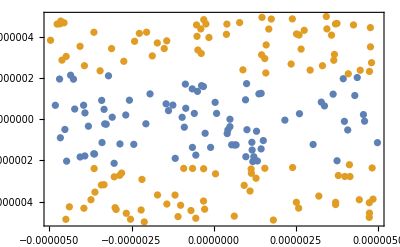

```mathematica
ListPlot[{datapointsasd,datapointsasd2},PlotStyle->PointSize[.013],(*PlotRange->{{-aa1nx,aa1nx},{-aa1n,aa1n}},*)Frame->True,FrameTicksStyle->Directive[FontSize->14],
FrameLabel->{MaTeX["a_{\\text{sd}\\phi 13} \\text{   (GeV)}{^{ -1}}",Magnification->2],MaTeX["a_{\\text{sd}\\phi 31} \\text{   (GeV)}{^{ -1}}",Magnification->2]}]
```

```mathematica
Export["/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/tttt.png",%]
```

/Users/sdb/Library/CloudStorage/Dropbox/CPV_ALP/code/tttt.png

## changeBasis

```mathematica
(*derivativebasisinput={"CQ"->,"CU"->,"CD"->,"CL"->,"CE"->, "YQ"-> , "YU"->,"YD"->,"CG"->,"CW"->,"CB"->,"g1"->,"g2"->,"g3"->}*)
```

```mathematica
Array[RandomReal[]&,{3,3}]
```

{{0.223209,0.111544,0.514299},{0.310079,0.119102,0.367231},{0.213478,0.532208,0.00260917}}

```mathematica
derivativebasisinput=(Thread[{"CQ","CU","CD","CL","CE", "YQ" , "YU","YD"}->zzz]/.zzz->Array[RandomReal[]&,{3,3}])~Join~(Thread[{"CG","CW","CB","g1","g2","g3"}->1])
```

{CQ→{{0.780744,0.889343,0.351196},{0.805684,0.804125,0.156947},{0.880977,0.293246,0.399581}},CU→{{0.780744,0.889343,0.351196},{0.805684,0.804125,0.156947},{0.880977,0.293246,0.399581}},CD→{{0.780744,0.889343,0.351196},{0.805684,0.804125,0.156947},{0.880977,0.293246,0.399581}},CL→{{0.780744,0.889343,0.351196},{0.805684,0.804125,0.156947},{0.880977,0.293246,0.399581}},CE→{{0.780744,0.889343,0.351196},{0.805684,0.804125,0.156947},{0.880977,0.293246,0.399581}},YQ→{{0.780744,0.889343,0.351196},{0.805684,0.804125,0.156947},{0.880977,0.293246,0.399581}},YU→{{0.780744,0.889343,0.351196},{0.805684,0.804125,0.156947},{0.880977,0.293246,0.399581}},YD→{{0.780744,0.889343,0.351196},{0.805684,0.804125,0.156947},{0.880977,0.293246,0.399581}},CG→1,CW→1,CB→1,g1→1,g2→1,g3→1}

```mathematica
Association[derivativebasisinput]["CQ"]
```

{{0.184577,0.743058,0.416303},{0.949296,0.557816,0.556645},{0.832193,0.590097,0.537884}}

```mathematica
derivativebasisinput=(Thread[{"CQ","CU","CD","CL","CE", "YQ" , "YU","YD"}->zzz]/.zzz->Array[RandomReal[]&,{3,3}])~Join~(Thread[{"CG","CW","CB","g1","g2","g3"}->1])
```

```mathematica
changeBasis[list0_]:={"asuϕ"-> I (Association[derivativebasisinput]["YU"].Association[derivativebasisinput]["CU"]- Association[derivativebasisinput]["CQ"].Association[derivativebasisinput]["YU"]),"asdϕ"-> I (Association[derivativebasisinput]["YD"].Association[derivativebasisinput]["CD"]- Association[derivativebasisinput]["CQ"].Association[derivativebasisinput]["YD"]),"aseϕ"-> I (Association[derivativebasisinput]["YE"].Association[derivativebasisinput]["CE"]- Association[derivativebasisinput]["CL"].Association[derivativebasisinput]["YE"]),"asGt"->Association[derivativebasisinput]["g3"]^2/(16 Pi^2) * (Association[derivativebasisinput]["CG"] - 1/2 Tr[Association[derivativebasisinput]["CU"]+Association[derivativebasisinput]["CD"]-2Association[derivativebasisinput]["CQ"]]) ,"asWt"->Association[derivativebasisinput]["g2"]^2/(16 Pi^2) * (Association[derivativebasisinput]["CW"] + 1/2 Tr[ 3 * Association[derivativebasisinput]["CQ"]+Association[derivativebasisinput]["CL"]]),"asBt"->
Association[derivativebasisinput]["g1"]^2/(16 Pi^2) * (Association[derivativebasisinput]["CB"] - Tr[ (4/3) * Association[derivativebasisinput]["CU"]+(1/3) Association[derivativebasisinput]["CD"]-(1/6) Association[derivativebasisinput]["CQ"]+ Association[derivativebasisinput]["CE"]-(1/2)-(1/6) Association[derivativebasisinput]["CL"]])}
```

```mathematica
Association[derivativebasisinput]["YU"]
```

{{0.184577,0.743058,0.416303},{0.949296,0.557816,0.556645},{0.832193,0.590097,0.537884}}

```mathematica
Association[derivativebasisinput]["g1"]^2/(16 Pi^2) * (Association[derivativebasisinput]["CB"] - Tr[ (4/3) * Association[derivativebasisinput]["CU"]+(1/3) Association[derivativebasisinput]["CD"]-(1/6) Association[derivativebasisinput]["CQ"]+ Association[derivativebasisinput]["CE"]-(1/2)-(1/6) Association[derivativebasisinput]["CL"]])
```

-0.0134908

```mathematica
Association[derivativebasisinput]["g2"]^2/(16 Pi^2) * (Association[derivativebasisinput]["CW"] + 1/2 Tr[ 3 * Association[derivativebasisinput]["CQ"]+Association[derivativebasisinput]["CL"]]),
```

0.00633257

```mathematica
Association[derivativebasisinput]["g2"]^2/(16 Pi^2) * (Association[derivativebasisinput]["CW"] + 1/2 Tr[ 3 * Association[derivativebasisinput]["CQ"]+Association[derivativebasisinput]["CL"]])
```

0.0314659

```mathematica
Association[derivativebasisinput]["CG"]
```

{{0.184577,0.743058,0.416303},{0.949296,0.557816,0.556645},{0.832193,0.590097,0.537884}}

```mathematica
derivativebasisinput=dbinputtemplate
```

{CQ→{{0.945746,0.194709,0.551561},{0.867559,0.439311,0.871368},{0.258915,0.911165,0.577586}},CU→{{0.945746,0.194709,0.551561},{0.867559,0.439311,0.871368},{0.258915,0.911165,0.577586}},CD→{{0.945746,0.194709,0.551561},{0.867559,0.439311,0.871368},{0.258915,0.911165,0.577586}},CL→{{0.945746,0.194709,0.551561},{0.867559,0.439311,0.871368},{0.258915,0.911165,0.577586}},CE→{{0.945746,0.194709,0.551561},{0.867559,0.439311,0.871368},{0.258915,0.911165,0.577586}},YU→{{0.945746,0.194709,0.551561},{0.867559,0.439311,0.871368},{0.258915,0.911165,0.577586}},YD→{{0.945746,0.194709,0.551561},{0.867559,0.439311,0.871368},{0.258915,0.911165,0.577586}},YE→{{0.945746,0.194709,0.551561},{0.867559,0.439311,0.871368},{0.258915,0.911165,0.577586}},CG→1,CW→1,CB→1,g1→1,g2→1,g3→1}

```mathematica
changeBasis[derivativebasisinput]
```

{asuϕ→{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}},asdϕ→{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}},aseϕ→{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}},asGt→0.00633257,asWt→0.0311897,asBt→-0.0131686}